## 报告主要写在“实验报告.pdf”中，此文件展示实验过程及调试经历

```mathematica
data = Import["C:/Users/predator/Documents/test2.csv"]
```

{{,,name,广州米兰小筑公寓,美朵精品公寓(广州南站店),帕菲商旅公寓(广州南站店),广州南站精品公寓,广州阿米果主题公寓,广州楠栖小筑公寓,丽柏臻品公寓(广州南站店),柏曼酒店(广州番禺政务中心君御店),柏霖公寓(广州南站店),美丽豪酒店(广州番禺店),1124,广州金湾商务酒店,广州大学城北亭缤果公寓,大坊阁酒店公寓(广州市桥店),梦幻主题公寓(广州钟村店),广州漫步天下公寓(蝴蝶亭分店),广州涵香居快捷公寓,广州有家民宿(日章陈公祠分店),盒子空间馆(广州新天地二号馆),广州长隆鑫琳小居公寓,广州几何の家公寓,格林豪泰(广州番禺广场店),宜尚酒店(广州番禺长隆万达广场万博地铁站店),华意宾馆},30,{1}}
 |  |  |  |

```mathematica
Grid[data]
```

|  | name | 广州米兰小筑公寓 | 美朵精品公寓(广州南站店) | 帕菲商旅公寓(广州南站店) | 广州南站精品公寓 | 广州阿米果主题公寓 | 广州楠栖小筑公寓 | 丽柏臻品公寓(广州南站店) | 柏曼酒店(广州番禺政务中心君御店) | 柏霖公寓(广州南站店) | 美丽豪酒店(广州番禺店) | 广州梓舍艺术酒店 | 喜悦酒店(广州市桥地铁站店) | 广州有家酒店 | 广州丛林大象公馆 | 广州番禺大道希尔顿欢朋酒店 | 广州梓舍酒店 | 乐尔曼酒店公寓(广州南浦地铁站店) | 云泊公寓(广州敏捷店) | 明江优选青年公寓(广州南站店) | 广州阿斯顿服务公寓酒店 | 四季丰公寓(广州南站店) | 广州易成主题酒店(番禺万达广场店) | 广州红象堡树屋酒店 | 江南西酒店(广州市桥店) | 速8酒店(广州番禺市桥易发步行街店) | 柏曼酒店(广州汉溪长隆地铁站大石店) | 广州大学城银天公寓 | 维也纳国际酒店(广州南站祈福新邨国际店) | 宜必思酒店(广州市桥店) | 广州曼途民宿 | 麗枫酒店(广州大石地铁站动物园店) | 广州哈森精品公寓 | 四月上筑精品复式公寓(广州奥园越时代店) | 广州润家服务式公寓 | 广州爱丽思服务公寓 | 布查特管家式酒店(广州锦绣店) | 广州金轩宇商务公寓 | 星悦遵品公寓(广州番禺动物园北门店) | 广州艾斯曼公寓 | 钧玺主题式酒店公寓(广州万达汉溪长隆地铁站店) | 广州彬彬商务公寓 | 悦季酒店(广州洛溪地铁站店) | 微香屋主题公寓(广州汉溪长隆地铁站店) | Q加·精灵王国主题公寓(广州番禺万达店) | 红专屋公寓(广州番禺广场地铁站店) | 雨晴公寓(广州汉溪长隆地铁站店) | 愉舍酒店(广州番禺野生动物园大石地铁站店) | 广州约翰达国际公寓 | 城市便捷酒店(广州汉溪长隆市桥地铁站店) | 广州枫情海主题公寓 | 广州探云田居民宿 | 广州亲漫主题公寓 | 广州泊泰国际精品公寓 | 维多利亚公寓(广州南站店) | 广州图南生活美学酒店 | 广州有舍公寓 | 广州花墨公寓 | 广州無宿民宿 | 广州番禺宾馆 | 美豪丽致酒店(广州番禺银座店) | 森林密码主题公寓(广州南站汉溪长隆地铁站店) | 广州彼家公寓 | 隆斯莱斯主题酒店公寓(广州番禺动物园北门店) | 盒子空间色彩公寓(广州华师店) | 广州珍宝假日酒店 | 凯萨艺术公寓(广州南站店) | 柏曼酒店(广州番禺桥南奥园广场店) | 橙子时尚公寓(广州厦滘地铁站店) | 总统大酒店(广州汉溪长隆地铁站店) | 麗枫酒店(广州高铁南站会江地铁站店) | 麗枫酒店(广州南站汉溪长隆站店) | 名季酒店(广州亚运城店) | 广州杰圣酒店 | 南铁大酒店(广州南站店) | 广州铂格主题公寓 | 广州大学城新天地J精品酒店 | 广州斯尼原创艺术主题公寓 | 鲜居精品主题酒店(广州番禺动物园景区店) | 奥美家国际公寓(广州奥园国际中心店) | 广州悦霖居精品公寓 | 广州思铂瑞国际公寓 | 广州大学城天缘公寓贝岗店 | 汉庭酒店(广州大石野生动物园店) | 广州逸庭公寓 | 维也纳酒店(广州番禺长隆南村店) | 城市便捷酒店(广州汉溪长隆大石地铁站店) | 广州百利公寓汉溪店 | 腾森酒店公寓(广州南站店) | 广州键盘侠电竞公寓 | 易成主题公寓(广州汉溪长隆地铁站保利大都汇店) | 广州俊王酒店 | 小叶子酒店公寓(广州汉溪长隆地铁站店) | 非繁·精品酒店(广州市桥易发步行街店) | 如家酒店(广州番禺南村暨南大学板桥地铁站城业广场店) | 途寓主题公寓(广州石壁地铁站店) | 广州星河湾酒店 | 维也纳酒店(广州番禺长隆金江大道店) | 广州叶子小筑公寓 | 广州南雅一号酒店 | 城市便捷酒店(广州汉溪长隆站万达广场店) | 小艾驿站公寓(广州汉溪长隆地铁站店) | 精灵电竞公寓(广州万达广场店) | 广州番禺区嘉华酒店 | 宜尚酒店(广州长隆板桥地铁站店) | 7天连锁酒店(广州番禺市桥地铁站店) | 广州美泊精品公寓 | 帕菲主题公寓(广州番禺野生动物园店) | 广州乐曼泊酒店 | 麗枫酒店(广州汉溪长隆站万达广场店) | 广州蓝舍精品酒店 | 广州长广酒店 | 派酒店(广州番禺石岗步行街店) | 7天优品(广州长隆站动物园北门店) | 胜龙酒店(广州钟村地铁站店) | 易佰连锁旅店(广州番禺市桥地铁站店) | 广州爱洛思主题酒店 | 唯家·舒享公寓(广州员岗地铁站店) | 怡莱酒店(广州番禺动物园大石地铁站店) | 维也纳酒店(广州番禺广场店) | 归趣电影主题设计师精品公寓(广州番禺万达店) | 广州普琳商务酒店 | 钧玺公寓(广州汉溪长隆地铁站店) | 汉庭酒店(广州南村员岗地铁站店) | 域酒店(广州洛溪地铁站店) | 品若公寓(广州桥南店) | 喆啡酒店(广州番禺野生动物园店) | 考拉亲子主题公寓(广州万达汉溪长隆地铁站店) | 广州柏雅精品酒店式公寓 | 广州山海公寓 | 私享家服务式公寓(广州汉溪长隆地铁站店) | 广州金柏豪酒店 | 奥美家国际公寓(广州汉溪长隆地铁站店) | 麗枫酒店(广州厦滘地铁站迎宾路店) | 城市便捷酒店(广州大石地铁站动物园总店) | 广州美丽假期酒店 | 广州邦舍酒店 | 喆啡酒店(广州南站南浦地铁站店) | 广州聚缘时尚公寓 | 梦佳期电影酒店(广州石碁店) | 广州他乡客公寓 | 广州维悦服务式公寓 | 广州科尔海悦酒店 | 维也纳酒店(广州南站南浦地铁站店) | 广州万盛名家酒店 | 维福顿公寓(广州万达广场店) | 广州罗曼的假日 | 维也纳酒店(广州番禺长隆大石地铁站店) | 拉美国际公寓(广州汉溪长隆地铁站店) | 西维拉国际公寓(广州金龙城店) | 广州茂丰酒店 | 维也纳酒店(广州南站会江地铁站店) | 广州星誉国际公寓 | 广州快莱商务宾馆 | 广州番禺戴斯酒店 | 广州铁旅大酒店 | 7天连锁酒店(广州高铁南站南浦地铁口站店) | 维也纳酒店(广州番禺长隆市桥地铁站店) | IU酒店(广州高铁南站钟村地铁站店) | 麗枫酒店(广州市桥地铁站易发步行街) | 致尚主题公寓(广州南站店) | 鲜居精品主题酒店(广州哈街店) | 怡悦酒店(广州南浦地铁口店) | 广州大学城豆豆公寓 | 如家驿居酒店(广州番禺长隆店) | 广州金爵豪庭公寓 | 汉庭酒店(广州野生动物园南门店) | 如家精选酒店(广州番禺长隆野生动物园店) | 驿居酒店(广州厦滘地铁口店) | 广州飞悦依灵民宿 | 派酒店(广州市桥地铁站店) | 广州南站戴斯酒店 | 潮漫酒店(广州钟村店) | 四叶草公寓(广州未来域店) | 维也纳酒店(广州番禺亚运城店) | 北海稻酒店(广州南村店) | 宜尚酒店(广州市桥地铁站钻汇广场店) | 广州欧时快捷酒店钟村店 | 乐尔曼雅悦国际公寓(广州南站店) | 广州润佳精品酒店 | 广州奇萌公寓 | 铂顿国际公寓(广州番禺政务中心店) | 舒馨公寓(广州新白云国际机场二店) | 如家酒店·neo(广州番禺市桥地铁站易发步行街中心店) | 广州番禺丽柏酒店 | 广州君尚公寓 | 铂曼主题公寓(广州南站店) | 艺霖坊状元文宿(广州沙湾店) | 美宿服务式酒店公寓(广州汉溪长隆地铁站店) | 潮漫酒店(广州南站南浦地铁站店) | 广州vhome国际主题公寓(奥园广场店) | 广州智联公寓 | 美偲途公寓(广州南站店) | 广州金孔雀精品民宿 | 笆笆拉酒店(广州大岗店) | 广州卓思道酒店 | 维也纳酒店(广州南站汉溪长隆景区店) | 怡莱酒店(广州番禺广场地铁站店) | 她他会服务公寓(广州万达汉溪长隆地铁站) | 广州城北酒店公寓 | 寓米精品公寓(广州洛溪地铁站渔人码头店)(原私享家公寓) | 广州铂德酒店 | 广州四叶草公寓雄峰城店 | 广州斯维登服务公寓(洛溪地铁站渔人码头) | 广州珍宝艺术酒店 | 寓米精品公寓(广州高铁南站汉溪长隆地铁站店) | 广州彩蝶居 | 奇幻花园公馆(广州汉溪长隆地铁站店) | 广州大学城橙子小屋公寓贝岗店 | 笆笆拉酒店(广州大石地铁站店) | 如家酒店(广州番禺大岗长途汽车客运站店) | 巨大国际公寓(广州会江地铁站店) | 名季酒店(广州沙湾古镇店) | 骏福酒店(广州南浦地铁站店) | 艾薇公寓(广州汉溪长隆地铁口店) | 天和精品酒店(广州市桥地铁站店) | 辉龙商务酒店(广州番禺广场店) | 广州京泰丽都酒店 | 广州万泓国际酒店 | 希盟公寓(广州南站汉溪长隆地铁站店) | 广州耐斯顿主题公寓 | 龙穗公寓(广州南站店) | 广州無墅民宿 | 广州喜临院酒店 | 隆堡酒店(广州长隆市桥地铁口店) | 广州祈福国际公寓 | 广州喜御酒店 | 盒子空间(广州大学城旗舰店) | 广州欢乐窝艺术主题精品公寓 | 如家商旅酒店(广州厦滘地铁站店) | 维也纳国际酒店(广州番禺市桥中心国际店) | 广州依力精品主题酒店 | 广州西丽酒店 | 广州新君兰酒店 | 7天连锁酒店(广州高铁南站会江地铁站店) | 铁程大酒店(广州南高铁站店) | 柏曼酒店(广州市桥地铁站易发步行街店) | 7天连锁酒店(广州番禺广场市莲路店) | 广州至诚公寓 | 麗枫酒店(广州洛溪厦滘地铁站店) | 广州八夜酒店 | 广州8天酒店式公寓 | 博雅居公寓(广州南站店) | 广州美琳公馆 | 维也纳酒店(广州南高铁站店) | 广州住星精品主题酒店 | 广州温馨驿屋公寓 | 广州广州祈福新村老顾客度假公寓 | 广州小沐公寓 | 广州薰衣草之家(广州汉溪长隆地铁站奥园店) | 广州长隆温馨复式公寓5房 | 广州陈夏公寓 | 广州长隆驿站公寓 | 广州燕子的新家公寓 | 广州星星之屋度假别墅(4号店) | 广州余钦度假别墅(3号店) | 广州喜爱居公寓(汉兴西路分店) | 广州Mo创始人特色别墅 | 广州HappyHome精品公寓汉溪地铁店 | 广州PINKO公寓 | 广州米兰小筑公寓(韦海路分店) | 广州暖暖公寓(长岗街分店) | 广州南站/长隆度假区/万科世博汇优品民宿(石兴大道南分店) | 广州238途乐精品公寓 | 广州红红公寓(2号店) | 广州小叮当法宝响当当民宿 | 广州悠游途舍公寓(福华路分店) | 广州康超公寓 | 广州BBcheung公寓(2号店) | 广州小阿古公寓 | 广州楠园民宿(卡奇儿童乐园分店) | 广州寡人愛才公寓 | 广州一舍网红民宿(2号店) | 广州长隆哆啦亲子主题公寓 | 广州燕子的新家公寓(13号店) | 广州长隆精品民宿 | 广州番禺金鹏旅馆 | 广州茉莉花园公寓 | 广州长隆芒果公寓(9号店) | 广州六玥海-猪捨度假别墅(7号店) | 广州佳怡公寓 | 广州聚缘住宿 | 广州猫猫@窝居公寓(26号店) | 广州刘旭辉公寓 | 广州秋云公寓(3号店) | 随意宅公寓 | 广州魏娜姐的小窝公寓(石山大道南分店) | 广州土土Kym公寓 | 广州雅静快捷公寓 | 广州Summerhigh公寓 | 广州Annie芳公寓(2号店) | 广州大洲路好再来公寓 | 广州紫色风铃公寓 | 广州豪景酒店 | 广州住得乐民宿 | 广州四季梦幻主题公馆 | 广州淘淘居公寓 | 广州番禺清馨幽舍公寓 | 广州番禺金枝公寓 | 乐途主题公寓(广州番禺万达店) | 广州南园酒店 | 广州鹿途-轻奢酒店式公寓 | 广州晴天主题公寓野生动物园店 | 广州帕丁曼公寓 | 广州南浦家公馆酒店 | 广州番禺现代公寓 | 广州尚品公馆 | 168精品公寓(广州大学城广工店) | 广州恰好时尚公寓 | 广州石基爱情公寓 | 广州潘多拉精品公寓 | 盒子空间怡景公寓(广州广美三号店) | 广州MW民宿 | 广州鸿凤旅店 | 广州悦来公寓 | 广州享香睡公寓 | 广州幽兰之家公寓 | 广州乐活年华公寓 | 广州居然之家公寓 | 广州雅居公寓 | 广州大沙酒店 | 广州沙芭比亚酒店 | 广州广州长隆阳光家园公寓(泡泡大战分店)(泡泡大战分店) | 广州大学城馨梦公寓 | 偶来民宿(广州汉溪长隆店) | 简驿酒店(广州市桥地铁站店) | 广南酒店(广州南站店) | 可欣公寓(广州石壁站店) | 广州南站阳光公寓(2号店) | 广州莲花山岭南佳园度假酒店 | 广州大学城吉吉公寓 | 广州文明酒店 | 广州懿栈公寓 | 艾米公寓(广州渔人码头店) | 广州MOJOHOUSE客栈 | 美雅国际公寓(广州环村路店) | 广州烨瑀客栈 | 广州华宝宾馆 | 广州长隆芒果公寓(2号店) | 寓米精品公寓(广州长隆东门总统公馆店) | 广州凯莉莱酒店(番禺店) | 广州增城青年公寓 | 广州靓点住宿 | 广州佳兴商务酒店 | 广州豪润酒店 | 广州金垒商务酒店 | 广州名粤酒店 | 广州长隆南国奥园度假酒店公寓(奥园城市天地分店) | 广州19公寓 | 广州佳缘主题公寓 | 寓见公寓(广州招商城市主场店) | 广州宇逸居 | 广州Ai住宿 | 广州三宅之家公寓 | 广州窝居公寓 | 广州广大商务酒店 | 广州荟朋酒店 | 广州九九公寓 | 广州星玥主题公寓 | 广州李师傅租房 | 广州广程快捷公寓 | 广州大学城Sweet House主题公寓 | 广州番禹时代住宿 | 米娅酒店(广州沙湾分店) | 广州启程万达公寓 | 广州大学城德和公寓 | 哈鹿艺舍民宿(广州汉溪长隆地铁站店) | 广州奢绘公馆 | 广州梓里酒店 | 广州六合公寓 | 广州鸿星旅馆 | 星寓传奇服务式公寓(广州钟村店) | 途安客栈(广州番禺万达店) | 广州逸米家公寓 | 广州大学城高升客栈 | 广州南站小筑公寓 | 广州美洋洋公寓 | 金丰公寓(广州钟村店) | 广州嘉美公寓 | 广州我爱我家酒店公寓 | 长隆锦绣香江度假别墅 | 广州市化龙京宝旅店 | 广州M院广州南站尚岛国际酒店公寓 | 广州家意公寓 | 奥园恒泰公寓(广州汉溪长隆地铁站店) | 派柏·云酒店(广州番禺万博汉溪长隆店) | V酒店(广州荔园新天地店) | 广州宜尚精品公寓 | 广州怡庭假日大酒店 | 广州滑滑梯乐园主题民宿 | 广州尚品公寓 | 广州福安宾馆 | 非繁·盈美酒店(广州汉溪大石动物园北门店) | 长隆香江酒店(广州长隆野生动物世界店) | Q加·不红舍公寓(广州汉溪长隆地铁站店) | 广州聚相楚公寓 | 广州爱零假日公寓 | 广州嗨森公寓(兴业大道西分店) | 广州Tam.SJ度假别墅 | 广州贾末公寓 | 广州Boey公寓 | 广州逸心小居公寓 | 广州雅琪张公寓(3号店) | 广州长隆芒果公寓(4号店) | 广州铭城公寓(担水涌路分店) | 广州美妈家1公寓(茶庄园路分店) | 广州钱得乐Wu公寓(2号店) | 广州钱得乐Wu公寓(5号店) | 广州近长隆/南站/飞机场复式双床房公寓(4号店) | 广州蔡宏斌英语公寓 | 广州番禺长隆大学城北上广聚会别墅轰趴馆 | 广州乡村旅馆 | 广州阑珊·home公寓(汉溪大道东分店) | 广州linlinv公寓(礼村中路分店) | 广州锦绣香江别墅公寓之家(里仁洞村占贤大道分店) | 广州菜菜菜之家公寓 | 广州乐彼妈公寓(工业四路分店) | 广州benson沈先生公寓(光明北路分店) | 广州宏新住宿 | 广州Jc酱公寓 | 广州广州W夕霞小筑(卡奇儿童乐园分店) | 广州近长隆/南站/飞机场复式双床房公寓(3号店) | 广州winnie_公寓(6号店) | 广州拾光满屋公寓 | 广州candyhouse糖果屋公寓(7号店) | 广州温馨虾米之家公寓(2号店) | 广州流星雨公寓(11号店) | 广州viki设计师之家公寓(2号店) | 广州花城驿站(新光快速分店) | 广州悠然美宿 | 广州李木子gz公寓 | 广州猪老板公寓 | 广州筑梦先生公寓(12号店) | 广州阑珊home公寓(卡奇儿童乐园分店) | 广州MARU公寓(5号店) | 广州南浦一家民宿 | 广州筑梦先生公寓(8号店) | 广州HappyHome精品公寓汉溪地铁店(3号店) | 广州华悦小敏客栈 | 广州私享家曼哈顿尚层公寓 | 广州金海湾公寓 | 广州筑梦先生公寓(14号店) | 广州小鹿奇缘公寓(2号店) | 广州蜗牛姐公寓(7号店) | 广州清馨民宿(卡奇儿童乐园分店) | 广州晓欣公寓 | 广州设计师的家二号店公寓 | 广州世博汇之家公寓 | 广州客乡缘宾馆 | 广州OMGgongyu公寓(工业二路分店) | 广州长隆温馨之家公寓 | 广州南浦住宿 | 广州多惠利商务会所 | 广州番禺·如佳公寓(琪琪康乐园分店) | 广州無居度假别墅(7号店) | 和舍艺术酒店公寓(广州御峰国际店) | 广州乔鑫宾馆 | 广州上佳住宿 | 广州南浦公寓 | 广州敏捷上城国际度假套房公寓(2号店) | 广州富鑫住宿 | 广州爱得宝公寓 | 广州隆鑫公寓 | 广州青训电竞公寓 | 广州祥盛旅馆 | 广州官涌如意住宿 | 吉祥宾馆(广州番禺店) | 广州志业公寓 | 广州家美住宿 | 广州楠园公寓 | 广州途安南苑公寓 | 广州大学城鑫苑公寓 | 广州200间连锁公寓北亭总店 | 广州栖舍公寓 | 广州遇见你青旅 | 广州大学城兰亭雅居公寓 | 广州程祥租房 | 广州品致艺术主题公寓 | 广州大学城开心公寓 | 广州薄荷青旅 | 广州蚂蚁连锁青年旅舍 | 心栖公寓(广州汉溪长隆地铁站店) | 广州大学城君悦公寓贝岗店 | 广州大学城常裔连锁公寓 | 喜窝民宿(广州长隆敏捷伊顿店) | 中庭国际公寓(广州大石地铁站店) | 广州番禺大岗园林宾馆 | 广州广州美芯公馆公寓(工业四路分店) | 广州宏辉公寓 | 广州叶子小窝公寓(3号店) | 广州良缘公寓 | 广州花苑公寓(大学城广工店) | 广州樂家公寓 | 广州华城宇舍公寓(万惠一路分店) | 广州大学城阳光公寓 | 广州思雅小筑公寓 | 广州住得乐公寓 | 泰禹商务酒店(广州汉溪长隆大石地铁站店) | 其乐一家精品公寓(广州野生动物园北门店) | 广州番禺嘉豪商务宾馆 | 美朵公寓(广州奥园越时代店) | 广州168地铁公寓 | 广州金龙旅店 | 广州大学城宜佳公寓 | 广州凌光羽影主题公寓 | 南铁酒店(广州南站店) | 广州敏捷上城国际度假套房公寓(3号店) | 广州花开时艺术主题公寓 | 广州广州番禺山莲鑫旅店 | 广州全家福公寓 | 广州铁程酒店 | 广州尚岛宜居精品公寓 | 广州墨·宿公寓(古雅艺术馆分店) | 广州广州芒果仁度假别墅(2号店) | 广州爱尚公寓新沙路店 | 广州遇见那最特别的你公寓(7号店) | 广州柠檬精品主题公寓 | 广州汉溪路青年公寓 | 享思会主题公寓(广州保利大都汇店) | 广州明珠精品酒店 | 薰衣草之家(广州汉溪长隆地铁站奥园店) | 广州喜洋洋租房 | 广州大学城佳家公寓 | 广州塘西公寓 | 广州米佳公寓 | 广州红8号公寓 | 广州四季如春公寓 | 广州大学城贝岗鸿运公寓 | 广州鹏博公寓 | 广州华都精品公寓 | 广州沐微精品公寓 | 广州绪仁公寓 | 广州祈福度假公寓 | 广州香薇雅寓 | 广州美缘公寓 | 馨悦公寓(广州大学城店) | 广州广缘连锁公寓 | 盒子空间SpaceBox公寓(广州广外一号馆) | 广州蔚然公寓 | 广州番禺香江大酒店 | 广州梦田公寓 | 广州曼雅时尚酒店 | 奥斯顿主题度假公寓(广州大石地铁站店) | 广州鑫雅公寓 | 广州燕子轩公寓 | 广州娜薇主题公寓 | 广州7天精品公寓北门店 | 索菲特公寓(广州南站店) | 广州毛家客栈2号店 | 容易复式(广州福华路店) | 广州大学城立信公寓 | 广州新佳精品酒店 | 广州奥华国际酒店公寓奥园广场店 | 广州友来公寓 | 广州家美公寓 | 广州祈福美馨公寓 | 广州家韵公寓 | 广州愿你达成所愿公寓(3号店) | 鑫余之家服务公寓(广州锦绣店) | 银湾酒店(广州市桥地铁站店) | 365主题公寓(广州华师大学城店) | 广州casa公寓(7号店) | 广州长隆北门静栖艺术主题度假公寓(工业四路分店) | 广州小镇公寓 | 广州一米阳光公寓 | 广州casa公寓(6号店) | 广州jessie小姐姐公寓(6号店) | 广州麦哲伦公寓 | 广州南方与北方公寓 | 广州自如公寓(3号店) | 广州BruceGu度假别墅 | 广州筑梦先生公寓(4号店) | 广州大大大大大公寓(2号店) | 广州筑梦先生公寓(17号店) | 广州蒲舍度假别墅(金奥街分店) | 广州楠园民宿(6号店) | 广州Boey公寓(3号店) | 广州筑梦先生公寓(10号店) | 广州叶子小窝公寓 | 广州桃源居guest house复式 | 广州蜗牛姐公寓(4号店) | 广州KK_哥公寓 | 广州小虫1580公寓(2号店) | 广州长隆旅游度假别墅公寓代订票(4号店) | 广州美妈家1公寓(新光快速辅路分店) | 广州番禺长隆有家公寓(6号店) | 广州祈福新村缤纷世界山水公寓(沙圩一村分店) | 广州赵William公寓 | 广州朴宿喜度Tony公寓(ALPHA分店) | 广州森堡公寓(南大路分店) | 广州长隆温馨复式公寓5房(6号店) | 广州BuluGuluHouse度假别墅 | 广州亚米太空舱公寓(厦滘地铁站店) | 广州祈福新邨福华度假公寓(14号店) | 广州流星雨公寓(7号店) | 广州罗卫红公寓 | 广州长隆北门静栖艺术主题度假公寓(盛泰路店) | 和舍艺术酒店公寓(广州洛溪长隆店) | 广州e+时空公馆 | 广州可乐2018公寓(番禺金街分店) | 广州Foryou公寓(4号店) | 广州那茉广州公寓(工业四路分店) | 广州Rany月雅-雅筑共享民宿(华源路分店) | 广州南站枫情海公寓(2号店) | 广州.广州彩林阁精品公寓 | 广州清风小筑公寓 | 广州小唐公寓 | 广州旺客9天快捷公寓 | 广州长隆小林居公寓(2号店) | 广州归园居公寓 | 广州谭大姐公寓 | 广州锦绣香江别墅公寓之家(诺德路分店) | 广州容宿公寓(市广路分店) | 广州彦坤公寓 | 广州筑梦先生公寓(7号店) | 广州仙女可可公寓 | 广州永善村好又来住宿 | 广州开心豪华公寓 | 广州南站英强精品公寓(韦海路分店) | 广州island美宿公寓(韦海路分店) | 广州居之源公寓 | 广州泰栈快捷公寓 | 广州南站红树林民宿 | 广州安陈美眉公寓 | 广州C6公寓 | 广州吉普尼公寓(沿沙路分店) | 广州启源精品酒店式公寓 | 广州MARU公寓(4号店) | 广州四月上筑精品复式公寓-豪华复式相隔三床房 | 广州傅登住宿 | 广州速8公寓 | 广州一家人公寓沙溪店 | 广州枫悦公寓 | 广州鸿福公寓 | 广州阑珊·home公寓 | 太石豪客公寓 | 广州悦享小筑 | 广州平安住宿 | 广州红红公寓(11号店) | 广州番禺金丰公寓 | 广州老顾客度假公寓 | 广州静夜思主题公寓 | 浮白电竞公寓(广州南村万博地铁站店) | 广州程悦公寓 | 广州启航公寓 | 广州馨缘主题公寓 | 广州长隆地铁口保利大都汇三居室复式公寓 | 鸿运公寓(广州富怡路店) | 广州美栖精品民宿 | 广州嘉和精品酒店 | 广州御家主题公馆 | 希悦酒店(广州南村万博店) | 广州天骄嘉园公寓 | 米家公寓(广州南站店) | 广州大金福公寓 | 索特来文艺酒店(广州石基文化广场店) | 广州富民公寓 | 广州柠檬公寓 | 广州好望角公寓 | 广州大学城缤果公寓 | 广州宜居公寓 | 金色阳光公馆(广州汉溪长隆地铁站万达店) | 广州恒泰精品公寓 | 广州六八公寓 | 广州官涌豪华住宿 | 广州盛光商务公寓 | 广州恋影小屋 | 壹号公寓(广州高铁会江地铁站店) | 米舒度假公寓(广州汉溪长隆地铁站店) | 广州牵手主题公寓 | 广州小美好的客栈 | 广州朗泉湾酒店 | 广州朴宿喜度Tony公寓(长岗街分店) | 广州唯馨公寓 | 广州骏宇酒店 | 广州小蓬莱公寓 | 广州AT西街民宿 | 广州普爱假日公寓 | 广州金豪公寓 | 逸旅公寓(广州信业悦都荟店) | 广州澜轩尚品公寓 | 广州大学城安居公寓 | 广州7号公寓 | 广州百合假日公寓 | 广州川之夏公寓 | 广州筑梦先生公寓(11号店) | 广州怡徕公寓 | 广州友间公寓 | 广州番禺金悦宾馆 | 广州劳氏公寓 | 隆翠荟主题公寓(广州南站店) | 广州小小私享家公寓 | 广州米娅国际酒店公寓 | 广州青春YOUandME公寓贝岗店 | 广州大学城北亭村博源楼 | 广州柠檬精品主题公寓(4号店) | 广州壹季时光公寓 | 广州新科公寓大学城店 | 逸米酒店广州长隆市桥地铁站店 | 广州大石街悦来公寓 | 广州TT原舍公寓 | 广州白鹿青年旅社 | 广州宏达旅馆 | 广州名美假日公寓 | 鹿小驿主题度假公寓(广州旅游区北门店) | 广州佳驿公寓 | 广州宝丛酒店 | 广州爱啦屋酒店 | 广州幕色年华青年旅舍 | 汉庭酒店(广州番禺市桥步行街店) | 广州信义住宿 | 星驿国际度假公寓(广州动物园景区北门店) | 广州泊居公寓 | 广州敏捷上城国际度假套房公寓(5号店) | 如家酒店·neo(广州番禺市桥步行街店) | 广州锦湖酒店 | 广州泓晶之恋臻品酒店 | 平安公寓(广州番禺店) | 广州皇圣逸林酒店 | 骏福宾馆(广州石基店) | 广州番禺红星住宿 | 广州誉瀛酒店公寓 | 金海岸酒店(广州市桥地铁站店) | 广州南站华美达安可酒店 | 广州星河湾半岛酒店 | 广州暖居快捷公寓 | 广州奥园高尔夫酒店 | LOVE主题公寓(广州万达汉溪长隆地铁站) | 广州天禄酒店 | 怡莱酒店(广州市桥地铁站店) | 广州逸家精品公寓 | 广州嘉翔商务酒店 | 骏福酒店(广州番禺广场地铁站店) | 广州尚家精品酒店 | 猫星别墅公寓(广州中海蓝湾店) | 广州蒲舍度假别墅(环村公路分店) | 广州薇薇家公寓 | 广州L林鑫公寓(新浦南路分店) | 广州长隆旅游度假别墅公寓代订票(3号店) | 广州广州东北媳妇公寓 | 广州Helen海伦公寓 | 广州Helen海伦公寓(长隆国际会展中心分店) | 广州广州铜草花公寓 | 广州等待春暖花开公寓(汉溪大道东辅路分店) | 广州珂珂美宿公寓(汉溪大道东分店) | 广州盖乐世别墅套房酒店公寓 | 广州王叔工房公寓(钟韵路分店) | 广州长隆旅游度假别墅公寓代订票(2号店) | 广州嘤嘤嘤公寓(58号店) | 广州番禺阳光租房 | 广州雅琪张公寓 | 广州刘旭辉特色民宿 | 广州小叮当法宝响当当复式公寓 | 广州途驿公寓(3号店) | 广州花苑公寓广工店 | 广州广州城市邂逅公寓 | 广州保利大都汇遇家臻品公寓 | 广州粤美居公寓(新光快速分店) | 广州蒲舍度假别墅(2号店) | 广州气泡水公寓 | 广州黄鑫公寓 | 广州陈洪波公寓 | 广州安东阁公寓(富华东路分店) | 广州佳信宾馆 | 广州大石恒泰公寓 | 广州时尚公寓市莲路店 | 大学城6号公寓 | 广州皓月公寓 | 广州市桥金洋旅馆 | 8号公寓(广州石碁地铁店) | 广州新一佳公寓 | 广州爱巢商务公寓 | 广州广州麻田居公寓 | 广州半夏时光公寓 | 广州骏涵•昆江服务式公寓 | 广州福清旅店 | 广州金福宾馆 | 惠伊凡度假公寓(广州汉溪长隆地铁站店) | 广州奇幻熊猫公馆亲子民宿 | 广州金百合租房 | 广州大学城爱丽丝与花公寓 | 广州金怡酒店 | 广州惠舒美公寓 | 广州时光转角公寓 | 广州逸美公寓 | 广州奥斯卡公寓 | 广州枫枬丽舍 | 广州TIME时光民宿(汉兴中路分店) | 美居乐(广州工业学校店) | 广州尚安公寓 | 广州大学城增福公寓 | 广州谷围假日商务宾馆 | 广州天青舍青年旅舍 | 广州26°精品公寓 | 广州华北一街千盛公寓 | 野先生民宿(广州汉溪长隆地铁站店) | 广州梦思特酒店番禺店 | 广州番禺金辉宾馆 | 广州程素云租房 | 广州CICI民宿 | 广州柏秀度假公寓 | 广州番禺常来住宿 | 盒子空间好时光公寓(广州广外三号馆) | 广州祈福新村缤纷世界山水公寓(迎福路分店) | 欧斯塔公寓(广州南站店) | 广州同心旅馆 | 广州茶东住宿 | 广州番星国际公寓 | 广州星夜酒店 | 广州午后时光公寓 | 广州岭南商务公寓 | 广州校园公寓 | 广州阳光灿烂每一天公寓 | 广州大学城穗石村韩都公寓 | 广州鸿轩公寓 | 广州大学城枫林云客栈 | 广州大学时光公寓 | 广州Lucky温馨的小家公寓 | 广州乐野亲子主题公寓 | 广州宿8民宿 | 广州鑫辉旅店 | 广州雅婷时尚公寓 | 广州长隆家园公寓 | 广州番禺莲花山粤海度假酒店 | 广州田园公寓 | 广州新佳时尚酒店 | 广州威利公寓 | 广州泊湾公馆 | 广州百合家园酒店公寓 | 帝豪公寓(广州东涌店) | 广州家途公寓 | 广州舒悦公寓 | 广州柏南奇酒店 | 广州仁厚公寓 | 广州壹号公寓 | 广州市柒天公寓 | 广州蓝雀精品艺术酒店 | 如家酒店(广州高铁南站南浦地铁口店) | 广州星程公寓 | 广州简栖公寓 | 广州6号客栈 | 广州大夫山雅榆艺术酒店 | 广州PVGO客栈 | 一米阳光公寓(广州北亭店) | 广州明月酒店 | 美悦精品公寓(广州南站店) | 维也纳国际酒店(广州南站国际店) | 广州莜驿酒店 | 广州远方的家公寓 | 芭提雅阁公寓(广州南站店) | 广州永良租房 | 广州大学城这里连锁公寓 | 朵尔曼国际酒店(广州南站店) | 广州海伦春天公寓 | 格林豪泰(广州欢乐世界员岗地铁站店) | 7天酒店(广州南站祈福汉溪长隆站店) | 奇幻马戏公馆(广州汉溪长隆地铁站招商主场店) | 莱卡主题公寓(广州石基店) | 广州温馨镁屋公寓 | 广州柚子哥公寓(4号店) | 广州TIME时光民宿 | 广州逸心宜驿公寓(市广路分店) | 广州逸心宜驿公寓(2号店) | 广州蜗牛姐公寓 | 广州广州萌萌哒的小仙女公寓 | 广州HappyHome精品公寓汉溪地铁店(2号店) | 广州番禺猫王轰趴别墅 | 广州万达公寓植村店 | 广州有家民宿(兴南大道分店) | 广州保利大都汇遇家臻品公寓(2号店) | 广州时光·海傍公寓(4号店) | 广州無墅民宿(番禺大道北辅路分店) | 广州旅家欢聚公寓 | 广州长隆云顶度假公寓(3号店) | 广州极客民宿(万惠一路分店) | 广州闪猪美宿长隆旅游区公寓(17号店) | 广州dy6688520公寓(大洲路分店) | 广州许梓莹度假别墅 | 广州贝岗苹果公寓 | 广州静雅居民宿 | 广州大学城橘子公寓 | 广州星影公寓 | 广州大学城馨缘公寓 | 广州嗨贝比主题民宿 | 广州大学城嘉乐公寓(原龙凤公寓) | 友缘公寓(广州基龙西路店) | 广州鸿鑫商务宾馆 | 广州豪廷3D主题公寓大学城南店 | 广州艾优美主题公寓 | 西余公寓(广州大学城店) | 广州乐屏公寓 | 广州阳光商务公寓 | 广州广州W夕霞小筑公寓 | 广州米莉家公寓 | 广州乐豪租房 | 广州香美园公寓 | 广州金丰宾馆 | 驿居酒店(广州番禺南村暨南大学板桥地铁站城业广场店) | 广州宏创精选酒店式公寓 | 广州盛夏公寓 | 大学城流星雨公寓(广州广大店) | 广州Young形影不离电影公馆 | 广州圆梦商务宾馆 | 广州番禺龙兴旅馆 | 广州猫猫@窝居公寓(22号店) | 广州祈福新邨福华度假公寓(11号店) | 广州山水天合公寓(3号店) | 广州逸佳公寓 | 广州喜鹊宝贝公寓(4号店) | 广州长隆住一住民宿 | 广州闲适小居公寓(5号店) | 广州莱筑品质空间公寓 | 广州安东阁公寓 | 广州一栈hotel公寓 | 广州柏朗酒店 | 广州大学城mini22公寓 | 广州枫叶酒店 | 广州菲菲HOUSE酒店式公寓 | 广州朗淘电竞主题公寓 | 广州沙拉村舍 | 广州金诚酒店 | 星期天酒店(汉溪北门店) | 美途梦享空间公寓(广州石基店) | 广州慕色酒店番禺市桥地铁站店 | 广州海贼王主题公寓(北亭大街店) | 广州小时代美好民宿 | 广州西关小舍丶(4号店) | 广州陌花公寓 | 广州世纪家园度假公寓 | 广州番禺锦绣公寓 | 广州文锦公寓 | 广州番禺怡家公寓 | 陌临阁青旅(广州大洲店) | 广州天祺时尚公寓 | 广州锦和公寓 | 住得乐公寓(广州青云坊店) | 广州栖枟民居CharmOne(9号店) | 广州悦尔～民宿(2号店) | 广州6号棋牌如家租房公寓 | 广州同学驿站 | 广州言品主题公寓 | 广州添浪租房 | 广州富力合赢公馆公寓 | 广州南站枫情海公寓(4号店) | 本树家公寓(广州汉溪长隆地铁站店) | 广州柠檬树日租公寓 | 广州新丽都酒店 | 广州My hotel度假公寓 | 广州南阁公寓 | 广州阳光连锁公寓 | 广州纳迪公寓 | 广州FRIDAYINN星期五公寓 | 广州信基杉谷文化酒店 | 广州港湾服务式公寓 | 广州名都度假公寓 | 广州广州拾野川民宿 | 阳光客栈(市桥一店) | 广州贝岗爱心主题公寓 | 广州祈福缤纷汇长隆主题公寓妮可的花房公寓 | 广州花鹿民宿(3号店) | 广州馨途公寓(7号店) | 广州归园居公寓(6号店) | 广州滴嗒.童趣公寓 | 广州猫猫@窝居公寓(25号店) | 广州小兮之家公寓(3号店) | 广州today民宿 | 广州南站龙涛阁精品公寓 | 广州小鹿波比公寓 | 广州OldDream·旧梦公寓(21号店) | 柏曼酒店(广州南站汉溪长隆地铁站祈福店) | 广州筑梦之家公寓 | 广州途泊公寓 | 广州远新公寓 | 裕珑精品酒店(广州城北公园店) | 广州大学城200间主题旅馆 | 广州臻诚公寓 | 广州南亭开心公寓 | 广州乐域国际公寓 | 广州新期天公寓 | 广州怡园雅梦公寓 | 广州南国奥园度假酒店公寓 | 广州铁友快捷公寓 | 广州新时代商务酒店 | 广州初见花语民宿 | 野先生民宿(广州祈福店) | 奥凯公寓(广州汉溪长隆地铁站店) | 广州市安安公寓 | 广州悦庭公寓 | 泊客仕家精品公寓(广州汉溪长隆地铁站店) | 广州大学城南国会国际会议中心 | 海婷公寓(广州二店) | 广州银座大酒店 | 7天优品酒店(广州南站汉溪长隆站祈福新邨店) | 广州华D公寓 | 广州孙玉兰特色民宿 | 广州鑫铭圆梦酒店 | 广州陈程公寓 | 广州南华宾馆 | 广州孙玉兰公寓(福荫路与环湖北路交叉口分店) | 广州星海住宿 | 广州房车租售旅居中心 | 广州大学城友情驿站 | 广州云舍云舒公寓(汉溪路分店) | 广州红红公寓(4号店) | 广州雅香阁公寓 | 广州开泰公寓(贝岗村大街分店) | 广州大学城尚馨悦屋旅馆 | 广州市番禺区康盛旅馆 | 广州谢岳佳公寓 | 广州E加侣行主题公寓 | 广州大学城北亭11影窝电影公寓 | 广州兴悦酒店 | 广州青春youme公寓 | 广州大学城8栋公寓 | 广州阿树公寓 | 佳安服务式公寓(广州万科欧泊店) | 广州candyhouse糖果屋公寓(4号店) | 艾薇国际度假公寓(广州南站长隆地铁口店) | 广州刘国庆公寓 | 广州星语复式 | 广州MARU公寓(2号店) | 广州梦享家公寓 | 广州嘉豪公寓南浦村店 | 广州Foryou公寓(2号店) | 广州舒情之家公寓 | 广州有家民宿(三枝叶城市农场分店) | 广州闪悦小屋(2号店) | 广州casa公寓(5号店) | 广州长隆阳光驿站(11号店) | 广州猫猫@窝居公寓(21号店) | 广州艺墅家美寓公寓(5号店) | 广州星晴公寓 | 广州欣怡酒店 | 盒子空间嘉宜公寓(广州中大二号店) | 广州军博公寓 | 广州子怡公寓 | 金奥商务酒店 | 广州皇悦公寓 | 广州安格曼公寓 | 广州豪逸商务酒店 | 爱晚精品酒店(广州番禺大石动物园北门店) | 美豪怡致酒店(广州长隆动物园店) | 广州长隆熊猫酒店 | 哈顿服务式公寓(广州长隆店) | 广州德利莱斯主题酒店 | 君桦民宿(广州汉溪大道店) | 花城公馆公寓( 广州万博店) | 广州长隆罗马假日Ins风复式公寓 | 广州广州阳光十六号公寓 | 广州旅家欢聚公寓(漂流河分店) | 广州长隆小叶子公寓 | 广州公馆公寓 | 广州冬青吖冬青公寓(2号店) | 广州HappyHome精品公寓汉溪地铁店(4号店) | 天兴公寓 | 广州贝壳里的海公寓 | 广州滴嗒.童趣公寓(3号店) | 广州青萝公寓(大学城店) | 广州赖恩琪度假别墅 | 广州长隆复式城市民宿(2号店) | 广州万花酒店 | 广州市广路雅居公寓 | 广州林姐之家公寓 | 广州丽馨公寓 | 广州一梦美宿公寓 | 广州青春youme公寓(大学城中大东二路分店) | 广州家公馆公寓(南大路分店) | 广州嗨柒富格尔度假别墅(大学城外环西路分店) | 广州8号公寓(沿江中路店) | 广州刘国平度假别墅 | 广州舒雅居公寓 | 广州梦幻小筑公寓 | 广州美洁公寓 | 广州大学城雅居公寓 | 维多利亚酒店(广州奥园广场店) | 广州有家民宿(奥园城市天地分店) | 广州又见·归宿公寓 | 广州金利来民宿 | 广州雅静租房 | 广州孙玉兰特色民宿(第十五街分店) | 广州许我诗和远方公寓(3号店) | 广州桃子是我公寓(2号店) | 广州筑梦先生公寓(5号店) | 广州木尚公寓 | 广州小钟钟钟度假别墅(4号店) | 长隆酒店(广州长隆野生动物世界店) | 广州南站世博精品公寓 | 广州豪俪酒店 | 广州康利精选酒店 | 广州长隆寒舍瓦宿公寓(4号店) | 广州茉莉花园精装公寓 | 广州惬意的落脚点公寓 | 广州斑马niss公寓(2号店) | 广州christy_kong公寓(2号店) | 广州郭冬梅公寓 | 广州长隆piece公寓(3号店) | 广州长隆芒果公寓(3号店) | 广州有家民宿(工业四路分店) | 广州广州IFHouse公寓(汉溪大道分店) | 广州艺舍民宿(2号店) | 广州小鹿奇缘公寓(工业二路分店) | 广州都市避风港公寓 | 广州Yuyu小仙女公寓 | 广州Jeney美杨杨公寓(5号店) | 广州丑眯之家公寓 | 广州江南西SPA禅风民宿--北冥居 | 广州南雅时尚公寓 | 广州金会酒店 | 广州我在天台喂鸽子公寓(2号店) | 广州喜窝民宿&静默 | 城市便捷酒店(广州汉溪长隆高铁南站店) | 广州Woo+B&B公寓 | 广州流星雨公寓(8号店) | 广州容宿公寓(新光快速分店) | 广州茗佳酒店式公寓 | 俊王酒店(广州钟村店) | 广州orangee酒店式公寓 | 广州长隆童话家民宿(2号店) | 广州丽景公寓 | 广州oneday1公寓(4号店) | 广州广州长隆阳光驿站(14号店) | 广州静待公寓 | 广州乐彼妈公寓 | 广州朴宿喜度Tony公寓(3号店) | 广州肥宅民宿-广州 | 广州鑫怡家商务公寓 | 广州红红公寓(10号店) | 广州Jolin公寓(会江村分店) | 广州逸洣酒店 | 广州长隆分享家复式(汉溪路店) | 广州几何民宿 | 广州VIVI设计师之家复式公寓 | 广州柏霖小镇公寓(韦海路分店) | 万客来公寓(广州新村大路店) | 广州Nikko公寓 | 广州金湾商务酒店 | 广州大学城北亭缤果公寓 | 大坊阁酒店公寓(广州市桥店) | 梦幻主题公寓(广州钟村店) | 广州漫步天下公寓(蝴蝶亭分店) | 广州涵香居快捷公寓 | 广州有家民宿(日章陈公祠分店) | 盒子空间馆(广州新天地二号馆) | 广州长隆鑫琳小居公寓 | 广州几何の家公寓 | 格林豪泰(广州番禺广场店) | 宜尚酒店(广州番禺长隆万达广场万博地铁站店) | 华意宾馆
 |  | date | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354 | 355 | 356 | 357 | 358 | 359 | 360 | 361 | 362 | 363 | 364 | 365 | 366 | 367 | 368 | 369 | 370 | 371 | 372 | 373 | 374 | 375 | 376 | 377 | 378 | 379 | 380 | 381 | 382 | 383 | 384 | 385 | 386 | 387 | 388 | 389 | 390 | 391 | 392 | 393 | 394 | 395 | 396 | 397 | 398 | 399 | 400 | 401 | 402 | 403 | 404 | 405 | 406 | 407 | 408 | 409 | 410 | 411 | 412 | 413 | 414 | 415 | 416 | 417 | 418 | 419 | 420 | 421 | 422 | 423 | 424 | 425 | 426 | 427 | 428 | 429 | 430 | 431 | 432 | 433 | 434 | 435 | 436 | 437 | 438 | 439 | 440 | 441 | 442 | 443 | 444 | 445 | 446 | 447 | 448 | 449 | 450 | 451 | 452 | 453 | 454 | 455 | 456 | 457 | 458 | 459 | 460 | 461 | 462 | 463 | 464 | 465 | 466 | 467 | 468 | 469 | 470 | 471 | 472 | 473 | 474 | 475 | 476 | 477 | 478 | 479 | 480 | 481 | 482 | 483 | 484 | 485 | 486 | 487 | 488 | 489 | 490 | 491 | 492 | 493 | 494 | 495 | 496 | 497 | 498 | 499 | 500 | 501 | 502 | 503 | 504 | 505 | 506 | 507 | 508 | 509 | 510 | 511 | 512 | 513 | 514 | 515 | 516 | 517 | 518 | 519 | 520 | 521 | 522 | 523 | 524 | 525 | 526 | 527 | 528 | 529 | 530 | 531 | 532 | 533 | 534 | 535 | 536 | 537 | 538 | 539 | 540 | 541 | 542 | 543 | 544 | 545 | 546 | 547 | 548 | 549 | 550 | 551 | 552 | 553 | 554 | 555 | 556 | 557 | 558 | 559 | 560 | 561 | 562 | 563 | 564 | 565 | 566 | 567 | 568 | 569 | 570 | 571 | 572 | 573 | 574 | 575 | 576 | 577 | 578 | 579 | 580 | 581 | 582 | 583 | 584 | 585 | 586 | 587 | 588 | 589 | 590 | 591 | 592 | 593 | 594 | 595 | 596 | 597 | 598 | 599 | 600 | 601 | 602 | 603 | 604 | 605 | 606 | 607 | 608 | 609 | 610 | 611 | 612 | 613 | 614 | 615 | 616 | 617 | 618 | 619 | 620 | 621 | 622 | 623 | 624 | 625 | 626 | 627 | 628 | 629 | 630 | 631 | 632 | 633 | 634 | 635 | 636 | 637 | 638 | 639 | 640 | 641 | 642 | 643 | 644 | 645 | 646 | 647 | 648 | 649 | 650 | 651 | 652 | 653 | 654 | 655 | 656 | 657 | 658 | 659 | 660 | 661 | 662 | 663 | 664 | 665 | 666 | 667 | 668 | 669 | 670 | 671 | 672 | 673 | 674 | 675 | 676 | 677 | 678 | 679 | 680 | 681 | 682 | 683 | 684 | 685 | 686 | 687 | 688 | 689 | 690 | 691 | 692 | 693 | 694 | 695 | 696 | 697 | 698 | 699 | 700 | 701 | 702 | 703 | 704 | 705 | 706 | 707 | 708 | 709 | 710 | 711 | 712 | 713 | 714 | 715 | 716 | 717 | 718 | 719 | 720 | 721 | 722 | 723 | 724 | 725 | 726 | 727 | 728 | 729 | 730 | 731 | 732 | 733 | 734 | 735 | 736 | 737 | 738 | 739 | 740 | 741 | 742 | 743 | 744 | 745 | 746 | 747 | 748 | 749 | 750 | 751 | 752 | 753 | 754 | 755 | 756 | 757 | 758 | 759 | 760 | 761 | 762 | 763 | 764 | 765 | 766 | 767 | 768 | 769 | 770 | 771 | 772 | 773 | 774 | 775 | 776 | 777 | 778 | 779 | 780 | 781 | 782 | 783 | 784 | 785 | 786 | 787 | 788 | 789 | 790 | 791 | 792 | 793 | 794 | 795 | 796 | 797 | 798 | 799 | 800 | 801 | 802 | 803 | 804 | 805 | 806 | 807 | 808 | 809 | 810 | 811 | 812 | 813 | 814 | 815 | 816 | 817 | 818 | 819 | 820 | 821 | 822 | 823 | 824 | 825 | 826 | 827 | 828 | 829 | 830 | 831 | 832 | 833 | 834 | 835 | 836 | 837 | 838 | 839 | 840 | 841 | 842 | 843 | 844 | 845 | 846 | 847 | 848 | 849 | 850 | 851 | 852 | 853 | 854 | 855 | 856 | 857 | 858 | 859 | 860 | 861 | 862 | 863 | 864 | 865 | 866 | 867 | 868 | 869 | 870 | 871 | 872 | 873 | 874 | 875 | 876 | 877 | 878 | 879 | 880 | 881 | 882 | 883 | 884 | 885 | 886 | 887 | 888 | 889 | 890 | 891 | 892 | 893 | 894 | 895 | 896 | 897 | 898 | 899 | 900 | 901 | 902 | 903 | 904 | 905 | 906 | 907 | 908 | 909 | 910 | 911 | 912 | 913 | 914 | 915 | 916 | 917 | 918 | 919 | 920 | 921 | 922 | 923 | 924 | 925 | 926 | 927 | 928 | 929 | 930 | 931 | 932 | 933 | 934 | 935 | 936 | 937 | 938 | 939 | 940 | 941 | 942 | 943 | 944 | 945 | 946 | 947 | 948 | 949 | 950 | 951 | 952 | 953 | 954 | 955 | 956 | 957 | 958 | 959 | 960 | 961 | 962 | 963 | 964 | 965 | 966 | 967 | 968 | 969 | 970 | 971 | 972 | 973 | 974 | 975 | 976 | 977 | 978 | 979 | 980 | 981 | 982 | 983 | 984 | 985 | 986 | 987 | 988 | 989 | 990 | 991 | 992 | 993 | 994 | 995 | 996 | 997 | 998 | 999 | 1000 | 1001 | 1002 | 1003 | 1004 | 1005 | 1006 | 1007 | 1008 | 1009 | 1010 | 1011 | 1012 | 1013 | 1014 | 1015 | 1016 | 1017 | 1018 | 1019 | 1020 | 1021 | 1022 | 1023 | 1024 | 1025 | 1026 | 1027 | 1028 | 1029 | 1030 | 1031 | 1032 | 1033 | 1034 | 1035 | 1036 | 1037 | 1038 | 1039 | 1040 | 1041 | 1042 | 1043 | 1044 | 1045 | 1046 | 1047 | 1048 | 1049 | 1050 | 1051 | 1052 | 1053 | 1054 | 1055 | 1056 | 1057 | 1058 | 1059 | 1060 | 1061 | 1062 | 1063 | 1064 | 1065 | 1066 | 1067 | 1068 | 1069 | 1070 | 1071 | 1072 | 1073 | 1074 | 1075 | 1076 | 1077 | 1078 | 1079 | 1080 | 1081 | 1082 | 1083 | 1084 | 1085 | 1086 | 1087 | 1088 | 1089 | 1090 | 1091 | 1092 | 1093 | 1094 | 1095 | 1096 | 1097 | 1098 | 1099 | 1100 | 1101 | 1102 | 1103 | 1104 | 1105 | 1106 | 1107 | 1108 | 1109 | 1110 | 1111 | 1112 | 1113 | 1114 | 1115 | 1116 | 1117 | 1118 | 1119 | 1120 | 1121 | 1122 | 1123 | 1124 | 1125 | 1126 | 1127 | 1128 | 1129 | 1130 | 1131 | 1132 | 1133 | 1134 | 1135 | 1136 | 1137 | 1138 | 1139 | 1140 | 1141 | 1142 | 1143 | 1144 | 1145 | 1146 | 1147
1 | 2020/12/29 | 0 | 36 | 249 | 196 | 230 | 151 | 93 | 286 | 260 | 140 | 398 | 268 | 173 | 211 | 382 | 552 | 328 | 389 | 181 | 115 | 319 | 167 | 206 | 220 | 271 | 133 | 175 | 103 | 277 | 243 | 117 | 390 | 140 | 184 | 228 | 172 | 754 | 99 | 147 | 91 | 233 | 64 | 420 | 353 | 375 | 176 | 266 | 168 | 222 | 216 | 77 | 1010 | 404 | 209 | 297 | 496 | 328 | 850 | 353 | 379 | 429 | 432 | 924 | 222 | 131 | 237 | 170 | 234 | 155 | 641 | 316 | 371 | 257 | 136 | 187 | 124 | 323 | 141 | 242 | 308 | 100000 | 100000 | 40 | 147 | 72 | 233 | 193 | 92 | 218 | 251 | 230 | 135 | 412 | 186 | 155 | 135 | 849 | 282 | 135 | 248 | 211 | 354 | 214 | 148 | 314 | 96 | 137 | 179 | 183 | 294 | 141 | 317 | 89 | 111 | 177 | 62 | 222 | 267 | 135 | 289 | 415 | 183 | 223 | 182 | 202 | 393 | 265 | 211 | 99 | 168 | 232 | 192 | 235 | 286 | 166 | 174 | 388 | 331 | 90 | 175 | 88 | 376 | 523 | 287 | 404 | 289 | 90 | 256 | 301 | 147 | 277 | 297 | 227 | 131 | 219 | 147 | 135 | 303 | 127 | 323 | 167 | 123 | 137 | 109 | 146 | 88 | 161 | 186 | 193 | 115 | 117 | 403 | 207 | 138 | 277 | 213 | 263 | 114 | 407 | 209 | 100000 | 100000 | 93 | 153 | 270 | 88 | 91 | 501 | 195 | 284 | 149 | 137 | 135 | 549 | 266 | 475 | 231 | 141 | 268 | 249 | 181 | 101 | 248 | 222 | 229 | 376 | 99 | 394 | 66 | 178 | 154 | 339 | 183 | 173 | 251 | 246 | 93 | 179 | 407 | 185 | 40 | 156 | 383 | 1200 | 140 | 532 | 363 | 249 | 159 | 224 | 264 | 104 | 198 | 256 | 137 | 174 | 189 | 153 | 110 | 310 | 150 | 152 | 79 | 387 | 338 | 108 | 748 | 204 | 302 | 455 | 1510 | 850 | 468 | 402 | 3397 | 2317 | 244 | 2218 | 888 | 688 | 238 | 268 | 268 | 328 | 328 | 298 | 298 | 339 | 359 | 368 | 418 | 468 | 483 | 498 | 457 | 1663 | 62 | 739 | 401 | 5406 | 62 | 115 | 617 | 1028 | 145 | 201 | 190 | 281 | 105 | 233 | 159 | 92 | 93 | 124 | 146 | 104 | 80 | 67 | 98 | 173 | 93 | 176 | 185 | 212 | 108 | 71 | 404 | 166 | 71 | 96 | 178 | 123 | 379 | 155 | 56 | 129 | 334 | 144 | 225 | 59 | 138 | 160 | 372 | 90 | 402 | 132 | 137 | 109 | 119 | 316 | 88 | 88 | 138 | 224 | 92 | 231 | 105 | 100 | 423 | 346 | 198 | 271 | 64 | 172 | 212 | 138 | 106 | 345 | 102 | 91 | 238 | 164 | 100000 | 100000 | 88 | 360 | 271 | 126 | 110 | 147 | 174 | 83 | 60 | 137 | 139 | 79 | 378 | 310 | 213 | 136 | 104 | 198 | 156 | 433 | 61 | 118 | 68 | 48 | 101 | 247 | 1493 | 100 | 130 | 75 | 1021 | 163 | 198 | 133 | 117 | 361 | 72 | 138 | 126 | 443 | 159 | 78 | 313 | 301 | 2644 | 1097 | 578 | 487 | 338 | 405 | 203 | 192 | 411 | 423 | 458 | 736 | 2686 | 132 | 545 | 995 | 649 | 353 | 414 | 249 | 60 | 589 | 311 | 433 | 100000 | 100000 | 100000 | 100000 | 100000 | 100000 | 100000 | 100000 | 307 | 410 | 237 | 467 | 319 | 57 | 212 | 932 | 61 | 142 | 87 | 196 | 267 | 365 | 192 | 525 | 365 | 340 | 190 | 1069 | 249 | 73 | 153 | 100 | 1432 | 528 | 60 | 87 | 80 | 314 | 99 | 102 | 49 | 257 | 72 | 63 | 110 | 70 | 116 | 670 | 102 | 59 | 70 | 107 | 50 | 119 | 196 | 335 | 106 | 112 | 51 | 218 | 53 | 78 | 352 | 442 | 972 | 336 | 113 | 320 | 103 | 84 | 81 | 935 | 197 | 144 | 83 | 146 | 192 | 265 | 377 | 124 | 86 | 86 | 348 | 208 | 551 | 220 | 110 | 69 | 86 | 182 | 171 | 100000 | 100000 | 100000 | 100000 | 99 | 203 | 149 | 251 | 62 | 73 | 101 | 92 | 77 | 92 | 87 | 89 | 95 | 80 | 121 | 270 | 286 | 78 | 94 | 35 | 111 | 83 | 220 | 170 | 243 | 1012 | 82 | 57 | 53 | 63 | 74 | 64 | 241 | 75 | 143 | 315 | 41 | 169 | 254 | 109 | 211 | 741 | 331 | 136 | 309 | 255 | 136 | 1888 | 741 | 507 | 442 | 227 | 477 | 8975 | 237 | 1229 | 218 | 3411 | 426 | 553 | 251 | 230 | 292 | 408 | 679 | 206 | 518 | 248 | 322 | 231 | 104 | 1107 | 1157 | 1558 | 2244 | 223 | 454 | 538 | 10090 | 212 | 585 | 100000 | 100000 | 100000 | 100000 | 100000 | 185 | 79 | 163 | 246 | 133 | 826 | 455 | 44 | 569 | 338 | 90 | 225 | 187 | 74 | 100 | 96 | 216 | 186 | 82 | 227 | 1590 | 1100 | 196 | 114 | 238 | 325 | 90 | 121 | 61 | 98 | 88 | 588 | 91 | 146 | 36 | 454 | 87 | 199 | 126 | 597 | 235 | 107 | 109 | 559 | 76 | 212 | 201 | 157 | 164 | 612 | 555 | 99 | 203 | 77 | 90 | 87 | 84 | 87 | 199 | 133 | 77 | 80 | 92 | 80 | 185 | 312 | 497 | 73 | 232 | 667 | 52 | 170 | 161 | 142 | 87 | 99 | 220 | 73 | 87 | 79 | 110 | 112 | 223 | 167 | 82 | 86 | 100000 | 118 | 100 | 180 | 65 | 87 | 133 | 150 | 91 | 112 | 100 | 148 | 55 | 64 | 198 | 1036 | 233 | 281 | 99 | 49 | 174 | 63 | 152 | 182 | 223 | 128 | 111 | 201 | 68 | 118 | 164 | 60 | 255 | 135 | 582 | 810 | 101 | 380 | 183 | 126 | 159 | 112 | 182 | 197 | 94 | 1683 | 2975 | 404 | 311 | 1210 | 815 | 817 | 732 | 156 | 348 | 218 | 1030 | 512 | 1345 | 86 | 62 | 271 | 1066 | 301 | 239 | 85 | 160 | 1731 | 230 | 3157 | 317 | 73 | 35 | 186 | 116 | 57 | 86 | 69 | 75 | 142 | 139 | 57 | 131 | 420 | 62 | 224 | 82 | 80 | 305 | 192 | 74 | 74 | 195 | 59 | 533 | 43 | 105 | 180 | 200 | 130 | 111 | 59 | 146 | 64 | 79 | 114 | 354 | 120 | 89 | 60 | 132 | 592 | 89 | 84 | 201 | 234 | 46 | 44 | 352 | 98 | 74 | 125 | 64 | 691 | 91 | 187 | 81 | 61 | 1571 | 719 | 64 | 147 | 107 | 317 | 820 | 102 | 160 | 234 | 121 | 693 | 99 | 166 | 143 | 340 | 211 | 75 | 90 | 254 | 168 | 133 | 133 | 177 | 187 | 81 | 96 | 120 | 182 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
2 | 2020/12/30 | 1 | 56 | 263 | 196 | 249 | 154 | 117 | 288 | 260 | 160 | 588 | 268 | 174 | 211 | 417 | 493 | 328 | 389 | 212 | 129 | 319 | 173 | 241 | 204 | 267 | -1 | -1 | -1 | -1 | 239 | 161 | 389 | 186 | 238 | 199 | 167 | 754 | -1 | -1 | -1 | 216 | 77 | 454 | 207 | 289 | 176 | 237 | 177 | 210 | 216 | 94 | 856 | 407 | 276 | 297 | 496 | 303 | 848 | 331 | 390 | 397 | 432 | 1012 | 216 | 144 | 245 | 309 | 232 | 171 | 645 | 316 | 376 | 238 | 140 | 163 | 139 | 320 | 163 | 252 | 248 | 100000 | 259 | -1 | -1 | -1 | 248 | 183 | 94 | 209 | 249 | 277 | 133 | 372 | 332 | 150 | 164 | 817 | 244 | 148 | 226 | 226 | 320 | 201 | -1 | 333 | 104 | 150 | 154 | 219 | 323 | 146 | 362 | 96 | 124 | 141 | 71 | 300 | 257 | 136 | 288 | 446 | 186 | 295 | -1 | 208 | 447 | 289 | 161 | 126 | 200 | 232 | 194 | 214 | 286 | 163 | 160 | 389 | 331 | 89 | 185 | 81 | 412 | 525 | 250 | 365 | 267 | 93 | 318 | 338 | 236 | 292 | 314 | 233 | 127 | 228 | 216 | 135 | 287 | 116 | 314 | 209 | 153 | 138 | 134 | 142 | 92 | 164 | 186 | 206 | 140 | 113 | 396 | 248 | 137 | 327 | 230 | 256 | 113 | 431 | 176 | 294 | -1 | 85 | 138 | 261 | 94 | 93 | 419 | 200 | 285 | 157 | 133 | 203 | 589 | 240 | 471 | 299 | 132 | 261 | 194 | 210 | 112 | 236 | 234 | 240 | 366 | 138 | 379 | 67 | 183 | 132 | 310 | 207 | 201 | 265 | 240 | 93 | 175 | 411 | 196 | 41 | 227 | 512 | 1281 | 126 | 487 | 456 | 234 | 142 | 219 | 277 | 119 | 220 | 275 | 141 | 216 | 192 | 149 | 122 | 306 | 154 | 137 | 80 | 355 | 344 | 113 | 776 | 208 | 317 | 434 | -1 | 811 | 444 | 518 | 3516 | 2079 | -1 | 2218 | 915 | 435 | 262 | 306 | 308 | -1 | -1 | -1 | -1 | 393 | 366 | -1 | -1 | 519 | -1 | 568 | 572 | 1647 | 70 | 705 | 295 | -1 | 58 | 102 | 617 | 1126 | 138 | 207 | 292 | 269 | 93 | 262 | 161 | 80 | 83 | 116 | 139 | 94 | 81 | 67 | 99 | 137 | -1 | 169 | 186 | -1 | -1 | -1 | -1 | 162 | 72 | -1 | 161 | 119 | 427 | 144 | 62 | 119 | 305 | 146 | 221 | 68 | -1 | -1 | 295 | -1 | 414 | -1 | 119 | 118 | -1 | -1 | -1 | -1 | -1 | -1 | 93 | -1 | 94 | 101 | 287 | 349 | -1 | 259 | 64 | 172 | 216 | 146 | 118 | 355 | 110 | -1 | 337 | 163 | 100000 | 100000 | 93 | 363 | 254 | -1 | 119 | 146 | 160 | -1 | 60 | 178 | -1 | -1 | 487 | 331 | 229 | 140 | 93 | 181 | 125 | 433 | 61 | -1 | 72 | 56 | 104 | 249 | -1 | 111 | 160 | 72 | 1039 | 164 | 223 | 129 | 101 | 400 | -1 | 151 | 113 | 394 | 204 | 68 | 310 | 342 | 100000 | 1037 | 588 | 452 | 328 | 314 | 194 | 190 | 819 | 434 | 442 | 750 | -1 | 151 | 536 | 932 | 903 | 255 | 402 | -1 | 57 | 100000 | 271 | 464 | 100000 | 100000 | 302 | 100000 | 652 | 100000 | 100000 | 100000 | 325 | 395 | 218 | 490 | 325 | 51 | 245 | 906 | 60 | 152 | 79 | 209 | -1 | 372 | 205 | 575 | -1 | 325 | 198 | 1149 | -1 | 79 | 155 | 104 | 1429 | 532 | 58 | 92 | 80 | 100000 | 95 | 96 | 100000 | 243 | -1 | -1 | -1 | 70 | -1 | -1 | -1 | 59 | -1 | -1 | -1 | 107 | 201 | 326 | 92 | -1 | 51 | 235 | -1 | -1 | -1 | 410 | 323 | 349 | 123 | 743 | 99 | 86 | 87 | 1025 | 214 | 141 | 72 | 126 | 212 | 244 | 371 | 126 | 85 | -1 | 427 | 237 | 623 | 203 | -1 | 69 | 80 | -1 | 276 | -1 | 100000 | 100000 | 100000 | 92 | 192 | -1 | 251 | 66 | 82 | 103 | 83 | 79 | 98 | 79 | 81 | 109 | 84 | 116 | 265 | 286 | 71 | 97 | 35 | 105 | 87 | 230 | 174 | -1 | 100000 | 97 | -1 | -1 | 68 | 75 | 64 | -1 | 72 | 150 | 272 | -1 | -1 | 250 | 133 | 222 | 770 | 347 | 133 | 312 | 252 | 141 | 2187 | 798 | 565 | 470 | 259 | 477 | 9151 | 239 | 1494 | 196 | 3903 | 476 | 518 | 253 | 587 | 317 | 405 | 650 | 208 | 523 | 267 | 336 | 384 | 103 | 1137 | 1078 | 1708 | -1 | -1 | -1 | -1 | -1 | 230 | -1 | 100000 | 100000 | 100000 | 635 | -1 | 173 | 76 | 142 | 203 | 117 | 819 | 412 | 44 | 665 | 373 | 101 | 238 | 194 | 79 | 90 | 99 | 273 | 175 | 80 | 282 | 1620 | 1050 | 192 | 108 | 261 | 342 | 87 | 119 | 57 | 98 | 95 | 528 | 83 | 140 | 40 | 437 | 80 | 196 | 120 | 622 | 227 | 102 | 112 | 597 | 78 | 216 | 205 | 170 | 179 | 600 | -1 | 91 | -1 | -1 | 89 | -1 | -1 | -1 | 201 | -1 | -1 | -1 | 314 | -1 | 198 | -1 | -1 | -1 | 217 | -1 | 65 | 180 | 149 | 144 | 83 | -1 | 197 | 66 | 87 | 71 | 104 | 102 | -1 | 167 | 77 | 86 | 100000 | 132 | 106 | 170 | 63 | 89 | 120 | 152 | 80 | 118 | 99 | 142 | 54 | 61 | 190 | 1027 | 225 | 281 | 105 | 51 | 164 | 64 | 150 | 149 | -1 | 128 | 112 | 194 | 51 | 108 | 166 | 57 | 255 | 130 | 533 | 810 | 96 | 388 | 189 | 116 | 143 | 112 | 182 | 184 | 89 | 1668 | 3109 | 404 | 308 | 1264 | 862 | 825 | 788 | 134 | 312 | 442 | -1 | 508 | 2000 | 80 | 61 | 263 | 988 | 342 | 245 | 85 | 149 | -1 | -1 | -1 | -1 | 92 | 40 | 207 | -1 | 58 | 81 | 77 | 78 | 147 | 129 | -1 | 146 | -1 | 74 | 244 | 79 | 86 | 310 | 196 | 82 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 248 | 147 | -1 | 56 | 146 | 63 | 100 | 110 | 386 | 122 | 80 | 64 | 140 | 586 | 89 | 116 | 250 | 258 | -1 | -1 | 346 | -1 | 79 | 136 | -1 | -1 | 96 | 196 | 71 | 61 | 1917 | -1 | -1 | 146 | 122 | 271 | 789 | -1 | 179 | -1 | 132 | 793 | 95 | -1 | 135 | 324 | -1 | 70 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 118 | -1 | 334 | 277 | 430 | 210 | 178 | 106 | 152 | 524 | 234 | 131 | 351 | 266 | 926 | 569 | 240 | 748 | 734 | 376 | 161 | 743 | 1090 | 116 | 565 | 2128 | 344 | 1357 | 612 | 100000 | 100000 | 523 | 152 | 2118 | 59 | 69 | 68 | 75 | 87 | 266 | 81 | 52 | 140 | 141 | 100000 | 83 | 144 | 131 | 284 | 88 | 183 | 230 | 124 | 195 | 240 | 79 | 79 | 256 | 98 | 100 | 328 | 251 | 664 | 100000 | 694 | 279 | 325 | 361 | 161 | 333 | 142 | 31 | 101 | 739 | 126 | 142 | 75 | 126 | 166 | 113 | 75 | 156 | 175 | 112 | 189 | 69 | 84 | 100 | 81 | 538 | 129 | 117 | 390 | 355 | 114 | 64 | 80 | 98 | 132 | 229 | 472 | 69 | 151 | 206 | 61 | 122 | 175 | 90 | 255 | 164 | 69 | 273 | 64 | 80 | 285 | 442 | 404 | 412 | 452 | 337 | 171 | 488 | 93 | 402 | 235 | 176 | 214 | 274 | 76 | 225 | 213 | 92 | 93 | 788 | 78 | 97 | 399 | 153 | 173 | 240 | 1607 | 259 | 92 | 52 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
3 | 2020/12/31 | 2 | 68 | 498 | 100000 | 689 | 400 | 200 | 428 | 260 | 335 | -1 | 2118 | 299 | 444 | 699 | 688 | 1976 | 572 | 458 | 189 | 365 | 376 | 431 | 595 | 331 | 100000 | 283 | 212 | 307 | 284 | 280 | 571 | 351 | 402 | 672 | 481 | 872 | 90 | 463 | 230 | 100000 | 139 | 461 | 712 | 659 | 337 | 100000 | -1 | -1 | -1 | 205 | 1024 | -1 | 257 | 438 | 623 | 799 | 1688 | 2271 | 383 | 439 | 834 | 2563 | 838 | 403 | 289 | -1 | 251 | 316 | 757 | 447 | 593 | 261 | 281 | 252 | 367 | 352 | 523 | 385 | -1 | 100000 | -1 | 131 | 316 | 190 | 264 | 271 | -1 | -1 | -1 | 720 | 276 | 924 | 438 | 189 | 505 | 857 | 305 | 212 | 214 | 369 | 4085 | -1 | -1 | 391 | 315 | 317 | 796 | 289 | -1 | 146 | 308 | 123 | 350 | 291 | 89 | 564 | 100000 | 333 | 319 | -1 | 194 | 814 | 267 | 279 | -1 | 298 | 505 | -1 | 350 | 1175 | 248 | 541 | 470 | 317 | 203 | 386 | 364 | 247 | 206 | 203 | -1 | 525 | 300 | -1 | 100000 | -1 | -1 | -1 | -1 | 269 | 363 | 653 | 261 | 347 | 289 | 205 | 279 | 231 | 373 | 361 | 338 | 351 | 379 | 359 | 124 | 259 | 348 | 281 | 367 | -1 | -1 | 305 | 471 | 331 | -1 | 348 | 133 | 614 | 219 | 773 | 100000 | 94 | 370 | 298 | 228 | 210 | 807 | 1107 | 316 | 344 | 220 | 539 | 3838 | 243 | 468 | 390 | 214 | -1 | 302 | 470 | 240 | 369 | -1 | 288 | 488 | -1 | 470 | 273 | 314 | 174 | 369 | -1 | 303 | 989 | 309 | 93 | 311 | 448 | 460 | 151 | 367 | 1771 | 1373 | 133 | 499 | -1 | 461 | -1 | 265 | -1 | 259 | 300 | 340 | 300 | 326 | 300 | 186 | 286 | 382 | 180 | 406 | 286 | 1208 | 338 | 272 | 100000 | 100000 | -1 | 1728 | 100000 | 1642 | 705 | 100000 | 5966 | -1 | 100000 | 100000 | 1057 | -1 | 670 | -1 | 383 | -1 | -1 | -1 | -1 | 505 | -1 | -1 | 2742 | 932 | -1 | 583 | 100000 | 1887 | 72 | -1 | 100000 | -1 | 89 | 137 | -1 | 1097 | 670 | 205 | -1 | -1 | 218 | 1331 | 295 | 83 | -1 | 143 | 176 | 92 | 301 | 122 | -1 | -1 | 139 | 661 | -1 | 729 | 141 | 116 | 1037 | 111 | 185 | 118 | -1 | 507 | 1301 | 147 | -1 | -1 | 323 | 123 | 202 | -1 | 159 | -1 | -1 | 102 | -1 | 439 | 166 | -1 | 180 | 307 | 108 | 186 | 623 | -1 | 320 | -1 | 101 | 123 | -1 | 509 | 315 | -1 | 63 | 177 | 214 | 143 | 114 | -1 | -1 | -1 | -1 | 216 | -1 | -1 | -1 | 360 | -1 | -1 | -1 | 157 | 169 | -1 | 59 | 197 | -1 | 78 | -1 | 1048 | -1 | 450 | 104 | 939 | -1 | -1 | 99 | 228 | -1 | -1 | -1 | 822 | -1 | -1 | 742 | 71 | -1 | 229 | 269 | 212 | 144 | 2133 | 169 | 136 | 193 | 529 | -1 | 198 | 682 | 537 | -1 | 100000 | -1 | 2336 | 1056 | 100000 | 366 | 484 | 100000 | 100000 | 1826 | 948 | 6865 | 194 | -1 | 1067 | 1596 | -1 | -1 | -1 | 61 | -1 | -1 | 1508 | 100000 | 100000 | -1 | 100000 | 100000 | 100000 | 100000 | -1 | -1 | 769 | 2684 | 3892 | 1566 | 61 | -1 | 906 | 82 | 307 | 92 | -1 | -1 | -1 | -1 | 560 | 897 | 564 | 176 | -1 | 100000 | 72 | 164 | 100000 | 100000 | 100000 | 60 | 100000 | 116 | 100000 | 98 | 94 | -1 | -1 | 105 | 58 | 114 | -1 | 114 | -1 | -1 | 102 | 121 | -1 | 48 | 152 | -1 | 915 | 110 | -1 | 100000 | -1 | 110 | 103 | -1 | -1 | 326 | 545 | 222 | 100000 | -1 | -1 | 84 | -1 | -1 | -1 | -1 | -1 | 932 | 246 | -1 | -1 | -1 | -1 | -1 | -1 | 100000 | 379 | 99 | -1 | 100000 | -1 | -1 | -1 | 100000 | -1 | 100000 | -1 | -1 | -1 | -1 | 92 | 94 | 95 | 129 | 201 | 135 | 172 | -1 | -1 | 100000 | 141 | 404 | 1029 | 142 | -1 | 35 | -1 | 80 | -1 | -1 | 250 | 594 | 250 | 171 | 197 | 91 | 90 | 63 | 797 | 126 | 165 | 315 | 118 | 145 | 600 | 251 | -1 | 933 | 340 | 273 | 100000 | 100000 | 305 | 100000 | 100000 | -1 | 1442 | 100000 | 100000 | 8975 | -1 | 100000 | 2609 | 10270 | 2506 | -1 | -1 | 616 | 100000 | 100000 | 100000 | 100000 | 894 | 508 | 639 | 644 | 104 | 100000 | 2660 | 100000 | 100000 | 223 | 100000 | -1 | -1 | 353 | -1 | 100000 | 100000 | 1958 | -1 | -1 | 198 | 92 | 206 | -1 | -1 | -1 | -1 | 46 | 1039 | -1 | -1 | -1 | -1 | 82 | 97 | 199 | 1235 | 175 | 200 | -1 | -1 | 1110 | 681 | 102 | -1 | 537 | 87 | 133 | 59 | 194 | 93 | -1 | -1 | -1 | 40 | -1 | 84 | -1 | 127 | -1 | 442 | -1 | 294 | -1 | 111 | -1 | -1 | -1 | 256 | -1 | -1 | -1 | 191 | -1 | 239 | 173 | 173 | 120 | -1 | 276 | 76 | 110 | -1 | 93 | -1 | 1444 | -1 | 243 | -1 | -1 | 163 | 187 | 160 | -1 | 89 | 139 | 1739 | 72 | 89 | 72 | -1 | 99 | -1 | 143 | 187 | 88 | -1 | 397 | 175 | -1 | 332 | 90 | 235 | 148 | 116 | 190 | 106 | 404 | 71 | 61 | 256 | -1 | -1 | 267 | 734 | 49 | 319 | 66 | 400 | 187 | -1 | 295 | 138 | 220 | 76 | -1 | 172 | -1 | -1 | -1 | -1 | -1 | 158 | -1 | 500 | 100000 | 224 | 146 | 281 | 227 | 137 | 1545 | 6644 | 100000 | 100000 | 2451 | 100000 | 100000 | 4530 | -1 | 1332 | 3330 | 3997 | 100000 | 3104 | 144 | 64 | 781 | 1007 | 100000 | -1 | -1 | 100000 | 1779 | -1 | 6054 | -1 | 160 | 92 | -1 | -1 | 66 | 82 | 115 | 77 | 152 | 123 | -1 | -1 | -1 | 152 | 791 | 85 | -1 | -1 | 688 | 79 | -1 | -1 | 116 | -1 | 117 | 115 | 194 | -1 | 138 | -1 | -1 | 200 | 66 | 195 | -1 | -1 | 122 | 86 | -1 | 716 | -1 | 104 | -1 | 554 | 476 | 44 | 43 | 504 | 95 | 109 | 192 | 145 | -1 | -1 | 203 | 156 | 90 | -1 | 768 | 89 | -1 | 126 | -1 | 1444 | 111 | 208 | 667 | 311 | -1 | 91 | 477 | 142 | 357 | 205 | 124 | 91 | 279 | 332 | -1 | -1 | 229 | -1 | 124 | 102 | 248 | 529 | -1 | -1 | -1 | -1 | -1 | -1 | 100000 | 350 | 266 | 176 | 530 | 100000 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 743 | -1 | -1 | -1 | 2021 | -1 | -1 | 4232 | 100000 | -1 | 1155 | -1 | -1 | -1 | -1 | 70 | 105 | 291 | 814 | -1 | 51 | 140 | 142 | -1 | -1 | 143 | 131 | -1 | 300 | 123 | -1 | 149 | 202 | 237 | 116 | 150 | 666 | 130 | 112 | 100000 | -1 | 722 | 100000 | -1 | -1 | -1 | 100000 | 352 | 100000 | 168 | 29 | -1 | -1 | 152 | 149 | 96 | 302 | 180 | 193 | 177 | -1 | -1 | 376 | 747 | 93 | 100 | 113 | -1 | 100000 | -1 | 635 | -1 | -1 | 111 | 199 | 180 | 98 | 149 | 253 | 1236 | -1 | 161 | -1 | -1 | -1 | -1 | 100 | 300 | -1 | -1 | -1 | -1 | 155 | 100000 | 100000 | 100000 | 100000 | 3079 | 100000 | -1 | -1 | 290 | -1 | -1 | 341 | 1371 | -1 | 186 | 240 | 229 | 145 | 131 | -1 | 141 | 109 | -1 | -1 | 176 | 582 | -1 | 935 | -1 | 104 | 6353 | 540 | 230 | 269 | 238 | 1029 | 100000 | 300 | 4111 | 180 | 100000 | 59 | 761 | 90 | 100000 | 100000 | 124 | 117 | 302 | 51 | 100000 | 100000 | 100000 | 294 | 276 | 98 | 149 | 389 | 1981 | 890 | 1143 | 2171 | 1002 | 94 | 78 | 100000 | 100000 | 100000 | 100000 | 100000 | 100000 | 100000 | 100000 | 427 | 161 | 265 | 129 | 91 | 174 | 214 | 308 | 166 | 243 | 199 | 957 | 612 | 164 | 289 | 968 | 1340 | 111 | 3971 | 2742 | 147 | 1792 | 498 | 126 | 3257 | 2000 | 261 | 2080 | 2152 | 166 | 91 | 822 | 194 | 1224 | 308 | 192 | 3825 | 574 | 118 | 143 | 120 | 175 | 73 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
4 | 2021/1/1 | 3 | 68 | 466 | 381 | 389 | 317 | 176 | 358 | 260 | 268 | 569 | 409 | 241 | 384 | 825 | 729 | 653 | 351 | 406 | -1 | 361 | 395 | 422 | 771 | 289 | 235 | 264 | 180 | 331 | 264 | 246 | 444 | 303 | 321 | 568 | 858 | 853 | 99 | 284 | 200 | 100000 | 149 | 508 | 578 | 665 | 260 | 530 | 310 | 376 | 230 | 184 | 1486 | 1208 | 279 | 358 | 578 | 587 | 1288 | 2317 | 466 | 397 | 812 | 1982 | 389 | 243 | 271 | -1 | 230 | 368 | 713 | 399 | 450 | 238 | 296 | 269 | 269 | 338 | 266 | 339 | 309 | 100000 | -1 | 114 | 274 | 187 | 201 | 271 | -1 | -1 | 100000 | 506 | 271 | 741 | 321 | 192 | 371 | 952 | 305 | 227 | 221 | 346 | 782 | 1027 | 141 | 343 | 320 | 312 | 403 | 263 | 322 | 276 | 347 | 101 | 214 | 306 | 90 | 375 | -1 | 321 | 305 | -1 | 184 | -1 | 255 | 240 | -1 | 319 | 413 | -1 | 229 | 545 | 245 | 316 | 409 | 225 | 163 | 392 | 354 | 160 | 197 | 209 | -1 | 533 | 290 | 356 | 608 | 161 | 340 | -1 | 289 | 279 | 308 | 758 | 273 | 306 | 210 | 196 | 317 | 210 | 373 | 348 | 230 | 180 | 281 | 263 | 141 | 235 | 255 | 254 | 246 | 131 | 416 | 238 | 273 | 328 | 347 | 388 | 133 | 581 | 171 | 749 | 371 | 94 | 262 | 283 | 220 | 223 | 614 | 538 | 319 | 288 | 214 | 380 | 798 | 271 | 446 | 279 | 191 | -1 | 271 | 307 | 247 | 328 | -1 | 280 | 502 | 163 | 486 | 156 | 214 | 170 | 362 | 240 | 243 | 583 | 297 | 105 | 363 | 375 | 239 | 147 | 331 | 1051 | -1 | 160 | 516 | 451 | 498 | 327 | 263 | 266 | 195 | 228 | 319 | 234 | 321 | 284 | 154 | 222 | 515 | 171 | 285 | 196 | 776 | 384 | 200 | 1511 | 532 | 326 | 1977 | 2210 | 1546 | 726 | 1058 | 3608 | -1 | -1 | 4845 | -1 | -1 | 700 | -1 | 617 | -1 | -1 | -1 | 499 | 437 | 1403 | 688 | -1 | 1021 | 851 | 518 | -1 | 1791 | 100000 | 1228 | 855 | 100000 | 94 | 143 | 100000 | 1067 | 553 | 223 | 543 | 351 | -1 | 831 | 271 | 85 | 89 | 143 | 100000 | 93 | 188 | 122 | -1 | -1 | 119 | 454 | 100000 | 289 | -1 | -1 | -1 | 116 | 69 | -1 | -1 | -1 | -1 | -1 | -1 | 196 | 334 | 112 | 208 | -1 | 133 | -1 | -1 | 94 | -1 | 203 | -1 | 104 | 212 | 314 | 112 | 174 | 100000 | 297 | 164 | 597 | 89 | 131 | -1 | 478 | 295 | -1 | 60 | -1 | 228 | 148 | 124 | -1 | 147 | -1 | 568 | 103 | 100000 | 606 | -1 | 351 | 268 | 149 | 126 | 150 | 127 | 105 | 60 | -1 | 135 | 217 | 1322 | 608 | -1 | 575 | -1 | 401 | -1 | -1 | -1 | 276 | -1 | -1 | 109 | -1 | -1 | 103 | 273 | 74 | -1 | 195 | 247 | 214 | 111 | 1181 | 121 | 143 | 153 | 892 | -1 | -1 | 498 | 500 | 4729 | 1852 | -1 | 2232 | 477 | 855 | 300 | 341 | -1 | 716 | 1747 | 966 | 3862 | 189 | 1545 | 1116 | -1 | 617 | -1 | 386 | 58 | -1 | 839 | 1366 | -1 | -1 | -1 | -1 | 1749 | 720 | -1 | -1 | 762 | 720 | 1763 | 1919 | 816 | 63 | 1391 | 1365 | 83 | 249 | 91 | 1028 | -1 | -1 | 813 | -1 | 629 | 579 | 200 | 2675 | -1 | 71 | 145 | -1 | -1 | -1 | 58 | 87 | 90 | -1 | 95 | 100 | -1 | -1 | 92 | 62 | 125 | 126 | -1 | 767 | 109 | 99 | 110 | -1 | 41 | -1 | -1 | 589 | 112 | -1 | 80 | 400 | 99 | -1 | -1 | -1 | -1 | 550 | 222 | 735 | 99 | -1 | 79 | -1 | -1 | -1 | -1 | -1 | -1 | 263 | -1 | -1 | 85 | 109 | -1 | 212 | 1009 | 391 | -1 | -1 | 129 | -1 | -1 | 3488 | -1 | -1 | -1 | 148 | 317 | 146 | 2334 | 87 | 86 | 102 | 126 | 129 | 124 | 116 | 382 | 183 | -1 | -1 | -1 | -1 | 294 | 105 | 45 | 230 | 76 | 100000 | 252 | 222 | 709 | 132 | 313 | 196 | 78 | 87 | 64 | 469 | 116 | 183 | 298 | 118 | -1 | 600 | -1 | -1 | -1 | 324 | 287 | 100000 | 543 | 297 | 100000 | 2674 | -1 | 1416 | 519 | 689 | 9063 | 1087 | 1975 | 1810 | 6112 | 976 | 100000 | 1731 | 498 | 1480 | 100000 | 100000 | 100000 | 894 | 435 | 639 | 644 | 103 | 100000 | 2553 | 100000 | 100000 | 242 | -1 | 1440 | 100000 | 254 | 100000 | -1 | 100000 | 100000 | -1 | 100000 | 180 | -1 | 226 | 263 | 122 | 1378 | 1140 | 46 | 924 | 100000 | 91 | 1443 | 154 | 74 | 114 | 182 | 902 | -1 | 124 | 100000 | -1 | -1 | -1 | 101 | 1415 | 328 | -1 | 129 | 56 | 172 | 120 | -1 | 92 | 140 | 37 | -1 | 82 | 400 | -1 | -1 | -1 | -1 | 281 | -1 | -1 | -1 | 176 | -1 | 276 | -1 | -1 | -1 | 214 | -1 | 163 | 177 | 462 | 110 | 538 | 343 | 77 | 115 | 231 | 99 | 290 | 1036 | 291 | 160 | 200 | -1 | 104 | 206 | 110 | -1 | 94 | -1 | -1 | 67 | 148 | 72 | 170 | -1 | 1636 | -1 | 170 | 111 | -1 | -1 | -1 | -1 | -1 | 196 | 196 | -1 | -1 | -1 | -1 | 203 | -1 | -1 | 225 | 996 | -1 | 307 | -1 | -1 | -1 | 59 | 300 | 190 | 100000 | 192 | -1 | -1 | -1 | -1 | -1 | -1 | 100000 | 187 | 632 | 1028 | 129 | 376 | 396 | 118 | 219 | 105 | 199 | 217 | 142 | -1 | 4598 | 1195 | 412 | 2428 | 1852 | 100000 | 100000 | 381 | 1027 | 1139 | 3283 | 100000 | 2786 | 157 | 103 | 469 | 998 | -1 | -1 | -1 | -1 | 1792 | 759 | -1 | 823 | 157 | 90 | 163 | -1 | 61 | 90 | 117 | 71 | 138 | 119 | -1 | 163 | -1 | -1 | 442 | 88 | 86 | -1 | 647 | 110 | -1 | 207 | 104 | -1 | 131 | 103 | -1 | 508 | 300 | -1 | 101 | -1 | 63 | 142 | -1 | -1 | 141 | 124 | -1 | 261 | -1 | 115 | -1 | 568 | 371 | 52 | 48 | -1 | 117 | 110 | 193 | 84 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 79 | -1 | 145 | -1 | -1 | -1 | 206 | 713 | -1 | -1 | 123 | 407 | -1 | 433 | -1 | -1 | -1 | 254 | 302 | -1 | -1 | 227 | -1 | 110 | 114 | 260 | 478 | -1 | 351 | -1 | -1 | -1 | -1 | -1 | 334 | 255 | 137 | 565 | -1 | -1 | -1 | 568 | 1364 | 1530 | -1 | 699 | 995 | 1196 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1145 | 100000 | 100000 | 116 | -1 | 83 | 84 | 257 | 830 | 99 | 56 | 134 | -1 | -1 | -1 | -1 | -1 | -1 | 334 | 112 | -1 | -1 | -1 | -1 | -1 | -1 | 453 | 130 | 98 | -1 | -1 | 770 | -1 | -1 | 771 | -1 | 402 | 192 | 572 | 172 | -1 | 111 | -1 | 146 | -1 | 96 | 229 | 343 | 114 | 100 | -1 | -1 | 248 | 537 | 91 | 99 | -1 | -1 | -1 | 246 | -1 | 100000 | 100000 | 99 | 111 | 90 | 264 | 208 | 240 | -1 | -1 | -1 | -1 | 71 | 123 | -1 | -1 | 262 | -1 | 155 | -1 | -1 | -1 | 100000 | 100000 | 100000 | 1238 | 1204 | 100000 | -1 | -1 | 263 | 422 | -1 | 319 | 1284 | -1 | 95 | 235 | 227 | 164 | 96 | -1 | -1 | 96 | -1 | -1 | -1 | 303 | -1 | 658 | -1 | 101 | -1 | 395 | 76 | -1 | 179 | -1 | -1 | -1 | -1 | 173 | 100000 | 62 | 702 | -1 | -1 | -1 | 122 | 69 | -1 | 49 | -1 | -1 | -1 | 237 | 171 | -1 | 152 | -1 | -1 | -1 | 1154 | 2190 | 976 | 98 | -1 | 727 | 100000 | 100000 | 629 | 100000 | -1 | -1 | -1 | 352 | 152 | 184 | 147 | 92 | 229 | 243 | 438 | 117 | 233 | 210 | 1326 | 388 | 160 | -1 | -1 | -1 | 231 | -1 | 1890 | 132 | 1006 | 729 | -1 | 3108 | 1370 | 136 | 2142 | 1533 | -1 | 90 | 767 | 120 | -1 | -1 | -1 | -1 | -1 | 120 | -1 | -1 | -1 | -1 | 368 | 695 | 100000 | 356 | 100000 | 100000 | 100000 | 577 | 1756 | 112 | 100000 | 1170 | 1018 | 232 | 200 | 1643 | 1197 | 676 | 1166 | 1407 | 1169 | 712 | 815 | 608 | 1421 | 1509 | 647 | 1918 | 405 | 308 | 1444 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
5 | 2021/1/2 | 4 | 68 | 406 | 367 | 389 | 216 | 176 | 358 | 260 | 198 | 584 | 409 | 241 | 400 | 864 | 668 | 646 | 368 | 314 | 139 | 361 | 348 | 402 | 411 | -1 | 237 | 227 | 181 | 324 | 269 | 246 | 452 | 303 | 298 | -1 | -1 | -1 | 101 | 276 | 182 | 100000 | 159 | 464 | 483 | 545 | 198 | 458 | 267 | 380 | 224 | 140 | 1305 | 1048 | 247 | 358 | 481 | 536 | 1288 | 2317 | 470 | 466 | 493 | 2247 | 358 | 276 | 271 | -1 | 217 | 222 | 758 | 411 | 459 | 245 | 261 | 239 | 288 | 338 | 253 | 349 | 280 | 100000 | 231 | 113 | 262 | 182 | 196 | 257 | -1 | 493 | 268 | 554 | 232 | 647 | 299 | 179 | 371 | 934 | 301 | 241 | -1 | 233 | 787 | 1006 | 146 | 338 | 174 | 312 | 306 | 289 | 332 | 276 | 335 | 103 | 190 | 194 | 72 | 321 | 346 | 234 | 276 | 712 | 182 | 630 | 202 | 245 | 377 | 313 | 258 | 216 | 214 | 389 | 255 | 265 | 295 | 174 | 152 | 375 | 378 | 136 | 190 | 203 | 564 | 528 | 266 | 369 | 592 | 138 | 331 | 598 | 297 | 264 | 314 | 360 | 179 | 229 | 214 | 164 | 314 | 208 | 352 | 387 | 228 | 189 | 262 | 247 | 141 | 194 | 217 | 245 | 215 | 125 | 388 | 248 | 270 | 331 | 246 | 334 | -1 | 478 | 167 | 787 | 320 | 90 | 201 | 288 | 179 | 164 | 669 | 513 | 295 | 270 | 193 | 350 | 709 | 279 | 459 | 295 | 124 | 402 | 209 | 258 | 102 | 286 | 284 | 258 | 499 | 145 | 486 | 183 | 218 | 158 | 313 | 244 | 239 | 594 | 258 | 97 | 330 | 351 | 242 | 149 | 351 | 918 | -1 | 160 | 575 | 447 | 438 | 255 | 252 | 274 | 139 | 218 | 331 | 167 | 255 | 238 | 122 | 235 | 495 | 179 | 207 | 218 | 513 | 356 | 167 | 1139 | 581 | 308 | 1728 | -1 | 1642 | 740 | 977 | 4625 | -1 | -1 | 4288 | -1 | 1057 | 653 | 784 | 629 | 1390 | -1 | -1 | 521 | 484 | -1 | 518 | -1 | 968 | -1 | 533 | 1037 | 1679 | 100000 | 1283 | 762 | 100000 | 95 | 124 | 100000 | 1057 | 301 | 209 | 505 | 342 | 197 | 660 | 292 | 81 | -1 | 111 | 100000 | 94 | 181 | 131 | -1 | 286 | 110 | 355 | 517 | 276 | -1 | -1 | -1 | 111 | 72 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 328 | 104 | 227 | 93 | -1 | -1 | 815 | -1 | -1 | -1 | 176 | -1 | 205 | 317 | 111 | 161 | 617 | 311 | 173 | 379 | 100 | 122 | 769 | 492 | -1 | -1 | 68 | -1 | 230 | -1 | 140 | 594 | 114 | 215 | -1 | 116 | 100000 | -1 | 119 | 362 | 273 | 169 | 120 | 158 | 129 | -1 | 64 | 227 | -1 | -1 | 1084 | 613 | 480 | 575 | 124 | 297 | 205 | 756 | 94 | -1 | 66 | 52 | 109 | 867 | -1 | 113 | 284 | 71 | 1012 | 170 | 250 | 210 | 117 | 1019 | 87 | 135 | -1 | 831 | 323 | -1 | 573 | 542 | -1 | 2022 | -1 | 1733 | 537 | 720 | 334 | 338 | 1739 | 743 | 1636 | 983 | -1 | 137 | -1 | 1146 | -1 | -1 | -1 | -1 | -1 | -1 | 720 | 1328 | -1 | 1421 | -1 | -1 | 1513 | 706 | -1 | -1 | 404 | 769 | 1636 | 1142 | 802 | 61 | 1481 | 1314 | 81 | 268 | 90 | 1057 | 635 | 640 | -1 | 565 | 400 | 533 | 175 | 2675 | 326 | 73 | 164 | 111 | -1 | -1 | 67 | 83 | 81 | -1 | 95 | 95 | -1 | 328 | 95 | 57 | 109 | 68 | -1 | 790 | 112 | 108 | 100 | 157 | 47 | 170 | 201 | 589 | 110 | 111 | 60 | 406 | 97 | 96 | 435 | -1 | -1 | 577 | 150 | 757 | -1 | -1 | 80 | 1296 | 192 | 273 | 95 | 100000 | 403 | 253 | 100000 | 100000 | 87 | 110 | -1 | 210 | 1189 | 362 | -1 | 69 | 116 | -1 | 547 | 3138 | 100000 | -1 | 100000 | 150 | 311 | -1 | 2199 | -1 | 82 | 100 | 139 | 108 | 121 | 113 | 360 | 194 | 87 | 95 | 454 | 867 | 281 | 111 | 41 | 209 | 75 | 357 | 222 | -1 | 670 | 126 | 340 | 205 | 74 | 90 | 57 | -1 | 105 | 176 | 344 | -1 | -1 | 606 | 208 | 362 | 946 | 318 | 314 | 576 | 384 | 340 | 6296 | 2849 | -1 | 1520 | 538 | 504 | 10471 | 1097 | 1378 | 1858 | 6462 | 923 | -1 | -1 | -1 | -1 | -1 | -1 | 100000 | -1 | 415 | 651 | 603 | 98 | 100000 | -1 | 1899 | -1 | 253 | -1 | 1414 | 100000 | 291 | 1454 | 100000 | 100000 | 100000 | -1 | 100000 | 195 | 79 | 220 | 259 | 112 | 1314 | 1066 | 52 | -1 | 100000 | 92 | 1352 | 175 | 73 | 114 | 182 | 608 | 176 | 123 | 345 | 1785 | 1060 | 721 | 108 | 1108 | 705 | 100000 | 132 | 61 | 149 | 113 | -1 | -1 | -1 | 42 | -1 | 83 | 431 | 100000 | -1 | 279 | 106 | 200 | -1 | 90 | 300 | 181 | 151 | 249 | 611 | -1 | 98 | 220 | 70 | 122 | 164 | 427 | 119 | 477 | 322 | 70 | -1 | 241 | 104 | 182 | 1077 | -1 | -1 | 234 | -1 | 157 | 194 | 105 | 313 | -1 | -1 | 284 | 67 | 159 | 79 | 181 | -1 | 1699 | -1 | -1 | 113 | 100000 | -1 | 113 | 255 | 179 | 211 | 203 | -1 | 110 | -1 | 115 | 211 | 80 | 63 | 220 | 959 | -1 | 296 | 315 | 52 | 249 | -1 | -1 | 171 | -1 | -1 | 114 | 235 | 72 | 158 | 193 | 61 | -1 | 182 | 609 | -1 | 87 | 387 | -1 | 121 | 191 | 107 | 212 | 235 | 114 | -1 | 4431 | 905 | 438 | 1360 | -1 | -1 | -1 | 337 | 1088 | 1008 | 3312 | 670 | 2680 | 142 | 92 | 410 | 1037 | 767 | -1 | 85 | 258 | 1666 | 734 | -1 | 797 | -1 | 82 | 185 | -1 | 67 | 82 | 105 | 79 | 150 | 120 | 54 | -1 | -1 | 132 | 451 | 86 | 84 | 341 | 396 | 108 | -1 | 201 | 101 | -1 | 133 | 109 | -1 | 422 | 328 | -1 | 101 | -1 | 69 | 160 | 104 | -1 | 147 | 136 | 88 | -1 | -1 | -1 | -1 | -1 | 361 | 48 | 45 | 422 | 113 | -1 | -1 | -1 | -1 | 122 | 201 | 163 | 89 | -1 | 822 | -1 | 146 | -1 | 720 | -1 | -1 | -1 | 284 | 214 | -1 | -1 | -1 | -1 | 478 | -1 | 100 | -1 | 270 | 276 | 185 | 317 | 216 | 163 | 108 | 108 | 253 | 447 | -1 | -1 | -1 | 494 | 229 | 237 | 232 | 319 | 224 | 157 | 574 | 206 | 1143 | 941 | 454 | 1264 | 1133 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 2977 | 1896 | -1 | 713 | 1038 | 100000 | 100000 | 116 | 112 | 86 | 86 | -1 | 719 | 98 | -1 | 142 | 406 | -1 | 96 | 100000 | 129 | 706 | 340 | 121 | 1107 | 147 | 251 | 234 | 125 | 110 | 465 | 131 | 114 | -1 | -1 | 790 | -1 | 1430 | 750 | 446 | 435 | 212 | 512 | 179 | 32 | 126 | -1 | 122 | -1 | 98 | 257 | -1 | 111 | 102 | -1 | 311 | -1 | 576 | 96 | 116 | 101 | 81 | 100000 | 183 | 163 | 100000 | 100000 | 104 | 101 | 93 | 271 | 210 | 253 | -1 | -1 | 160 | -1 | 69 | 122 | -1 | -1 | 265 | 362 | 113 | 635 | -1 | -1 | -1 | -1 | -1 | 923 | 1166 | -1 | 492 | -1 | 290 | 372 | -1 | 254 | 1284 | -1 | -1 | -1 | 233 | 142 | -1 | -1 | -1 | 105 | 606 | 156 | 198 | 196 | 4520 | 522 | -1 | 99 | -1 | 391 | 98 | -1 | 149 | -1 | -1 | -1 | -1 | 148 | 714 | -1 | -1 | 100000 | -1 | -1 | 141 | 69 | 320 | 51 | 1421 | 100000 | -1 | -1 | 170 | -1 | -1 | 400 | -1 | -1 | 1220 | 2095 | 941 | 98 | -1 | 783 | -1 | -1 | -1 | 3414 | 968 | -1 | -1 | 419 | -1 | -1 | -1 | 79 | 203 | -1 | 379 | -1 | -1 | 215 | -1 | -1 | 156 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 368 | -1 | 100000 | -1 | 100000 | 805 | 1441 | 598 | 1958 | 122 | -1 | 1156 | -1 | -1 | 154 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 583 | 118 | 565 | 100000 | 2700 | 210 | 100000 | 1589 | 618 | 330 | 127 | 338 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
6 | 2021/1/3 | 5 | 68 | 406 | 255 | 389 | 175 | 176 | 288 | 260 | 240 | 522 | 386 | 198 | 229 | 417 | 509 | 468 | 326 | 348 | 139 | 319 | 341 | -1 | 348 | -1 | 251 | 197 | 108 | 350 | 241 | 152 | 423 | 248 | 220 | -1 | -1 | -1 | 101 | 166 | 94 | 212 | 145 | 413 | 440 | 289 | 154 | 349 | 196 | 330 | 183 | 98 | 1114 | 463 | 269 | 317 | 481 | 510 | 1066 | 443 | 472 | 472 | 428 | 915 | 354 | 180 | 248 | -1 | 232 | 195 | 622 | 280 | 409 | 269 | 127 | 226 | 188 | 338 | 141 | 259 | 286 | 100000 | -1 | 51 | -1 | -1 | 214 | 194 | -1 | 441 | 289 | 316 | 229 | 383 | 299 | 147 | 139 | 810 | 279 | 233 | -1 | 212 | 381 | 745 | 152 | 289 | 143 | 232 | 203 | 272 | 344 | 294 | 341 | 101 | 174 | 162 | 69 | 355 | 270 | 141 | 282 | 419 | 184 | -1 | 168 | 210 | 393 | 320 | 155 | 236 | 220 | 355 | 207 | 271 | 287 | 174 | 167 | 403 | 364 | 147 | 171 | 182 | 405 | 538 | 276 | 356 | 262 | 85 | 301 | 345 | 236 | 280 | 335 | 203 | 140 | 202 | 163 | 122 | 253 | 181 | 294 | 226 | 181 | 142 | 141 | 245 | 145 | 145 | 177 | 201 | 139 | 105 | 409 | 207 | 134 | 327 | 242 | 261 | 99 | 466 | 170 | 312 | 297 | 92 | 157 | -1 | 202 | -1 | 395 | 245 | 289 | 196 | 127 | 335 | 764 | 248 | 477 | 279 | 131 | 289 | 198 | 218 | -1 | 224 | 296 | 227 | 325 | 142 | 400 | 90 | 193 | 131 | 307 | 214 | 168 | 352 | 246 | 92 | 211 | 355 | 188 | 157 | 351 | 489 | -1 | 148 | 575 | 477 | 243 | 173 | 225 | 300 | 122 | 213 | 307 | 168 | 206 | 181 | 124 | 206 | -1 | 152 | 145 | -1 | -1 | 366 | -1 | 953 | 441 | 356 | 387 | -1 | 1601 | 831 | 705 | 4670 | -1 | -1 | 4670 | 1057 | 508 | 641 | 276 | 606 | 1283 | -1 | -1 | 331 | 488 | -1 | 522 | -1 | 1048 | -1 | 593 | 705 | 1903 | 100000 | 610 | 475 | 6720 | -1 | 134 | 100000 | 1028 | 343 | 237 | 557 | 318 | 204 | 282 | 273 | 87 | 93 | 117 | -1 | -1 | 98 | 87 | -1 | 169 | 105 | 162 | 196 | 240 | -1 | -1 | -1 | 107 | 74 | -1 | -1 | 126 | 512 | 137 | 63 | 157 | 291 | 115 | 212 | 63 | 141 | 142 | -1 | -1 | 647 | -1 | -1 | 93 | 177 | 317 | 85 | 88 | 140 | 297 | 93 | 233 | 95 | 89 | 415 | 373 | 213 | -1 | 60 | 179 | 182 | 146 | 116 | 687 | -1 | -1 | -1 | 116 | 100000 | -1 | 87 | 353 | 242 | 152 | 111 | 160 | 126 | -1 | 60 | 192 | 123 | 102 | 447 | 630 | 508 | 163 | 101 | 1068 | 218 | 403 | 68 | -1 | -1 | 51 | -1 | 348 | 3117 | 113 | -1 | 71 | 915 | 173 | -1 | 223 | 106 | 1145 | 78 | 151 | -1 | 495 | 127 | -1 | 498 | 438 | 4554 | 2005 | 609 | 400 | 542 | 435 | 196 | 331 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 59 | 100000 | 287 | 1392 | -1 | 1421 | 534 | -1 | -1 | -1 | -1 | 100000 | 442 | 790 | 716 | 640 | 340 | 62 | 812 | 1057 | 93 | 186 | -1 | 764 | 585 | 555 | 214 | 545 | 404 | 564 | 173 | 790 | 367 | 70 | 150 | 101 | 2733 | 1434 | 64 | 90 | 59 | -1 | 97 | 109 | 54 | 273 | 78 | 64 | 113 | 71 | -1 | 709 | 100 | 60 | 71 | 116 | 43 | -1 | 214 | 396 | 101 | 102 | 49 | 334 | -1 | -1 | 382 | -1 | -1 | 356 | 142 | 552 | 110 | 81 | 80 | 1332 | 190 | 268 | 71 | -1 | -1 | 280 | -1 | 123 | -1 | 111 | -1 | 231 | 100000 | 271 | -1 | 75 | 91 | -1 | 322 | 1831 | 100000 | -1 | 100000 | 141 | 207 | 143 | -1 | -1 | -1 | 91 | 127 | 79 | 92 | 91 | -1 | -1 | 90 | 93 | 434 | 321 | -1 | 84 | 36 | 143 | 76 | -1 | -1 | 242 | 705 | 68 | 307 | 192 | 77 | 88 | 59 | 274 | -1 | 130 | 253 | 123 | 146 | 262 | 289 | 342 | -1 | 312 | -1 | 564 | 255 | 317 | 2019 | 2498 | 776 | 1377 | 258 | 554 | 9415 | 722 | 986 | 784 | 6403 | 776 | 684 | 736 | 408 | 339 | 590 | 920 | 181 | 814 | 423 | 319 | 594 | 95 | 1137 | 796 | 1528 | 3042 | 235 | 942 | 528 | 100000 | -1 | 1552 | 100000 | 310 | 762 | 783 | 100000 | 192 | 80 | 214 | 297 | 127 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 173 | 78 | 121 | 99 | 340 | 197 | 120 | 319 | 1545 | -1 | -1 | 108 | 339 | 746 | -1 | 134 | 60 | 100 | 106 | -1 | 88 | 137 | 39 | -1 | 86 | 196 | 100000 | 561 | 420 | 105 | 224 | 607 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 99 | 199 | 79 | -1 | 163 | 105 | 91 | 309 | 322 | 70 | 73 | -1 | -1 | 194 | 394 | 99 | 73 | 215 | 803 | 68 | 187 | 80 | 319 | 92 | 83 | 208 | 67 | 105 | 70 | 600 | 81 | 722 | 140 | 192 | 103 | 100000 | 140 | 109 | 262 | 68 | 87 | 127 | -1 | 80 | -1 | 117 | 185 | 70 | 68 | 214 | 968 | -1 | 280 | 152 | 50 | 158 | -1 | 162 | -1 | -1 | 119 | 129 | 204 | 47 | 145 | 163 | 60 | 231 | 113 | 569 | 806 | 104 | 374 | 284 | -1 | 150 | 112 | 212 | 194 | 110 | -1 | 4222 | 314 | -1 | -1 | -1 | -1 | -1 | 169 | 422 | 822 | 2257 | 564 | -1 | 142 | 98 | 461 | 1066 | 307 | 260 | 82 | 142 | 1763 | 277 | 4180 | 403 | 146 | 88 | 177 | -1 | 58 | 86 | 70 | 71 | 146 | 129 | 51 | 133 | 343 | 70 | 220 | 82 | 80 | 367 | 248 | 83 | -1 | -1 | -1 | -1 | -1 | 106 | -1 | 307 | 145 | 118 | 63 | 328 | 63 | 99 | 105 | 368 | 138 | 135 | 83 | -1 | -1 | -1 | 101 | 351 | -1 | -1 | -1 | -1 | 117 | 93 | -1 | 59 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 90 | 138 | 161 | 271 | 835 | -1 | 153 | 239 | -1 | -1 | 121 | 294 | -1 | -1 | -1 | -1 | -1 | -1 | 124 | -1 | 150 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 719 | 485 | -1 | -1 | -1 | 513 | 232 | 149 | -1 | 196 | 1132 | 1089 | 307 | 971 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1860 | -1 | 2615 | 726 | -1 | 641 | 814 | -1 | 2356 | 60 | 80 | 71 | 80 | 182 | 268 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 132 | -1 | -1 | -1 | 685 | -1 | 217 | 256 | 61 | -1 | -1 | 101 | -1 | -1 | 334 | 749 | -1 | 636 | -1 | 430 | 430 | 190 | -1 | 160 | -1 | -1 | -1 | 109 | -1 | -1 | 120 | -1 | -1 | 75 | -1 | 205 | 271 | 414 | 92 | 111 | -1 | -1 | 555 | -1 | 163 | 100000 | 508 | 102 | 78 | 81 | 91 | 208 | 255 | 503 | 73 | 169 | -1 | -1 | -1 | -1 | -1 | -1 | 168 | -1 | -1 | -1 | -1 | 375 | 430 | -1 | -1 | -1 | -1 | 237 | 782 | 267 | -1 | 256 | 206 | 273 | 320 | 77 | 245 | 231 | 119 | 96 | -1 | -1 | -1 | -1 | -1 | 197 | 199 | 1659 | -1 | 95 | -1 | -1 | 388 | 104 | -1 | 129 | -1 | -1 | -1 | -1 | -1 | 306 | 60 | -1 | 142 | 784 | -1 | 133 | 69 | 325 | 55 | 1012 | 356 | 109 | 176 | 68 | 91 | 166 | -1 | 604 | -1 | 1176 | 2095 | 370 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 307 | -1 | -1 | -1 | 157 | 101 | 132 | 85 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 322 | 92 | 100000 | -1 | 447 | -1 | 784 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 567 | -1 | 603 | 100000 | 2058 | -1 | 748 | 665 | 340 | -1 | -1 | -1 | 319 | 198 | 950 | 307 | 206 | 535 | 980 | 319 | 86 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
7 | 2021/1/4 | 6 | 100 | 298 | 255 | 309 | 154 | 212 | 288 | 260 | 240 | 528 | 268 | 198 | 229 | 417 | 509 | 452 | 326 | 201 | 139 | 319 | 350 | 233 | 367 | 291 | 164 | 227 | 108 | 280 | 250 | 153 | 405 | 212 | 192 | 197 | 873 | 814 | 96 | 149 | 97 | 216 | 145 | 405 | 454 | 289 | 162 | 330 | 199 | -1 | -1 | 97 | 827 | -1 | -1 | 328 | 481 | 392 | 833 | 464 | 470 | 405 | 437 | 906 | 259 | 161 | 243 | -1 | 227 | 181 | 641 | 286 | 385 | 250 | 144 | 174 | 138 | 333 | 150 | 254 | 283 | 100000 | 304 | 58 | 150 | 121 | 205 | 182 | -1 | 473 | 260 | 293 | 151 | 405 | 200 | 131 | 143 | 904 | 269 | 180 | -1 | 219 | 377 | 197 | 133 | -1 | 125 | 226 | 193 | 234 | 313 | 268 | 332 | 113 | 161 | 157 | 74 | 249 | 252 | 134 | 306 | 411 | 124 | 286 | -1 | 202 | 340 | 302 | 171 | 206 | 210 | 341 | 215 | 261 | 295 | 172 | 154 | 389 | 351 | 103 | 183 | 95 | 410 | 523 | 290 | 366 | 246 | 80 | 354 | 356 | 234 | 264 | 308 | 229 | 131 | 206 | 163 | 112 | 239 | 119 | 297 | 225 | 179 | 149 | 139 | 230 | 106 | 134 | 180 | 202 | 129 | 111 | 366 | 221 | 135 | 327 | 224 | 286 | 105 | 442 | 170 | 290 | 306 | -1 | -1 | 291 | 201 | 100 | 510 | 238 | 289 | 187 | 131 | 338 | 447 | 257 | 442 | 282 | 131 | 263 | 180 | 250 | 100 | 211 | 238 | 231 | 348 | 155 | 416 | 90 | 173 | 153 | 304 | 205 | 175 | 338 | 232 | 92 | 160 | 389 | 187 | 134 | 237 | 421 | 1119 | 134 | 515 | 451 | 247 | 168 | 215 | 300 | 131 | 202 | 235 | 180 | 168 | 181 | 139 | 121 | 515 | 155 | 152 | 152 | 450 | -1 | 124 | 1007 | 238 | 308 | 394 | -1 | 928 | 411 | 664 | 3546 | 2158 | -1 | 2200 | -1 | 532 | 243 | 276 | 279 | -1 | -1 | -1 | -1 | 352 | -1 | -1 | -1 | 538 | -1 | 528 | 681 | 1727 | 71 | 651 | 549 | -1 | 69 | 122 | 100000 | 1166 | 310 | 221 | -1 | 271 | -1 | 249 | 142 | 92 | 82 | 116 | -1 | 101 | 91 | 73 | -1 | 160 | 102 | 176 | 192 | 255 | -1 | 70 | 340 | 78 | 75 | 86 | 199 | 136 | 402 | 145 | 65 | 140 | 340 | 109 | 216 | -1 | 150 | -1 | 407 | 97 | 591 | -1 | -1 | -1 | 164 | -1 | -1 | -1 | 131 | 255 | 104 | 267 | 105 | 102 | 427 | 391 | 209 | -1 | 67 | 166 | 212 | 137 | 119 | 381 | 89 | 85 | 208 | 129 | 100000 | -1 | 89 | 381 | 263 | 155 | 110 | 155 | 129 | -1 | 63 | 176 | 130 | 78 | 398 | 385 | 272 | 167 | -1 | 228 | -1 | -1 | -1 | 185 | 71 | -1 | -1 | -1 | 1826 | -1 | 139 | 81 | 924 | 153 | 210 | 145 | 102 | 458 | 82 | 143 | 155 | 485 | 125 | 72 | 328 | 345 | 2621 | 1087 | 586 | 427 | 393 | 451 | 194 | 335 | 325 | 812 | 410 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 271 | 441 | -1 | 462 | 382 | -1 | 740 | -1 | -1 | -1 | 400 | 395 | 220 | 670 | 336 | 54 | 243 | 915 | 68 | 170 | -1 | 218 | 305 | 351 | 214 | 505 | 382 | 328 | 175 | -1 | -1 | 73 | 161 | 92 | 1784 | 533 | 57 | 84 | 61 | -1 | 100 | 103 | 49 | 235 | 71 | 63 | 118 | 62 | -1 | 663 | 114 | -1 | 71 | 106 | 42 | 110 | -1 | -1 | -1 | 108 | 49 | 292 | 54 | 78 | 372 | 418 | -1 | -1 | 110 | -1 | -1 | -1 | -1 | -1 | -1 | 155 | 89 | -1 | 203 | -1 | -1 | 124 | 90 | 98 | 323 | 232 | -1 | -1 | -1 | 74 | 89 | -1 | -1 | 1949 | 100000 | -1 | 100000 | 89 | 196 | 136 | 374 | 49 | 74 | 104 | 137 | 75 | -1 | 90 | 151 | 106 | 80 | 104 | 297 | 302 | 69 | 80 | 32 | 134 | 69 | 268 | 215 | 225 | 603 | 70 | 101 | 71 | 77 | 183 | 56 | -1 | 75 | 146 | 271 | -1 | -1 | 254 | 178 | 207 | 741 | 331 | 150 | 318 | 266 | 152 | 2131 | 741 | 551 | 430 | 250 | 475 | 10383 | 258 | 715 | 222 | 3542 | 693 | 661 | 251 | -1 | 343 | 315 | 615 | -1 | 568 | 407 | 351 | 319 | 103 | 906 | 768 | 1618 | 2574 | 214 | 479 | 588 | 100000 | 158 | 583 | 100000 | 269 | 470 | 762 | 263 | 173 | 78 | 119 | 264 | 131 | 872 | 308 | 43 | 682 | 474 | 94 | 242 | 167 | 82 | 92 | 100 | 305 | 181 | 71 | 289 | 1515 | 1100 | 199 | 118 | 303 | 298 | -1 | 137 | 58 | -1 | 100 | -1 | 81 | 136 | 36 | 501 | 88 | 196 | 90 | 638 | -1 | 110 | 111 | 634 | 78 | 216 | -1 | 169 | 160 | 665 | -1 | 96 | 210 | 77 | 80 | -1 | 90 | -1 | 281 | 96 | -1 | -1 | 112 | 100 | 216 | -1 | -1 | -1 | -1 | -1 | 61 | 208 | 164 | 132 | 101 | -1 | -1 | 66 | 99 | 81 | 104 | 87 | 248 | 161 | 195 | 113 | 100000 | 124 | 107 | 181 | 67 | 82 | 137 | 139 | 88 | -1 | 111 | 170 | 50 | -1 | 190 | 962 | 235 | 286 | -1 | -1 | 143 | 62 | 161 | 178 | 205 | 122 | 118 | -1 | -1 | -1 | -1 | 57 | 233 | -1 | 533 | 806 | 83 | 378 | 263 | 117 | 147 | 102 | 205 | 184 | 105 | -1 | 2734 | 308 | 205 | 1264 | -1 | -1 | -1 | 151 | 361 | 640 | 1003 | -1 | -1 | 80 | 62 | 273 | 988 | 336 | 262 | -1 | -1 | 1714 | 241 | 2812 | 411 | 91 | 39 | 175 | -1 | 51 | 82 | 76 | 73 | 145 | 122 | 52 | 134 | 299 | 70 | 225 | 80 | 82 | -1 | 248 | 72 | -1 | -1 | 101 | 533 | -1 | 113 | -1 | 240 | 133 | -1 | 60 | 236 | 63 | 96 | 106 | 351 | -1 | -1 | 88 | 157 | 638 | -1 | 94 | 203 | 356 | -1 | -1 | 328 | 95 | 92 | -1 | 57 | -1 | -1 | -1 | 92 | 66 | 1448 | 803 | 60 | 132 | 119 | -1 | -1 | 101 | 163 | 237 | 144 | -1 | 93 | 175 | 142 | -1 | -1 | 81 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 280 | -1 | -1 | 124 | 101 | 146 | -1 | 234 | 158 | 372 | 211 | 1061 | 529 | 267 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1673 | 679 | -1 | 395 | 513 | -1 | -1 | -1 | 70 | 80 | 74 | 90 | -1 | -1 | 54 | 137 | 152 | -1 | 82 | -1 | -1 | -1 | 91 | -1 | 638 | 123 | 215 | 241 | 67 | 83 | 273 | 102 | 80 | -1 | -1 | 681 | 237 | -1 | -1 | -1 | 379 | 175 | 336 | 140 | 31 | -1 | 484 | 124 | 145 | 67 | 126 | -1 | 119 | 77 | -1 | 163 | 120 | 371 | 57 | 112 | -1 | 80 | 515 | -1 | 143 | 400 | 322 | 111 | 80 | 81 | 96 | 146 | 229 | 523 | 69 | 167 | -1 | -1 | -1 | -1 | -1 | 315 | 170 | -1 | -1 | -1 | 75 | 367 | 414 | 470 | -1 | -1 | -1 | -1 | 586 | 262 | -1 | 260 | 198 | 265 | 320 | 78 | 251 | 233 | 119 | 87 | 849 | -1 | -1 | 362 | 150 | 192 | -1 | 1676 | 317 | 90 | -1 | -1 | 389 | 73 | -1 | 136 | 1078 | 236 | -1 | -1 | -1 | 342 | 58 | 715 | 102 | 503 | -1 | 124 | 81 | 334 | 53 | -1 | -1 | 103 | 212 | 69 | -1 | 129 | -1 | 409 | -1 | 1296 | 2246 | 279 | 97 | -1 | -1 | -1 | -1 | -1 | 826 | 334 | -1 | -1 | -1 | 119 | 101 | 129 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 99 | 100000 | 361 | 384 | -1 | 251 | 71 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 616 | 114 | 565 | -1 | 1417 | -1 | -1 | 763 | 346 | 355 | -1 | 103 | 306 | 127 | -1 | -1 | 206 | 410 | 679 | -1 | 88 | 432 | 331 | 236 | 583 | 103 | 473 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
8 | 2021/1/5 | 7 | 100 | 298 | 255 | 309 | 154 | 212 | 288 | 260 | 240 | 512 | 268 | 198 | 229 | 417 | 509 | 452 | 326 | 199 | 139 | 319 | 363 | 235 | 374 | -1 | 160 | 212 | 106 | 313 | 241 | 140 | 387 | 230 | 194 | -1 | -1 | -1 | 104 | 151 | 105 | 220 | 144 | 442 | 400 | 289 | 155 | 330 | 202 | 315 | 233 | 96 | 812 | 495 | 198 | 297 | 481 | 399 | 818 | 468 | 503 | 421 | 441 | 897 | 225 | 175 | 283 | -1 | 234 | 173 | 666 | 310 | 405 | 280 | 116 | 166 | 122 | 330 | 161 | 259 | 285 | 100000 | 330 | 57 | 159 | 157 | 201 | 198 | -1 | 445 | 239 | 309 | 146 | 383 | 190 | 160 | 144 | 886 | 264 | 171 | -1 | 210 | 381 | 197 | 140 | 266 | 120 | 227 | 179 | 233 | 316 | 271 | 308 | 114 | 158 | 159 | 69 | 225 | 247 | 146 | 279 | 427 | 128 | 279 | 161 | 200 | 370 | 329 | 165 | 218 | 206 | 368 | 215 | 261 | 320 | 173 | 161 | 384 | 332 | 115 | 190 | 83 | 448 | 538 | 266 | 349 | 244 | 80 | 307 | 375 | 233 | 280 | 297 | 215 | 139 | 208 | 167 | 113 | 225 | 112 | 303 | 226 | 174 | 142 | 132 | 241 | 114 | 144 | 179 | 208 | 124 | 105 | 355 | 205 | 142 | 328 | 238 | 289 | -1 | 429 | 152 | 312 | 307 | 96 | 173 | -1 | 201 | 133 | 499 | 231 | 283 | 194 | 122 | 328 | 503 | 262 | 442 | 312 | 134 | 281 | 180 | -1 | 109 | 222 | 236 | 260 | 338 | 155 | 412 | 87 | 192 | 150 | 346 | 216 | 164 | 371 | 255 | 91 | 163 | 365 | 188 | 126 | 233 | 409 | 1181 | 144 | 515 | 499 | 234 | 171 | 233 | 292 | 119 | 204 | 244 | 176 | 185 | 192 | 133 | 142 | 548 | 167 | 157 | 164 | 458 | 362 | 120 | 998 | 214 | 305 | 383 | -1 | 905 | 460 | 646 | 3218 | 2277 | -1 | 2106 | 1012 | 512 | 264 | 297 | 316 | 400 | -1 | -1 | 319 | 373 | -1 | 383 | 477 | 529 | -1 | 593 | 610 | 1791 | 73 | 633 | 514 | 6018 | 67 | 121 | -1 | 1037 | 340 | 217 | 396 | 266 | 89 | 261 | 156 | 80 | 89 | 124 | -1 | 95 | -1 | 71 | 81 | 164 | 104 | 181 | 164 | 259 | 111 | 74 | 349 | 74 | 68 | 88 | 211 | 120 | 431 | 149 | 57 | 132 | -1 | -1 | -1 | 69 | 150 | 142 | 426 | 104 | 526 | 147 | 161 | 88 | 141 | 316 | 91 | 89 | 143 | 273 | 117 | 239 | -1 | 105 | -1 | -1 | 213 | -1 | -1 | 159 | -1 | 137 | 125 | 368 | -1 | 89 | 208 | 97 | 100000 | -1 | -1 | 363 | -1 | -1 | 121 | 153 | 138 | -1 | -1 | 174 | 136 | 86 | -1 | -1 | 272 | 173 | 91 | 238 | 214 | 347 | 68 | 142 | 63 | 57 | -1 | 279 | -1 | -1 | -1 | -1 | 995 | -1 | 210 | 137 | 109 | 467 | -1 | 138 | 148 | 471 | 123 | 75 | -1 | 322 | 2414 | 1136 | 586 | 415 | 397 | 447 | 210 | 392 | 307 | 777 | 414 | 819 | 2804 | 133 | -1 | -1 | 795 | 294 | 434 | 266 | 60 | 589 | 276 | 394 | -1 | 458 | 389 | 100000 | 747 | 301 | 100000 | -1 | 419 | 384 | 214 | 634 | 322 | 55 | 220 | 986 | 68 | 185 | 86 | 203 | -1 | 342 | -1 | 530 | 375 | 352 | 200 | 734 | -1 | 78 | 142 | 98 | 1799 | 533 | 64 | -1 | -1 | -1 | -1 | -1 | 50 | 237 | 82 | 61 | 113 | 68 | 109 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 194 | 368 | 99 | 109 | 49 | 279 | 49 | 78 | 385 | 414 | -1 | 300 | 111 | 334 | 100 | 83 | 85 | -1 | -1 | -1 | -1 | 154 | 199 | 284 | -1 | -1 | -1 | -1 | 333 | -1 | 551 | 206 | -1 | 71 | 91 | -1 | 298 | 1915 | -1 | 100000 | -1 | 92 | 220 | 133 | 381 | 51 | 71 | 101 | 122 | -1 | 97 | -1 | 138 | 110 | 89 | -1 | 297 | 299 | 70 | 81 | 35 | 142 | 69 | 273 | 219 | 220 | 402 | 62 | 100 | 73 | 84 | 182 | -1 | 271 | 74 | 143 | 253 | 159 | 141 | 249 | 170 | 222 | 720 | 324 | 149 | 296 | 266 | 134 | 1888 | 791 | 546 | 470 | 253 | 403 | 9591 | 235 | 843 | 196 | 3510 | 681 | 679 | -1 | 228 | 346 | 342 | -1 | 197 | -1 | 404 | 322 | 273 | 104 | -1 | -1 | 1603 | 2618 | 248 | 488 | 588 | 100000 | 158 | 508 | -1 | 240 | 426 | -1 | 286 | 183 | -1 | 110 | 271 | -1 | 864 | -1 | -1 | 664 | 420 | 89 | 242 | 169 | 80 | 92 | -1 | 311 | 105 | -1 | -1 | 1590 | -1 | -1 | 101 | 317 | 322 | -1 | 140 | 65 | 97 | 110 | 616 | 87 | 152 | 37 | 467 | 80 | 211 | -1 | 572 | 246 | 103 | 112 | 581 | 71 | 228 | 178 | 157 | 184 | 606 | -1 | 91 | 212 | 79 | -1 | 91 | 74 | 85 | 309 | 98 | 80 | 80 | 107 | 101 | 209 | 383 | 100 | 78 | 226 | 585 | 60 | 198 | 87 | 133 | -1 | 87 | 210 | 66 | 103 | 74 | 101 | 87 | 235 | 136 | 193 | 106 | 100000 | 122 | 102 | 171 | 63 | 83 | 131 | 150 | 91 | -1 | 100 | 178 | 50 | 64 | 201 | 996 | 237 | 272 | 146 | 50 | 154 | 59 | 158 | 173 | 216 | 125 | 118 | 214 | 50 | 122 | -1 | -1 | 231 | -1 | 541 | 814 | 85 | 376 | 268 | 120 | 161 | 115 | 194 | 181 | 110 | -1 | -1 | -1 | -1 | -1 | 1032 | 820 | 686 | -1 | -1 | -1 | 959 | 477 | 1204 | 81 | 65 | 288 | 1047 | 339 | 271 | -1 | -1 | 1620 | 256 | -1 | 443 | 91 | 41 | 172 | -1 | 52 | 95 | 69 | 67 | 136 | 126 | 52 | 142 | 302 | 67 | 220 | 80 | 84 | -1 | 241 | 73 | -1 | 194 | 108 | 571 | -1 | 116 | -1 | -1 | -1 | 116 | -1 | -1 | 71 | 99 | 117 | -1 | -1 | -1 | 59 | 143 | 592 | 79 | 90 | 207 | 406 | 45 | 44 | 328 | -1 | -1 | 131 | -1 | 791 | -1 | -1 | -1 | -1 | -1 | 810 | 60 | 138 | -1 | -1 | -1 | 101 | -1 | 241 | 160 | -1 | 94 | 180 | -1 | -1 | 129 | -1 | 81 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 625 | 119 | 114 | 146 | -1 | 217 | 136 | -1 | 220 | 989 | 524 | 264 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1860 | -1 | 1473 | 716 | -1 | 448 | 547 | -1 | -1 | -1 | -1 | 80 | 80 | 100 | 263 | -1 | 58 | 124 | 139 | 82 | 81 | 112 | 143 | 279 | -1 | -1 | -1 | -1 | 215 | -1 | 69 | 83 | -1 | 110 | 84 | 100000 | 255 | -1 | 239 | -1 | -1 | -1 | 374 | 170 | 323 | 156 | -1 | -1 | -1 | 121 | 142 | 65 | 137 | 185 | 112 | 76 | 163 | 171 | 120 | 410 | 62 | 109 | 134 | 84 | 585 | 101 | 121 | 404 | -1 | 99 | 72 | 92 | 97 | 132 | 244 | -1 | 71 | 172 | -1 | -1 | -1 | -1 | 70 | 341 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 346 | 506 | -1 | -1 | -1 | 121 | 304 | 237 | -1 | -1 | -1 | -1 | -1 | 219 | -1 | 87 | 872 | -1 | 107 | -1 | 152 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 410 | 68 | -1 | 129 | -1 | -1 | 210 | 470 | 93 | 312 | 54 | -1 | -1 | 556 | 488 | 139 | 69 | -1 | -1 | -1 | -1 | 107 | -1 | 69 | 97 | 120 | 288 | 398 | -1 | 1274 | 2020 | 273 | 96 | -1 | 296 | -1 | -1 | -1 | -1 | 352 | -1 | -1 | 199 | -1 | 106 | 132 | 90 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 200 | -1 | -1 | 389 | -1 | -1 | 240 | 69 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 464 | 101 | 624 | -1 | 1327 | -1 | -1 | 678 | 340 | 349 | -1 | -1 | 271 | -1 | 312 | 342 | -1 | -1 | -1 | 148 | -1 | -1 | 314 | 281 | 791 | 98 | 515 | 199 | 112 | 314 | 100000 | 110 | 370 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
9 | 2021/1/6 | 8 | 100 | 298 | 255 | 309 | 154 | 212 | 288 | 260 | 240 | 532 | 268 | 198 | 229 | 417 | 509 | 452 | 326 | 203 | 139 | 319 | 324 | 236 | 348 | 287 | -1 | -1 | -1 | -1 | 257 | 150 | 437 | 227 | 189 | 202 | 784 | 727 | -1 | -1 | -1 | 218 | 148 | 425 | 400 | 289 | 158 | 342 | 200 | 304 | 199 | 93 | 747 | 472 | 209 | 294 | 481 | 410 | 803 | 426 | 530 | 409 | 432 | 897 | 235 | 164 | 250 | -1 | 236 | 176 | 641 | 278 | 393 | 252 | 123 | 169 | 132 | 348 | 144 | 254 | 293 | 100000 | 343 | 59 | 161 | 160 | 209 | 190 | -1 | 420 | 246 | 324 | 145 | 416 | 184 | 169 | 142 | 917 | 264 | 166 | -1 | 211 | 392 | 197 | 148 | 271 | 112 | 232 | 186 | 213 | 332 | 261 | 353 | 107 | 160 | 157 | 74 | 242 | 284 | 129 | 282 | 404 | 123 | 297 | -1 | 228 | 390 | 314 | 169 | 208 | 208 | 389 | 199 | 266 | 284 | 167 | 154 | 373 | 338 | 104 | 180 | 88 | 409 | 544 | 294 | 369 | 235 | 90 | 301 | 350 | 240 | 282 | 297 | 227 | 125 | 221 | 166 | 111 | 232 | 118 | 338 | -1 | 181 | 152 | 140 | 217 | 117 | 169 | 180 | 199 | 142 | 100 | 342 | 207 | 133 | 327 | 226 | 289 | 116 | 414 | 162 | 317 | 313 | 85 | 160 | 286 | 199 | 123 | 398 | 222 | 291 | 193 | 122 | 335 | 490 | 240 | 468 | 301 | 141 | 263 | 208 | 254 | 102 | 207 | 236 | 258 | 329 | 164 | 382 | 89 | 170 | 146 | 304 | 213 | 178 | 374 | 262 | 89 | -1 | 344 | 197 | 143 | 248 | 431 | 1046 | 139 | 520 | 442 | 234 | 170 | 217 | 269 | 119 | 213 | 259 | 177 | 166 | 183 | 125 | 130 | 510 | 151 | 160 | 150 | 474 | -1 | 121 | 926 | 224 | 326 | 383 | 1370 | 803 | 444 | 628 | 3189 | -1 | -1 | -1 | 986 | 581 | 276 | 300 | -1 | 404 | -1 | -1 | 340 | 342 | -1 | 431 | -1 | 496 | -1 | 543 | 633 | 1903 | 75 | 651 | 579 | 5814 | 67 | 126 | -1 | 1087 | 307 | 207 | 400 | 264 | 94 | 254 | 157 | 80 | 91 | -1 | 141 | 97 | 94 | 66 | 75 | 163 | 106 | 173 | 160 | 257 | -1 | 70 | -1 | 77 | 77 | -1 | -1 | 132 | 408 | 164 | -1 | -1 | 337 | 100 | 223 | 63 | 139 | -1 | 415 | -1 | 489 | -1 | -1 | 81 | 153 | 307 | -1 | -1 | -1 | 243 | 109 | 255 | 92 | 96 | 447 | 393 | -1 | -1 | 60 | 182 | 192 | 140 | 120 | 392 | 80 | 89 | 226 | 104 | 100000 | -1 | 83 | 377 | 240 | 172 | 122 | 146 | 119 | -1 | 67 | -1 | 125 | -1 | 408 | -1 | 293 | 171 | 94 | 215 | 194 | 356 | -1 | -1 | 64 | 56 | 63 | 266 | -1 | -1 | 142 | 76 | 995 | 163 | 210 | 141 | 112 | 481 | 72 | 140 | 155 | 511 | 133 | 74 | 328 | 298 | 2345 | 1126 | -1 | 400 | 386 | 463 | 200 | 396 | 307 | 742 | 430 | 784 | 2450 | 148 | 573 | 950 | 788 | 314 | 694 | 271 | 63 | 594 | 276 | 402 | -1 | 438 | -1 | 100000 | 789 | 320 | -1 | -1 | 462 | 418 | 214 | 604 | 288 | 49 | 214 | 977 | 67 | 174 | 80 | 192 | -1 | -1 | 212 | 525 | 402 | 310 | 171 | 720 | 255 | 72 | 164 | 93 | 1723 | 538 | 58 | 82 | 90 | 281 | 99 | 103 | -1 | 239 | 78 | 65 | 107 | 69 | 119 | 728 | 102 | 67 | 69 | 112 | 43 | 113 | -1 | -1 | -1 | 112 | 49 | 276 | 51 | 77 | 372 | 418 | -1 | 294 | 124 | 331 | 100 | 87 | -1 | 971 | -1 | 144 | 99 | 142 | 215 | 253 | 477 | 140 | -1 | 86 | -1 | 222 | 532 | -1 | -1 | -1 | -1 | -1 | -1 | 1848 | -1 | 100000 | 100000 | 90 | 224 | 140 | -1 | 50 | 69 | 96 | 119 | -1 | -1 | -1 | 152 | 105 | 83 | 91 | -1 | -1 | 69 | 79 | -1 | 142 | 73 | 236 | 217 | 245 | -1 | 71 | 90 | 69 | 81 | 164 | 57 | 271 | 80 | 138 | 262 | 146 | 137 | 254 | 171 | 199 | -1 | 321 | 148 | 282 | 245 | 152 | 1888 | 848 | 551 | 462 | 258 | 463 | 10471 | 269 | 729 | 207 | 3444 | 617 | 597 | 222 | 232 | 349 | 336 | 684 | 183 | 553 | 400 | 316 | 271 | 103 | 1003 | 789 | 1558 | 2376 | 237 | 496 | 513 | 100000 | 154 | -1 | 175 | 245 | 402 | 832 | -1 | 200 | 71 | 127 | 254 | 120 | 872 | 311 | 47 | 712 | 495 | 89 | 244 | 167 | 78 | 99 | 97 | 323 | -1 | 77 | 231 | 1785 | -1 | 209 | 115 | 339 | 351 | -1 | 143 | 62 | 102 | 116 | 628 | 89 | 140 | 37 | 501 | 89 | 197 | 90 | 589 | 206 | 113 | 103 | 628 | 73 | 218 | 181 | 161 | -1 | -1 | -1 | 102 | -1 | -1 | 86 | 92 | -1 | -1 | 292 | -1 | -1 | -1 | 109 | -1 | 203 | -1 | -1 | 72 | 249 | 569 | 61 | 199 | 83 | 134 | 94 | -1 | 197 | 73 | 98 | 71 | 106 | 87 | 214 | 136 | 152 | 112 | 100000 | 132 | 99 | 185 | 61 | 81 | 139 | 141 | 87 | -1 | 101 | 171 | 53 | 66 | -1 | -1 | -1 | -1 | 148 | 48 | 159 | -1 | -1 | -1 | 190 | -1 | 113 | 190 | 46 | 122 | 160 | 65 | 257 | 105 | 554 | 806 | 84 | 382 | 266 | 110 | 148 | -1 | 196 | -1 | 103 | -1 | -1 | -1 | -1 | -1 | 1016 | 835 | 699 | 132 | 410 | 628 | 1021 | 460 | 1263 | 83 | 61 | 322 | 1105 | 307 | 264 | 92 | -1 | 1792 | 265 | 2972 | 431 | 96 | 36 | -1 | -1 | -1 | 87 | 69 | -1 | -1 | -1 | 57 | 142 | 311 | 68 | 237 | 91 | 83 | -1 | 216 | 75 | -1 | -1 | -1 | 490 | -1 | 112 | -1 | 250 | 129 | 111 | 59 | 222 | 67 | 98 | 107 | 367 | 130 | 90 | 69 | -1 | -1 | 80 | -1 | -1 | 392 | -1 | -1 | -1 | 100 | 89 | 119 | -1 | 771 | -1 | -1 | -1 | -1 | -1 | -1 | 63 | 152 | -1 | -1 | -1 | -1 | -1 | 234 | 139 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 341 | 268 | 450 | 591 | 112 | 99 | 146 | -1 | 213 | 141 | 388 | 216 | 908 | 524 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1842 | -1 | 1587 | 695 | -1 | 414 | 572 | 154 | -1 | 68 | 70 | 71 | 77 | 93 | 276 | 85 | -1 | -1 | 132 | 93 | -1 | 113 | 129 | 279 | -1 | 122 | 588 | 132 | 206 | 236 | 60 | 86 | 276 | 115 | 79 | -1 | 235 | 600 | 241 | -1 | -1 | 319 | 354 | 181 | 319 | 160 | 29 | 110 | 489 | -1 | -1 | 80 | -1 | 186 | 113 | 76 | 150 | 174 | -1 | -1 | 64 | -1 | -1 | -1 | 543 | 159 | 111 | 458 | 313 | 113 | 74 | -1 | 98 | 150 | 244 | 503 | 70 | 173 | 240 | 68 | 131 | 123 | 70 | 332 | 183 | 68 | 317 | 65 | 76 | -1 | -1 | -1 | 337 | 506 | 311 | 149 | 602 | 125 | 316 | 233 | 193 | -1 | -1 | -1 | -1 | 205 | 119 | 80 | -1 | -1 | 95 | 389 | -1 | 193 | -1 | -1 | -1 | -1 | -1 | -1 | 384 | 75 | -1 | 126 | 1127 | 236 | -1 | -1 | 99 | -1 | -1 | -1 | -1 | -1 | 505 | 126 | 80 | 305 | -1 | 824 | -1 | 107 | 186 | 71 | -1 | 107 | 250 | 371 | -1 | 1165 | 2095 | 271 | 98 | -1 | 307 | -1 | -1 | -1 | -1 | 334 | 334 | -1 | -1 | 110 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 216 | -1 | 112 | -1 | -1 | -1 | 238 | 73 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 473 | 103 | 608 | -1 | 1378 | 189 | -1 | 717 | 343 | -1 | -1 | -1 | -1 | 133 | 333 | -1 | 202 | -1 | -1 | 155 | 80 | 467 | 319 | 250 | 807 | 94 | 515 | 225 | -1 | 311 | 249 | 103 | 390 | 118 | 404 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
10 | 2021/1/7 | 9 | 100 | 298 | 255 | 309 | 154 | 212 | 288 | 260 | 240 | 513 | 268 | 198 | 229 | 417 | 509 | 452 | 326 | 234 | 139 | 319 | 262 | 239 | 361 | -1 | 160 | 214 | 103 | 324 | 241 | 149 | 436 | 230 | 210 | -1 | -1 | -1 | 94 | 152 | 101 | 216 | 163 | 409 | 431 | 289 | 155 | 330 | 219 | 290 | 188 | 88 | 762 | 481 | 206 | 305 | 481 | 354 | 780 | 435 | 507 | 429 | 437 | 906 | 255 | 181 | 270 | -1 | 232 | 161 | 669 | 295 | 387 | 260 | 122 | 187 | 119 | 325 | 139 | 245 | 283 | 100000 | 346 | 55 | 161 | 152 | 196 | 205 | -1 | 477 | 242 | 307 | 146 | 383 | 181 | 154 | 143 | 904 | 264 | 172 | -1 | 219 | 411 | 203 | 144 | 281 | 118 | 237 | 178 | 215 | 329 | 279 | 350 | 100 | 163 | 148 | 73 | 235 | 279 | 129 | 294 | 435 | 125 | 295 | 175 | 223 | 378 | 314 | 158 | 220 | 204 | 395 | 199 | 254 | 284 | 161 | 154 | 380 | 341 | 109 | 178 | 85 | 409 | 523 | 295 | 359 | 235 | 93 | 319 | 369 | 242 | 277 | 311 | 209 | 138 | 206 | 172 | 123 | 228 | 121 | 338 | 223 | 174 | 148 | -1 | 243 | 114 | 150 | 179 | 193 | 140 | 111 | 335 | 207 | 147 | 328 | 230 | 291 | 117 | 399 | 161 | 301 | 302 | 86 | 158 | 292 | 184 | 131 | 395 | 229 | 276 | 189 | 136 | 335 | 460 | 245 | 451 | 299 | 140 | 266 | 189 | 224 | 100 | -1 | 213 | 231 | 351 | 157 | 411 | 90 | 171 | 146 | 322 | 205 | 161 | 374 | 237 | -1 | 141 | 351 | 196 | 128 | 235 | 423 | -1 | 147 | 538 | 464 | 238 | 173 | 229 | 292 | 123 | 195 | 246 | 167 | 179 | 194 | 132 | 121 | -1 | 152 | 150 | 141 | -1 | 359 | 112 | 989 | 214 | 308 | 398 | -1 | 881 | 460 | 610 | 3069 | 2297 | -1 | 1918 | 915 | 522 | 250 | 314 | 284 | 419 | 322 | -1 | 334 | 346 | -1 | 383 | -1 | 557 | -1 | 583 | 699 | 1759 | 75 | 616 | 589 | 5865 | 71 | 142 | -1 | 1047 | 301 | 227 | 454 | 256 | 98 | 283 | 150 | 85 | 87 | 122 | 160 | 105 | 89 | 71 | 74 | 160 | -1 | 178 | 175 | 263 | 113 | 69 | 325 | 69 | 76 | 66 | 192 | 136 | 411 | 148 | 56 | 136 | 334 | 104 | 202 | 61 | 152 | 142 | 397 | 99 | -1 | 148 | 171 | -1 | 155 | 316 | 84 | 89 | 151 | 245 | 117 | 252 | 92 | 90 | 447 | 346 | 209 | -1 | 63 | 160 | 196 | 136 | 116 | 368 | 81 | 92 | 229 | 108 | 100000 | -1 | -1 | 350 | 251 | 152 | 124 | -1 | -1 | -1 | -1 | -1 | 127 | -1 | 369 | -1 | 269 | 171 | 96 | 247 | 190 | 407 | 62 | -1 | -1 | 54 | 68 | 262 | 1684 | -1 | 155 | 73 | -1 | 152 | 210 | 150 | 116 | 462 | 78 | 140 | 104 | 499 | 130 | 79 | 337 | -1 | 2690 | 1037 | 644 | 404 | 408 | 431 | 180 | 194 | 319 | 742 | 422 | 812 | 2804 | 147 | 568 | 968 | 721 | 297 | 659 | 271 | 61 | 605 | 276 | 402 | -1 | 470 | -1 | 100000 | 775 | 320 | -1 | -1 | 407 | 384 | 237 | 628 | 288 | 50 | 210 | 1057 | 64 | 186 | 85 | 220 | 337 | 315 | 233 | 545 | 399 | 310 | 183 | 727 | 255 | 69 | 142 | 101 | 1570 | 570 | 59 | 85 | 85 | 295 | 102 | 98 | 50 | 235 | 74 | 65 | 108 | -1 | 110 | 689 | 104 | -1 | 70 | 104 | 42 | -1 | 218 | 394 | -1 | -1 | 51 | -1 | 48 | -1 | 358 | -1 | -1 | 311 | 122 | 294 | -1 | 86 | -1 | -1 | 218 | 156 | 99 | -1 | -1 | -1 | 540 | 131 | -1 | 115 | 342 | 235 | 100000 | 215 | -1 | 70 | 338 | -1 | 301 | -1 | -1 | 100000 | 100000 | 82 | 212 | 134 | 374 | 53 | 71 | 104 | 122 | 74 | 96 | 80 | 291 | 122 | 90 | 95 | 281 | 286 | 78 | -1 | 31 | 151 | 73 | -1 | -1 | 240 | -1 | -1 | -1 | -1 | -1 | 177 | 59 | 274 | 76 | -1 | -1 | 146 | 141 | 249 | 187 | 205 | 756 | 331 | 161 | 332 | 100000 | 133 | 1944 | 100000 | 517 | 446 | 295 | 407 | 9943 | 251 | 793 | 196 | 100000 | 640 | 586 | 100000 | 262 | 343 | 315 | 591 | 188 | 100000 | 281 | 100000 | 308 | 104 | 933 | 706 | 1678 | 2596 | 223 | 509 | 568 | 100000 | 154 | -1 | 224 | 240 | 100000 | 100000 | -1 | 186 | 71 | 122 | 259 | 364 | 887 | 308 | 42 | 658 | 100000 | 92 | 227 | 177 | 76 | -1 | 108 | 352 | 102 | 75 | 233 | 1530 | 100000 | 194 | 116 | 100000 | 298 | -1 | 136 | 75 | 102 | 117 | 706 | 83 | -1 | -1 | -1 | -1 | 197 | 80 | 589 | 226 | 99 | 101 | 100000 | 70 | -1 | -1 | 160 | 196 | 612 | -1 | 93 | -1 | -1 | 92 | 93 | -1 | 71 | 317 | -1 | -1 | 83 | 113 | 103 | 201 | 414 | -1 | -1 | -1 | 673 | 60 | 206 | -1 | 140 | -1 | -1 | 216 | 72 | 100 | 73 | 114 | 81 | -1 | 161 | 176 | 105 | 100000 | 142 | 110 | 190 | 66 | 116 | -1 | 155 | 90 | -1 | 107 | 181 | 50 | 65 | 214 | 959 | -1 | 286 | 150 | 50 | 167 | 62 | 169 | -1 | 211 | 139 | 112 | 205 | 48 | 119 | 164 | 57 | -1 | 112 | 559 | 822 | 82 | 384 | -1 | 122 | 153 | -1 | -1 | -1 | -1 | -1 | 2761 | 305 | 203 | 1231 | 926 | 906 | 673 | 143 | 360 | 646 | 1030 | 491 | 1333 | -1 | 62 | -1 | -1 | 319 | 267 | 89 | -1 | 1824 | 244 | -1 | 427 | -1 | -1 | 172 | -1 | 57 | 86 | 76 | 73 | 155 | 157 | 53 | 180 | -1 | 61 | 234 | 85 | 104 | -1 | 233 | 102 | -1 | 212 | 104 | -1 | -1 | 108 | -1 | 245 | 146 | 175 | 59 | 295 | 66 | 92 | 109 | 389 | 116 | 90 | 61 | -1 | -1 | 81 | -1 | 201 | 403 | -1 | -1 | -1 | -1 | 108 | -1 | 65 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 82 | -1 | -1 | -1 | -1 | -1 | -1 | 248 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 450 | -1 | 121 | 103 | 151 | -1 | 221 | 150 | 376 | 212 | 926 | 524 | 278 | 926 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1913 | -1 | 1573 | 729 | -1 | 395 | 523 | 141 | 1994 | 69 | 70 | 75 | 73 | 95 | 263 | 94 | -1 | 131 | 133 | 92 | -1 | 119 | 132 | -1 | -1 | 113 | 672 | 131 | 195 | 237 | 63 | 80 | 300 | 115 | 90 | 308 | 271 | 675 | 252 | 665 | 306 | 310 | 358 | 171 | 325 | 154 | -1 | -1 | 479 | 127 | -1 | 81 | 148 | -1 | -1 | 76 | 158 | 175 | 137 | 374 | 91 | 105 | 112 | 88 | -1 | 158 | 119 | 411 | 310 | 110 | 72 | -1 | 95 | 100000 | 227 | -1 | -1 | 163 | -1 | 69 | -1 | -1 | -1 | 365 | 202 | -1 | 297 | -1 | 78 | 270 | 406 | 448 | 329 | 497 | 305 | -1 | -1 | 123 | 328 | 264 | 197 | -1 | -1 | -1 | -1 | 211 | 110 | 86 | -1 | -1 | -1 | -1 | -1 | 176 | -1 | -1 | -1 | -1 | -1 | -1 | 414 | 69 | -1 | 128 | -1 | -1 | 213 | -1 | 91 | 303 | 57 | 754 | 90 | 493 | 458 | 122 | 80 | 337 | 53 | 817 | 324 | 152 | 182 | 75 | -1 | -1 | 293 | 350 | -1 | 1241 | -1 | 305 | -1 | -1 | 315 | -1 | -1 | -1 | 1271 | 346 | 300 | -1 | -1 | -1 | 110 | 136 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 206 | 102 | 111 | 406 | 394 | -1 | 244 | 121 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 473 | -1 | -1 | -1 | -1 | -1 | -1 | 665 | 337 | -1 | -1 | -1 | 292 | 133 | 100000 | -1 | 229 | -1 | 778 | 146 | -1 | 445 | 336 | -1 | -1 | -1 | -1 | 215 | 114 | 345 | 240 | 117 | 398 | 112 | 392 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
11 | 2021/1/8 | 10 | 100 | 298 | 255 | 309 | 168 | 212 | 288 | 260 | 240 | 584 | 365 | 253 | 273 | 417 | 509 | 499 | 368 | 259 | 156 | 319 | 283 | 263 | 420 | 300 | 154 | 208 | 117 | 324 | 243 | 157 | 441 | 233 | 202 | 239 | 827 | 814 | 91 | 214 | 107 | 223 | 210 | 413 | 529 | 395 | 169 | 444 | 216 | -1 | 188 | 92 | 877 | 558 | 211 | 294 | 481 | 422 | 850 | 516 | 471 | 397 | 503 | 1926 | 303 | 517 | 257 | -1 | 251 | 192 | 729 | 303 | 422 | 347 | 164 | 224 | 166 | 344 | 165 | 302 | 275 | 100000 | -1 | 78 | 144 | 163 | 192 | 198 | -1 | 456 | 269 | 321 | 166 | 431 | 204 | 187 | 186 | 930 | 257 | 160 | -1 | 255 | 505 | 252 | 144 | 355 | 123 | 219 | 245 | 232 | 341 | 263 | 368 | 112 | 158 | 148 | 80 | 297 | 316 | 130 | 311 | 467 | 127 | 304 | 188 | 220 | 395 | 317 | 364 | 212 | 204 | 409 | 208 | 266 | 309 | 179 | 155 | 378 | 364 | 114 | 187 | 205 | 437 | 559 | 276 | 376 | 308 | 132 | 351 | 411 | 294 | 264 | 320 | 287 | 156 | 243 | 166 | 130 | 239 | 142 | 330 | 204 | 251 | 195 | -1 | 217 | 115 | 164 | 186 | 235 | 205 | 113 | 434 | 217 | 186 | 334 | 270 | 294 | 111 | 427 | 225 | 422 | 352 | 88 | 171 | 293 | 177 | 117 | 480 | 356 | 271 | 260 | 225 | 331 | 476 | 271 | 513 | 296 | 133 | 301 | 237 | 297 | 117 | -1 | 247 | 280 | 333 | 144 | 409 | 144 | 180 | 174 | 325 | 231 | 178 | 381 | 264 | -1 | 193 | 351 | 243 | 144 | 231 | 607 | -1 | 145 | 520 | 447 | -1 | 216 | 219 | 295 | 144 | 216 | 255 | 182 | 161 | 188 | 130 | 124 | -1 | 149 | -1 | 146 | 531 | 373 | 161 | 1159 | 237 | 323 | 402 | 2008 | 1285 | -1 | 726 | -1 | -1 | 342 | 4110 | -1 | -1 | 276 | 367 | 404 | 534 | 100000 | -1 | 352 | 401 | -1 | 466 | 505 | 612 | -1 | 523 | 781 | 1791 | 81 | 909 | 529 | 6300 | 74 | 127 | -1 | 1077 | 325 | 100000 | 438 | 254 | 92 | 392 | 197 | 103 | -1 | 118 | 163 | 94 | 150 | 109 | 377 | 227 | 109 | 324 | 164 | 306 | 120 | 74 | 450 | 87 | 66 | 67 | 285 | -1 | -1 | -1 | -1 | -1 | 334 | 152 | 208 | 116 | 163 | -1 | -1 | -1 | -1 | -1 | -1 | 86 | 160 | 334 | 169 | 102 | 157 | 292 | 328 | 100000 | 194 | 105 | 589 | 399 | 227 | -1 | 60 | 174 | -1 | -1 | 140 | 430 | 92 | -1 | -1 | 116 | 100000 | -1 | 156 | 100000 | -1 | -1 | 120 | 151 | 124 | -1 | 68 | 198 | -1 | -1 | 464 | -1 | 389 | 564 | 113 | 263 | 234 | 504 | 307 | -1 | 71 | 50 | 64 | 291 | -1 | -1 | -1 | 76 | 932 | 166 | 240 | 170 | 175 | 830 | 81 | 155 | -1 | 594 | 168 | -1 | 337 | 100000 | -1 | 1223 | 1047 | 427 | 100000 | 100000 | 207 | 208 | 100000 | 791 | 518 | 100000 | 100000 | 155 | 1015 | 1048 | 668 | 382 | 422 | 258 | 60 | 711 | 414 | 667 | -1 | 518 | 100000 | 100000 | 822 | 100000 | -1 | -1 | 415 | 522 | 344 | 886 | 367 | 55 | 377 | -1 | 60 | 264 | 102 | 341 | 477 | 491 | 361 | 520 | 386 | 383 | -1 | 2309 | 230 | 113 | 161 | 111 | -1 | 640 | 91 | 93 | 88 | 325 | 96 | 124 | 57 | 240 | 80 | 63 | 118 | 63 | 117 | -1 | -1 | 351 | 92 | 362 | 43 | 109 | 214 | 390 | 280 | 106 | 61 | 367 | 92 | 215 | 450 | 420 | -1 | 367 | 112 | 467 | 111 | 164 | 92 | -1 | -1 | 175 | 105 | -1 | -1 | -1 | 504 | 142 | 81 | 161 | 418 | 206 | 100000 | 234 | -1 | 73 | 416 | -1 | 371 | -1 | -1 | 100000 | -1 | -1 | 227 | 143 | 352 | 119 | -1 | 92 | 120 | 113 | 128 | 110 | 302 | 123 | 85 | 97 | 273 | 374 | 266 | 117 | 40 | 215 | 69 | 344 | 232 | 229 | 442 | 88 | 98 | 71 | 78 | 172 | 62 | 315 | 121 | 155 | 246 | 164 | 139 | 323 | 170 | 382 | 874 | 340 | 427 | 373 | 238 | 188 | 2037 | 100000 | 579 | 503 | 325 | 534 | 9943 | 344 | 1132 | 390 | -1 | 790 | 977 | 100000 | 279 | 578 | 333 | 632 | 234 | 100000 | 273 | 100000 | 334 | 92 | 1215 | 2307 | 2049 | -1 | 253 | 560 | 658 | 100000 | 158 | 622 | 194 | 370 | 100000 | -1 | -1 | 198 | 70 | 126 | 250 | 354 | 944 | 440 | 47 | 646 | 100000 | 93 | 348 | 182 | 71 | 148 | 109 | 429 | 102 | 122 | 352 | 1708 | 100000 | -1 | -1 | 100000 | 341 | -1 | 138 | 77 | 101 | 127 | 837 | 81 | 187 | 42 | 533 | 82 | 214 | 90 | 606 | 216 | 117 | 164 | 100000 | 73 | 309 | 187 | 154 | 197 | 600 | -1 | 90 | 206 | 77 | 410 | 92 | -1 | 81 | -1 | -1 | 78 | 76 | -1 | 110 | 211 | 454 | 297 | 97 | 210 | 1068 | 66 | 185 | 110 | 307 | 90 | -1 | 212 | 74 | 267 | 69 | 213 | 92 | -1 | 166 | 171 | 100 | 100000 | 166 | 118 | 222 | 102 | 343 | -1 | 596 | 103 | -1 | 109 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 162 | 46 | 169 | -1 | -1 | 176 | 196 | -1 | 112 | 216 | 51 | 177 | 170 | 61 | 300 | 129 | 528 | 916 | 82 | 374 | -1 | 118 | 147 | -1 | -1 | 184 | -1 | -1 | -1 | -1 | 242 | 1395 | 1530 | 1498 | 1274 | 192 | 402 | 652 | 1306 | -1 | 1658 | 99 | 62 | 367 | 1109 | 400 | 237 | 280 | -1 | 1588 | 399 | -1 | -1 | 91 | -1 | 164 | -1 | 59 | 81 | 333 | 71 | 163 | 149 | 52 | 194 | 412 | 111 | 258 | 81 | 98 | -1 | 320 | 153 | -1 | 185 | 104 | -1 | -1 | 101 | -1 | 341 | 294 | 173 | 101 | -1 | 63 | 382 | -1 | 441 | 137 | 97 | -1 | 176 | -1 | 78 | -1 | 271 | 478 | 49 | 47 | 433 | 101 | 283 | 126 | 69 | 764 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 167 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 303 | -1 | -1 | -1 | -1 | -1 | -1 | 215 | 142 | 388 | 210 | 1297 | 617 | 344 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1867 | 1274 | -1 | 486 | 663 | 173 | 2237 | 133 | 212 | 78 | 79 | 114 | -1 | 112 | -1 | -1 | 430 | 102 | 90 | 128 | 131 | 427 | 592 | 121 | 627 | 146 | 206 | 238 | 80 | 397 | 367 | 110 | 90 | 100000 | -1 | 783 | 319 | 1378 | 311 | 387 | 380 | 178 | 391 | 158 | -1 | -1 | -1 | 109 | -1 | -1 | -1 | -1 | 123 | 424 | -1 | 255 | 186 | 418 | 90 | 110 | 117 | 85 | -1 | 331 | 110 | 462 | 349 | 123 | 110 | 87 | 248 | 100000 | 238 | -1 | 247 | 154 | -1 | -1 | -1 | 126 | -1 | -1 | 300 | -1 | -1 | 66 | 112 | -1 | -1 | 655 | 475 | 667 | 291 | -1 | 663 | 112 | 362 | 269 | 195 | -1 | 472 | -1 | 233 | 217 | 224 | -1 | -1 | -1 | 146 | -1 | -1 | 176 | -1 | -1 | -1 | -1 | -1 | -1 | 393 | 70 | -1 | 139 | 1088 | 302 | 203 | 577 | 89 | 378 | -1 | -1 | 251 | 100000 | 578 | 133 | 109 | 314 | 49 | 1038 | 331 | 160 | 227 | 132 | -1 | -1 | 265 | -1 | -1 | 1263 | -1 | 336 | -1 | -1 | 538 | -1 | -1 | 341 | 1209 | 406 | 311 | 1241 | 233 | 149 | 191 | 146 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 248 | 419 | 115 | 440 | 635 | -1 | 438 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 889 | 121 | -1 | -1 | -1 | -1 | -1 | 894 | -1 | -1 | -1 | -1 | -1 | 150 | 100000 | 453 | 266 | -1 | -1 | -1 | 86 | 568 | 364 | -1 | -1 | -1 | -1 | 343 | 107 | 367 | 294 | -1 | 381 | 109 | -1 | 123 | -1 | -1 | -1 | -1 | -1 | -1 | -1
12 | 2021/1/9 | 11 | 100 | 298 | 255 | 309 | 168 | 212 | 288 | 260 | 240 | 507 | 358 | 253 | 273 | 457 | 509 | 499 | 368 | 266 | 156 | 319 | 243 | 259 | 401 | 281 | -1 | -1 | -1 | -1 | 236 | -1 | -1 | -1 | 220 | 258 | 956 | 908 | -1 | -1 | -1 | -1 | 203 | 446 | 497 | 395 | 161 | 466 | 228 | 403 | 185 | 90 | 976 | 558 | 219 | 297 | 481 | 389 | 850 | 805 | 486 | 397 | 493 | 1926 | 281 | 542 | 250 | 392 | 215 | 192 | 634 | 289 | 448 | 340 | 166 | 218 | 169 | 361 | 182 | 285 | 281 | 100000 | 233 | 80 | 144 | 149 | 194 | 180 | -1 | 437 | 255 | 306 | 171 | 451 | 197 | 190 | 175 | 886 | 275 | 171 | -1 | 241 | 493 | 243 | 136 | 335 | 118 | 226 | 260 | 230 | 342 | 276 | 364 | 111 | 176 | 165 | 69 | 325 | 279 | 137 | 296 | 512 | 142 | 349 | 192 | 229 | 359 | 308 | 347 | 208 | 210 | 398 | 208 | 259 | 318 | 179 | 166 | 375 | 357 | 122 | 178 | 216 | 433 | 522 | 276 | 359 | 289 | 131 | 341 | 374 | 303 | 262 | 335 | 264 | 163 | 229 | 188 | 123 | 230 | 143 | 351 | 218 | 237 | 188 | -1 | 232 | 117 | 208 | 189 | 227 | 198 | 117 | 432 | 209 | 190 | 324 | 267 | 335 | 113 | 431 | 216 | 414 | 349 | 91 | 158 | 291 | 172 | 118 | 541 | 334 | 276 | 258 | 215 | 328 | 497 | 273 | 551 | 292 | 123 | 307 | 268 | 284 | 108 | 263 | 229 | 280 | 349 | 143 | 446 | 144 | 224 | 169 | 328 | 231 | 180 | 428 | 267 | 92 | 198 | 368 | 252 | 127 | 239 | 533 | -1 | 163 | 492 | 447 | -1 | 217 | 230 | 282 | 144 | 220 | 263 | 172 | 163 | 199 | 135 | 121 | 534 | 158 | 230 | 161 | -1 | 363 | 159 | 1119 | 323 | 308 | 406 | -1 | 1285 | -1 | 705 | -1 | -1 | 383 | -1 | -1 | -1 | 250 | 351 | 446 | 520 | -1 | 394 | 402 | 401 | -1 | 470 | 473 | 664 | -1 | 528 | 808 | 1903 | 79 | 1087 | 504 | 6720 | 70 | 136 | -1 | 1097 | 331 | 100000 | 458 | 291 | 103 | 400 | 220 | 95 | 111 | 130 | 164 | -1 | 148 | 95 | 361 | 233 | 110 | 414 | 164 | 295 | 119 | 70 | 450 | 91 | 73 | 74 | 300 | 391 | 401 | 121 | -1 | -1 | 337 | 134 | 202 | 110 | 162 | -1 | 503 | 93 | -1 | -1 | -1 | -1 | 144 | 327 | 175 | 90 | 155 | 297 | 294 | 100000 | 181 | 102 | 554 | 373 | 201 | -1 | 64 | 160 | 220 | -1 | 148 | 419 | 105 | 137 | 313 | 126 | 100000 | -1 | -1 | -1 | 247 | 450 | 133 | 154 | 123 | -1 | -1 | 203 | 139 | -1 | 559 | -1 | 382 | 521 | 110 | 299 | 200 | 544 | 307 | -1 | -1 | 55 | 70 | 296 | 2325 | 113 | 178 | 71 | 906 | 167 | 234 | 161 | 166 | 842 | 87 | 132 | 120 | 793 | 143 | 74 | 301 | 100000 | -1 | 1343 | 1038 | 415 | 100000 | 100000 | 200 | 236 | 100000 | 805 | 573 | 100000 | 100000 | 155 | -1 | 995 | 761 | -1 | 414 | 278 | 58 | 632 | 514 | 609 | -1 | 508 | 100000 | 100000 | 934 | 100000 | 100000 | -1 | 423 | 581 | 344 | 950 | 347 | 50 | 348 | 1533 | 67 | 242 | 103 | 348 | 543 | 464 | 345 | 515 | 383 | 426 | -1 | 2204 | 255 | 103 | 145 | 111 | -1 | 688 | 93 | 89 | 80 | 320 | 95 | 129 | 57 | -1 | -1 | -1 | -1 | -1 | 108 | 857 | 102 | 367 | 92 | 365 | 48 | 105 | 216 | 391 | 327 | 112 | 63 | 389 | 105 | 209 | 446 | 458 | -1 | 331 | 122 | 454 | -1 | -1 | 91 | 662 | 194 | 197 | 101 | -1 | -1 | -1 | 527 | 157 | 90 | 167 | 395 | 212 | 100000 | 236 | -1 | 70 | 372 | -1 | 384 | 2594 | -1 | -1 | 100000 | 113 | 233 | 145 | 346 | 135 | 82 | 92 | 130 | 106 | 140 | 103 | 333 | -1 | 81 | 92 | 300 | 411 | 292 | 109 | -1 | -1 | -1 | -1 | 226 | -1 | 439 | 82 | -1 | -1 | 81 | 160 | 65 | -1 | 110 | 144 | 251 | -1 | -1 | 323 | -1 | 352 | 866 | 315 | 426 | 384 | 245 | 160 | 2075 | 100000 | 568 | 528 | 334 | 514 | 9239 | 341 | 1164 | 371 | 100000 | 722 | 1021 | 100000 | 310 | 567 | 351 | 614 | 236 | 100000 | 319 | 100000 | 331 | 103 | 1817 | 2431 | 2200 | -1 | 246 | 544 | 634 | 100000 | 176 | 658 | 198 | 370 | 100000 | -1 | 351 | 197 | 73 | 111 | 261 | 123 | 875 | 467 | 48 | 676 | 100000 | 97 | 344 | 181 | 71 | 141 | 102 | 467 | -1 | 112 | -1 | 1530 | 100000 | -1 | -1 | 100000 | 377 | -1 | 150 | 78 | -1 | 128 | 1228 | 84 | 212 | 39 | 538 | 90 | 276 | 85 | 606 | 244 | 110 | 177 | 100000 | 73 | 300 | 183 | 167 | 203 | 594 | -1 | 97 | 215 | 81 | 402 | 90 | 423 | 70 | -1 | -1 | 75 | -1 | 114 | 111 | -1 | 446 | 257 | 93 | 238 | 1459 | 61 | 205 | 113 | 304 | -1 | 100 | -1 | -1 | -1 | 79 | 200 | 92 | -1 | 161 | 182 | 108 | 100000 | 152 | 107 | 245 | 121 | 314 | -1 | 591 | 104 | -1 | 117 | 195 | 50 | 62 | 229 | 959 | -1 | 272 | 263 | 50 | 161 | 62 | 170 | 170 | 212 | 150 | 119 | -1 | -1 | -1 | -1 | -1 | 298 | 135 | 559 | 907 | 91 | 386 | 340 | 124 | 150 | -1 | 190 | 193 | 103 | -1 | 4222 | 506 | 251 | 1472 | 1337 | 1643 | 1504 | -1 | -1 | -1 | -1 | 542 | 1554 | 100 | 65 | 372 | 1066 | 386 | 249 | 280 | -1 | 1682 | 455 | -1 | -1 | 95 | -1 | 177 | -1 | -1 | 91 | 336 | -1 | -1 | -1 | 53 | 189 | 526 | 117 | 263 | 81 | 99 | -1 | 340 | 158 | -1 | -1 | 100 | -1 | -1 | -1 | -1 | 331 | 314 | 168 | 95 | 343 | -1 | -1 | -1 | -1 | 129 | 103 | 60 | 173 | -1 | 86 | 172 | -1 | -1 | -1 | -1 | 379 | -1 | 294 | 140 | 72 | 729 | 471 | 178 | 170 | 92 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 352 | 295 | 538 | 602 | 112 | 200 | 188 | -1 | -1 | 119 | 410 | 208 | 1209 | 664 | 377 | 1156 | 1187 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1885 | 1573 | -1 | 434 | 705 | 180 | 2000 | -1 | -1 | 84 | 83 | 123 | -1 | 102 | 52 | 164 | 383 | 108 | -1 | 113 | 138 | -1 | 518 | 112 | 576 | 143 | -1 | -1 | -1 | -1 | 390 | 116 | 101 | -1 | -1 | -1 | 279 | 1404 | 295 | 331 | 354 | 175 | 370 | 165 | 31 | 122 | 503 | 124 | -1 | -1 | -1 | 190 | 123 | 360 | -1 | 269 | -1 | 403 | 92 | -1 | -1 | -1 | 700 | -1 | 124 | -1 | 304 | -1 | -1 | -1 | 250 | 100000 | 233 | -1 | -1 | 176 | -1 | 77 | 136 | 114 | -1 | 100000 | -1 | -1 | 350 | 69 | 121 | 286 | 499 | 608 | 514 | 897 | 320 | -1 | 628 | 120 | 390 | 231 | -1 | 329 | 553 | 92 | 240 | -1 | -1 | 71 | -1 | -1 | 142 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 410 | 88 | -1 | -1 | -1 | -1 | 203 | 597 | 145 | 399 | 61 | 812 | 263 | 100000 | 528 | 127 | 113 | 325 | 57 | 1408 | 359 | 174 | 260 | -1 | 146 | -1 | 273 | -1 | -1 | 1198 | -1 | 291 | -1 | -1 | 593 | -1 | -1 | 389 | 1954 | 402 | 314 | 1252 | -1 | 152 | 193 | 158 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 243 | -1 | 122 | 448 | -1 | 402 | 434 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 858 | 122 | -1 | -1 | -1 | -1 | 952 | -1 | -1 | -1 | 172 | -1 | 385 | 144 | 100000 | 465 | -1 | -1 | -1 | 193 | -1 | 583 | 386 | -1 | 950 | 151 | -1 | 352 | 100 | 373 | 276 | -1 | -1 | 112 | -1 | -1 | 100000 | 218 | -1 | -1 | -1 | -1 | -1
13 | 2021/1/10 | 12 | 100 | 298 | 255 | 309 | 154 | 212 | 288 | 260 | 240 | 520 | 268 | 198 | 229 | 417 | 509 | 452 | 326 | 225 | -1 | 319 | 278 | 230 | 348 | -1 | 175 | 216 | -1 | 341 | 236 | 143 | 432 | 204 | 192 | 242 | 940 | 814 | -1 | -1 | -1 | 222 | 196 | 401 | 424 | 289 | 154 | 359 | 196 | 392 | 209 | 88 | 754 | 472 | 213 | 297 | 481 | 374 | 885 | 480 | 491 | 409 | 428 | 1301 | 255 | 170 | 279 | 332 | 217 | 188 | 610 | 310 | 390 | 356 | 164 | 241 | 138 | 100000 | 159 | -1 | 285 | 100000 | -1 | 54 | -1 | 158 | 196 | 206 | -1 | 424 | 239 | 311 | 144 | 394 | 200 | 128 | 142 | 926 | 269 | 173 | -1 | 217 | 423 | 218 | 144 | 294 | 123 | 186 | 257 | 217 | 336 | 289 | 382 | 106 | 161 | 168 | 69 | 297 | 267 | 127 | 299 | 400 | 139 | 289 | 166 | 204 | 353 | 305 | 304 | 232 | 230 | 366 | 201 | 284 | 289 | 165 | 175 | 396 | 357 | 116 | 183 | 192 | 417 | 533 | 279 | 373 | 238 | 88 | 328 | 324 | 306 | 272 | 309 | 225 | 135 | 208 | 177 | 123 | 227 | 117 | 348 | 220 | 191 | 163 | 136 | 249 | 119 | 153 | 194 | 216 | 130 | 117 | 406 | 217 | 157 | 334 | 250 | 277 | 101 | 430 | 208 | 287 | 297 | 96 | 181 | -1 | 177 | 128 | 508 | 264 | 265 | 207 | 138 | 328 | 467 | 245 | 505 | 308 | 126 | 263 | 235 | -1 | 114 | 269 | 238 | 291 | 323 | 138 | 394 | 88 | 192 | 148 | 352 | 225 | 170 | 341 | 234 | 89 | 139 | 392 | 183 | 126 | 261 | 454 | -1 | 144 | 515 | 509 | -1 | 153 | 236 | 295 | 123 | 203 | 259 | 172 | 212 | 183 | 136 | 134 | 542 | 163 | -1 | 148 | 500 | 352 | 114 | 1034 | 218 | 302 | 429 | 1395 | 811 | -1 | 664 | 3397 | 2277 | 271 | -1 | -1 | -1 | -1 | -1 | -1 | 404 | -1 | -1 | 331 | 383 | -1 | 412 | 495 | 496 | -1 | 518 | 639 | 1615 | 72 | 645 | 519 | -1 | 69 | 126 | -1 | 1057 | 325 | 100000 | 396 | 276 | 103 | 305 | 142 | 103 | 100 | 113 | 139 | 94 | 92 | 64 | 371 | 174 | 118 | 353 | 175 | 248 | 116 | 80 | 416 | 75 | 76 | -1 | 206 | 134 | 411 | 132 | 64 | 137 | -1 | -1 | 214 | 66 | -1 | -1 | 403 | -1 | 549 | 176 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 100000 | -1 | -1 | 534 | -1 | -1 | -1 | -1 | -1 | 215 | 146 | 127 | 371 | 90 | 90 | 100000 | 127 | 100000 | 248 | 120 | -1 | 261 | 111 | 123 | 153 | 132 | -1 | 64 | 171 | 140 | 168 | -1 | 375 | 261 | 163 | -1 | 228 | 226 | 320 | -1 | 141 | 63 | 54 | 67 | 267 | 1826 | 110 | 149 | 78 | 906 | 154 | 195 | 167 | 163 | 476 | 80 | 148 | 122 | 491 | 139 | 76 | 321 | 100000 | 2367 | 1057 | 603 | 403 | 100000 | 100000 | 191 | 211 | 100000 | 702 | 470 | 100000 | 100000 | 163 | 533 | 1003 | 774 | 331 | 470 | 243 | 57 | 564 | 284 | 417 | -1 | 438 | 100000 | 100000 | 768 | 100000 | -1 | -1 | -1 | 452 | 227 | 616 | 297 | 49 | 241 | 1003 | 68 | 163 | -1 | 196 | 294 | 321 | 227 | 570 | 382 | 331 | -1 | 1365 | 259 | 109 | 164 | 114 | -1 | 573 | 103 | 93 | 81 | 314 | 104 | 124 | 56 | 239 | 73 | 65 | 108 | 63 | -1 | 670 | 100 | 90 | -1 | 111 | -1 | 120 | 199 | 390 | 118 | -1 | 49 | -1 | 47 | 113 | -1 | 420 | -1 | 311 | -1 | 311 | 114 | 81 | 91 | 950 | 224 | -1 | 80 | 155 | 226 | 263 | 513 | 138 | 80 | 111 | 368 | 205 | 100000 | 223 | -1 | 70 | 338 | -1 | 276 | 1882 | -1 | -1 | -1 | 116 | 205 | -1 | -1 | 55 | 70 | -1 | -1 | 80 | 90 | 79 | -1 | 119 | 92 | 93 | 289 | 279 | 78 | 82 | 34 | 137 | 76 | 326 | 252 | 233 | -1 | -1 | 100 | 77 | -1 | 164 | -1 | 256 | 74 | -1 | -1 | 152 | 149 | 279 | 178 | 207 | 763 | -1 | 175 | 290 | 242 | 132 | 2075 | 100000 | 546 | 414 | 260 | 438 | 9151 | 242 | 722 | 212 | 100000 | -1 | -1 | 100000 | 237 | 360 | 339 | 637 | 198 | 100000 | 243 | 100000 | 292 | 104 | 1166 | 1339 | 1678 | 2244 | 225 | 445 | 508 | -1 | 155 | 573 | -1 | 259 | -1 | 100000 | 268 | 197 | 73 | 116 | -1 | -1 | 849 | 308 | 42 | -1 | 100000 | 95 | 240 | 164 | 81 | 146 | 108 | 320 | 95 | 123 | 231 | 1678 | 100000 | 205 | 109 | 100000 | 336 | -1 | 148 | 72 | 95 | 115 | 646 | 87 | 203 | 40 | 471 | 82 | 196 | -1 | 556 | 227 | 110 | 117 | 100000 | -1 | 212 | 183 | -1 | -1 | 617 | -1 | 90 | 205 | 80 | 87 | 90 | 89 | 78 | -1 | -1 | 77 | -1 | 113 | 106 | 201 | 423 | 99 | 69 | 217 | 827 | 62 | 199 | 79 | 319 | 89 | 91 | 205 | -1 | 99 | 73 | 128 | 80 | -1 | 154 | 178 | -1 | 100000 | 141 | 111 | 197 | 68 | 120 | -1 | -1 | -1 | -1 | -1 | -1 | 50 | -1 | 212 | 943 | -1 | 267 | 138 | 50 | 161 | 63 | 174 | 188 | 194 | 120 | 111 | 214 | 53 | 181 | 151 | 64 | 224 | 103 | 518 | 822 | 109 | 370 | 268 | 121 | 149 | 102 | 194 | 177 | 103 | -1 | -1 | -1 | -1 | -1 | 1007 | 867 | 719 | 128 | 414 | 676 | 968 | 456 | 1227 | 82 | 63 | 358 | 1056 | -1 | -1 | 84 | -1 | 1824 | 282 | -1 | -1 | 97 | -1 | 172 | -1 | 54 | 91 | 69 | 79 | -1 | 145 | 53 | 194 | 366 | 63 | 255 | 81 | 96 | -1 | 216 | 74 | -1 | -1 | 101 | -1 | -1 | 101 | -1 | 243 | 140 | 173 | 66 | 284 | 64 | 95 | 101 | 372 | 127 | 98 | 68 | 156 | -1 | 83 | 93 | 222 | -1 | -1 | 46 | 382 | 115 | 96 | 127 | 59 | 757 | -1 | -1 | -1 | -1 | -1 | -1 | 90 | -1 | -1 | -1 | -1 | -1 | -1 | 241 | 155 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 282 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 116 | 388 | 209 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 757 | -1 | 445 | 498 | -1 | 2047 | 86 | 92 | 67 | 73 | 102 | 307 | 99 | 54 | 185 | -1 | 94 | 97 | -1 | -1 | 295 | 107 | 112 | 610 | -1 | -1 | -1 | -1 | -1 | 311 | 101 | 99 | 100000 | -1 | 605 | 228 | -1 | -1 | 322 | 331 | 175 | 310 | 157 | 30 | 105 | 543 | 122 | -1 | 82 | 152 | 169 | 134 | 76 | 145 | 160 | 139 | 400 | 89 | 80 | 113 | 82 | 670 | 116 | 124 | -1 | -1 | 122 | 82 | 80 | 95 | 100000 | 251 | 503 | 69 | 154 | 233 | 61 | 125 | 113 | -1 | 100000 | 204 | 59 | 305 | 65 | 74 | 253 | -1 | 609 | 320 | 497 | 302 | -1 | 606 | 111 | 316 | 246 | 198 | 299 | 394 | 72 | 251 | -1 | 91 | 80 | -1 | -1 | 134 | -1 | -1 | 175 | -1 | -1 | -1 | -1 | -1 | -1 | 395 | 93 | -1 | -1 | 1019 | 212 | 216 | 437 | -1 | 351 | -1 | 857 | 114 | 100000 | 475 | 71 | 75 | -1 | 52 | 754 | 331 | -1 | -1 | 69 | 89 | -1 | 253 | -1 | -1 | 1187 | -1 | 292 | -1 | -1 | 280 | -1 | -1 | -1 | 941 | 310 | 325 | 934 | -1 | 152 | 115 | 131 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 259 | -1 | -1 | -1 | 370 | 377 | 244 | 115 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 920 | 114 | -1 | 351 | -1 | 201 | 798 | 730 | 356 | -1 | -1 | -1 | -1 | 131 | 100000 | 310 | 225 | -1 | -1 | 140 | 87 | 454 | 311 | -1 | 623 | 101 | 410 | 211 | 114 | 314 | 245 | -1 | 357 | 111 | -1 | 137 | -1 | -1 | 451 | 368 | -1 | -1 | -1
14 | 2021/1/11 | 13 | 100 | 298 | 255 | 309 | 154 | 212 | 288 | 260 | 240 | 510 | 268 | 198 | 229 | 417 | 509 | 452 | 326 | 218 | -1 | 319 | 257 | 234 | 370 | 289 | -1 | -1 | -1 | -1 | 248 | -1 | -1 | -1 | 211 | 341 | 868 | 706 | -1 | -1 | -1 | -1 | 265 | 463 | 400 | 289 | 158 | 372 | 204 | 420 | 206 | 87 | 798 | 490 | 194 | 302 | 481 | 374 | 883 | 431 | 507 | 401 | 428 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 394 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 265 | -1 | 231 | 55 | 150 | 147 | 196 | 208 | -1 | 457 | 235 | 323 | 144 | 412 | 213 | 133 | 139 | 904 | 280 | 190 | -1 | -1 | 415 | 207 | 157 | 261 | 129 | 201 | 225 | 232 | 326 | 268 | 382 | 113 | 152 | 158 | 78 | 305 | 277 | 136 | 311 | 446 | 138 | -1 | 180 | 214 | 393 | 311 | 299 | 212 | 208 | 356 | 195 | 274 | 315 | 164 | 154 | 404 | 335 | -1 | 182 | 88 | 424 | 533 | 276 | 349 | 240 | 89 | 343 | 324 | 281 | 280 | 312 | 227 | 140 | 212 | 166 | 127 | 225 | 126 | 327 | 224 | 200 | 163 | 137 | 254 | 121 | 159 | 189 | 201 | 127 | 102 | 429 | 209 | 164 | 327 | 258 | 306 | -1 | -1 | 208 | 322 | 316 | 90 | 175 | 294 | 185 | 130 | 387 | 259 | 288 | 185 | 120 | 338 | 447 | 248 | 510 | 305 | 140 | 266 | 233 | 279 | 99 | 244 | 243 | 298 | 346 | 161 | 388 | 84 | 190 | 148 | 404 | 231 | 179 | 354 | 244 | 92 | 148 | 351 | -1 | -1 | 269 | 442 | -1 | 156 | 525 | 564 | -1 | 171 | 236 | 272 | 129 | 203 | 257 | 187 | 210 | 201 | -1 | 137 | 572 | 155 | 147 | 159 | 446 | 342 | 127 | 926 | 208 | 308 | 390 | 1318 | 811 | -1 | 622 | 3397 | -1 | -1 | -1 | -1 | -1 | 264 | 279 | -1 | 396 | -1 | -1 | 340 | 362 | -1 | 427 | 469 | 487 | -1 | 578 | 610 | 1615 | 80 | 681 | 564 | -1 | 72 | 133 | -1 | 1156 | 349 | 100000 | 462 | 274 | 92 | 323 | 142 | 94 | 106 | 117 | 157 | 106 | 89 | 72 | 84 | 189 | 122 | 324 | 185 | 259 | 112 | 75 | 408 | 72 | 74 | -1 | -1 | 126 | 419 | 159 | -1 | -1 | 319 | 114 | 220 | 67 | -1 | 160 | 430 | -1 | -1 | 184 | -1 | -1 | 163 | 310 | 110 | 92 | -1 | 268 | 143 | 100000 | 99 | 103 | 519 | 387 | -1 | -1 | 69 | 162 | 207 | 160 | 133 | 395 | 83 | 85 | 100000 | 122 | 100000 | 216 | 111 | -1 | -1 | 118 | 131 | 155 | 123 | -1 | 68 | -1 | -1 | -1 | 454 | -1 | 266 | 167 | 90 | 217 | 214 | 323 | -1 | -1 | 73 | 53 | 66 | 250 | 1810 | -1 | 139 | 71 | 959 | 165 | 197 | 175 | 163 | 517 | 83 | 132 | 136 | 491 | 136 | -1 | 331 | 100000 | 2367 | 1028 | 644 | 415 | 100000 | 100000 | 200 | 197 | 100000 | 791 | 458 | 100000 | -1 | 154 | 563 | 1030 | 767 | 291 | 422 | 239 | 60 | 554 | 302 | 452 | -1 | 426 | 100000 | 100000 | 754 | 100000 | -1 | -1 | -1 | 418 | 237 | 634 | 322 | 52 | 243 | 977 | 61 | 158 | -1 | 196 | 328 | 306 | 214 | 590 | 358 | 304 | -1 | 1507 | 229 | 101 | 161 | 120 | -1 | 588 | 101 | 89 | 79 | 276 | 100 | 139 | 57 | 239 | 76 | 64 | 123 | 68 | 103 | 741 | 115 | 90 | 76 | 107 | 42 | 109 | 214 | 390 | 121 | 117 | 56 | 237 | 53 | -1 | 382 | 453 | -1 | 302 | -1 | 314 | -1 | -1 | 81 | 923 | 192 | 140 | 97 | 150 | 203 | 282 | 504 | 140 | 87 | 110 | 339 | 237 | 100000 | 207 | -1 | 73 | 387 | -1 | 301 | 1882 | -1 | -1 | -1 | 104 | -1 | 137 | 349 | 55 | 69 | -1 | 120 | 71 | -1 | 87 | -1 | -1 | -1 | 96 | -1 | -1 | -1 | -1 | 35 | -1 | -1 | -1 | 248 | 242 | 288 | 65 | 91 | 79 | 80 | 177 | 56 | 299 | 76 | 140 | 253 | 152 | 144 | 254 | 180 | 194 | 741 | 343 | 189 | 407 | 247 | 142 | 1944 | 100000 | 560 | 430 | 290 | 403 | 10471 | 260 | 786 | 192 | 100000 | 629 | 661 | 100000 | 239 | 343 | 327 | 632 | 176 | 100000 | 250 | 100000 | 284 | 104 | 1177 | 1301 | 1768 | 2222 | 221 | 488 | 503 | -1 | 152 | 528 | -1 | 276 | 100000 | 100000 | 278 | 173 | 77 | 110 | -1 | -1 | 849 | 302 | 44 | -1 | 100000 | 92 | 259 | 183 | 74 | 132 | 114 | 332 | 99 | 77 | -1 | 1737 | 100000 | -1 | 121 | 100000 | 348 | -1 | 153 | 71 | 92 | 116 | 622 | 87 | 190 | -1 | 437 | 88 | 190 | 81 | 655 | 227 | 105 | 114 | 100000 | 70 | 218 | 188 | 160 | 184 | 682 | -1 | 103 | -1 | -1 | 94 | 96 | -1 | 70 | 311 | -1 | 75 | 75 | 101 | 111 | -1 | 383 | -1 | 79 | -1 | 881 | -1 | 206 | 179 | 137 | -1 | 87 | 197 | 77 | 103 | 73 | -1 | 91 | -1 | -1 | 171 | -1 | 100000 | 137 | 108 | -1 | 62 | -1 | -1 | 163 | 81 | -1 | 113 | -1 | 50 | 59 | -1 | 1026 | -1 | -1 | 223 | 47 | 161 | -1 | -1 | 186 | 199 | -1 | 113 | 218 | 52 | 138 | 161 | 56 | 224 | 107 | 541 | 830 | 83 | 395 | 267 | 109 | 146 | -1 | 220 | 174 | 103 | -1 | 2761 | 349 | 218 | 1123 | 899 | 938 | 693 | 132 | 439 | 622 | 1021 | 477 | 1392 | 92 | 61 | 383 | 1007 | -1 | -1 | 84 | -1 | 1588 | 249 | -1 | 471 | -1 | -1 | 160 | -1 | 51 | 81 | 77 | 72 | 155 | 145 | -1 | -1 | 339 | 64 | 250 | 86 | 92 | -1 | 225 | 74 | -1 | 185 | 104 | -1 | -1 | 107 | -1 | 240 | 139 | 154 | 61 | -1 | -1 | -1 | 107 | -1 | -1 | -1 | 60 | 150 | -1 | -1 | 93 | 213 | 427 | -1 | -1 | 368 | 105 | 108 | 127 | -1 | 716 | 102 | 170 | 91 | 62 | 1530 | 732 | 81 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 268 | 652 | 670 | 129 | 106 | 167 | -1 | 234 | 162 | 369 | 205 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1502 | 784 | -1 | 448 | 513 | -1 | 2047 | -1 | 89 | 77 | 75 | 97 | 266 | 92 | -1 | -1 | 152 | 91 | -1 | 119 | 129 | 319 | 102 | 183 | 655 | 123 | 195 | 236 | 67 | 88 | 334 | 114 | 86 | -1 | -1 | 623 | 234 | -1 | -1 | 319 | 367 | 176 | -1 | 156 | 32 | 108 | 475 | 122 | -1 | 79 | 141 | 160 | 133 | 77 | 163 | 186 | 125 | 418 | 102 | 81 | 141 | 87 | 585 | 103 | -1 | -1 | -1 | 117 | 79 | -1 | 93 | 100000 | 251 | -1 | 75 | 176 | 246 | 70 | 130 | 126 | -1 | -1 | 198 | 64 | 320 | 71 | 78 | 255 | 495 | 546 | 320 | 478 | 291 | -1 | -1 | 119 | 325 | 249 | -1 | 304 | 343 | 75 | 229 | 223 | 94 | -1 | -1 | -1 | -1 | -1 | -1 | 185 | -1 | -1 | -1 | -1 | -1 | -1 | 404 | 68 | -1 | -1 | 1068 | 208 | 226 | 462 | 102 | 342 | -1 | -1 | 111 | 527 | 458 | 74 | 76 | 343 | 56 | 726 | 321 | 153 | 196 | 72 | 92 | -1 | 280 | 360 | -1 | 1133 | -1 | 295 | -1 | -1 | 272 | -1 | -1 | 308 | -1 | 352 | 311 | 997 | -1 | 142 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 246 | -1 | 119 | 399 | 377 | 361 | 222 | 105 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 889 | 114 | -1 | 339 | -1 | 205 | 812 | 757 | 333 | 365 | 175 | -1 | -1 | 119 | 100000 | -1 | 225 | 457 | 1009 | 157 | 81 | 488 | -1 | -1 | -1 | 101 | 426 | 211 | 99 | 351 | 265 | -1 | 364 | 123 | 407 | 137 | -1 | 215 | 387 | 381 | -1 | -1 | -1
15 | 2021/1/12 | 14 | 100 | 298 | 255 | 309 | 154 | 212 | 288 | 260 | 240 | 505 | 268 | 198 | 229 | 417 | 509 | 452 | 326 | 214 | -1 | 319 | 259 | 215 | 361 | 276 | 158 | 193 | 108 | 314 | 272 | 160 | 440 | 222 | 190 | 308 | 876 | 789 | 99 | 158 | 99 | 227 | 253 | 401 | 416 | 289 | 154 | 353 | 197 | 364 | 204 | 92 | 849 | 481 | 194 | 305 | 481 | 396 | 905 | 451 | 480 | 401 | 428 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 405 | -1 | 164 | -1 | -1 | -1 | -1 | 245 | 291 | -1 | -1 | 57 | 143 | 142 | 197 | 189 | -1 | 432 | 264 | 303 | 152 | 416 | 191 | 166 | 150 | 878 | 277 | 180 | -1 | 214 | 421 | 190 | 151 | 299 | 124 | 217 | 231 | 238 | 340 | 282 | 386 | 112 | 170 | 149 | 78 | 340 | 292 | 132 | -1 | 419 | 136 | 314 | 175 | 223 | 343 | 288 | 319 | 226 | 208 | 402 | 205 | 266 | 295 | 170 | 154 | 410 | 364 | 112 | 201 | 87 | 451 | 538 | 266 | 352 | 254 | 79 | 340 | 337 | 297 | 277 | 308 | 240 | 136 | 226 | 167 | 126 | 251 | 117 | 330 | 218 | 183 | 149 | 131 | 234 | 122 | 161 | 177 | 199 | 146 | 116 | 387 | 209 | 166 | 334 | 267 | 300 | 101 | 450 | 206 | 314 | 305 | 90 | 180 | 283 | 194 | 124 | 417 | 259 | 283 | 191 | 132 | 355 | 410 | 264 | 494 | 302 | 123 | 261 | 231 | 257 | -1 | 237 | 235 | 258 | 348 | 147 | 396 | 90 | 181 | 159 | 379 | 227 | 194 | 354 | 234 | 90 | 153 | 382 | 185 | 142 | 256 | 454 | -1 | 144 | 533 | 524 | -1 | 160 | 219 | 266 | 122 | 193 | 238 | 176 | 220 | -1 | 127 | 131 | -1 | 152 | 153 | 156 | 437 | 383 | 126 | 1016 | 224 | 323 | 406 | 1357 | 905 | -1 | 646 | 3397 | 2079 | -1 | 1955 | -1 | -1 | 254 | -1 | 300 | 419 | -1 | -1 | 345 | 376 | -1 | 372 | 460 | 529 | -1 | 593 | 675 | 1775 | 84 | 633 | 559 | -1 | -1 | -1 | -1 | 1028 | 301 | 100000 | 392 | 299 | 98 | 305 | 156 | 92 | -1 | 113 | 161 | 94 | 92 | 72 | 73 | 191 | 129 | 340 | 169 | 248 | 117 | 77 | 416 | 71 | 75 | 64 | -1 | 131 | 392 | 142 | -1 | -1 | 328 | 115 | 221 | 67 | 160 | 148 | 406 | -1 | -1 | 189 | 173 | 83 | 144 | 331 | 103 | 100 | -1 | 267 | 121 | 100000 | 102 | 97 | 574 | 439 | -1 | -1 | 61 | 160 | 227 | 146 | 133 | 365 | 87 | 82 | -1 | 94 | 100000 | 212 | 113 | -1 | 240 | 123 | 133 | 143 | 131 | -1 | 62 | 171 | 144 | 79 | 465 | -1 | 264 | -1 | 97 | 232 | -1 | -1 | 64 | 225 | 69 | 54 | 66 | 270 | -1 | -1 | 160 | -1 | 1021 | -1 | -1 | 171 | 157 | 472 | 73 | 138 | 136 | 500 | 129 | 77 | 310 | 100000 | 2344 | 1077 | -1 | 415 | 100000 | 100000 | 202 | 202 | 100000 | 764 | 414 | 100000 | -1 | 164 | 513 | 986 | 694 | 337 | 434 | 248 | 61 | 554 | 301 | 394 | -1 | 414 | 100000 | 100000 | 789 | 100000 | -1 | -1 | -1 | 422 | 220 | 610 | 291 | 49 | 245 | 1039 | 65 | 172 | -1 | 196 | 311 | 318 | 218 | 555 | 345 | 331 | -1 | 1430 | 222 | 102 | 157 | 118 | -1 | 558 | 102 | 92 | 83 | 289 | 101 | 139 | 56 | 242 | 76 | 61 | 124 | 71 | 119 | 676 | -1 | 102 | 69 | 115 | 46 | 118 | 199 | 386 | 122 | 107 | 54 | 227 | 47 | 86 | 368 | 453 | -1 | 302 | 116 | 379 | -1 | -1 | 84 | -1 | -1 | 146 | 99 | -1 | -1 | 275 | 459 | 130 | 90 | 109 | 355 | 227 | 100000 | 202 | -1 | 73 | 386 | -1 | 298 | 1730 | -1 | -1 | 100000 | 105 | -1 | -1 | 326 | 56 | 71 | 96 | 129 | 76 | 103 | 91 | -1 | -1 | 90 | 99 | 334 | 300 | 79 | 87 | 35 | -1 | -1 | -1 | 230 | 251 | 363 | 67 | -1 | 83 | 74 | 164 | 60 | 261 | 79 | 146 | 253 | -1 | -1 | 254 | 175 | 194 | 798 | 334 | 176 | 411 | 249 | 138 | 2075 | 100000 | 507 | 418 | 258 | 411 | 9679 | 264 | 750 | 194 | 100000 | 652 | 644 | 100000 | 279 | 373 | 321 | 660 | 178 | 100000 | 243 | 100000 | 297 | 94 | 1123 | 1326 | 1768 | 2596 | 214 | 445 | 593 | -1 | 161 | 518 | 213 | 245 | 100000 | -1 | 301 | 188 | 74 | 127 | -1 | -1 | 864 | 337 | 43 | -1 | 100000 | 93 | 242 | 169 | 71 | 136 | 113 | 323 | 103 | 75 | -1 | 1752 | 100000 | -1 | 113 | 100000 | 307 | -1 | 156 | 76 | 91 | 119 | 658 | 89 | 208 | 37 | 449 | 81 | 199 | 86 | 611 | 240 | 108 | 100 | 100000 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 97 | 202 | 78 | -1 | 92 | 88 | 74 | -1 | 94 | 73 | 83 | -1 | -1 | -1 | 412 | 99 | 78 | 222 | 842 | 63 | 187 | 82 | 132 | 91 | 82 | 194 | -1 | -1 | 76 | 135 | 79 | -1 | 161 | 171 | 110 | 100000 | 134 | 112 | 190 | 64 | 126 | -1 | 161 | 88 | -1 | 105 | 193 | 53 | 67 | 212 | 978 | -1 | 304 | 151 | 52 | 176 | -1 | -1 | 173 | -1 | 131 | 125 | 190 | 49 | 135 | 161 | 57 | 224 | 109 | 549 | 806 | 91 | 380 | 261 | 111 | 148 | 100 | 216 | 181 | 99 | -1 | -1 | -1 | -1 | -1 | 1050 | 820 | 733 | 129 | 398 | 664 | 1003 | 495 | 1227 | 82 | 62 | 362 | 1007 | -1 | -1 | 81 | -1 | -1 | 258 | -1 | 407 | 89 | -1 | 186 | -1 | -1 | 91 | 70 | 69 | 164 | 156 | 51 | 187 | 349 | 61 | 233 | 88 | 99 | -1 | 243 | 71 | -1 | -1 | 103 | -1 | -1 | 110 | -1 | -1 | -1 | -1 | -1 | 200 | -1 | -1 | -1 | 371 | -1 | -1 | -1 | 142 | -1 | -1 | 92 | 229 | -1 | -1 | -1 | 430 | 116 | 100 | 129 | 60 | 764 | 127 | 173 | 83 | 62 | 1435 | 795 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 277 | -1 | -1 | -1 | -1 | -1 | -1 | 222 | 162 | 372 | 197 | 926 | 588 | 238 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 695 | -1 | 422 | 557 | -1 | 1816 | 80 | 81 | 71 | 80 | 96 | 261 | 89 | 54 | -1 | 148 | 82 | 85 | 113 | 132 | 329 | 114 | -1 | -1 | 124 | 200 | 243 | 65 | 89 | 331 | 103 | 79 | 100000 | -1 | 640 | 250 | -1 | -1 | 334 | 387 | 183 | 301 | 149 | -1 | 103 | -1 | 120 | -1 | -1 | -1 | 161 | 139 | 76 | 170 | 164 | 142 | 428 | 95 | 88 | 129 | 82 | 640 | -1 | 113 | -1 | -1 | 129 | 80 | -1 | 104 | 100000 | 257 | 513 | 71 | 160 | 240 | 65 | -1 | -1 | -1 | -1 | 204 | 61 | 325 | -1 | -1 | -1 | -1 | 572 | 317 | 478 | 325 | -1 | 601 | 210 | 307 | 269 | 191 | 286 | 388 | 70 | 257 | 231 | 94 | -1 | -1 | -1 | 139 | -1 | -1 | 197 | -1 | -1 | -1 | -1 | -1 | -1 | 416 | 67 | -1 | 137 | 1156 | 206 | 226 | 482 | 100 | 345 | -1 | -1 | 107 | 532 | 445 | 70 | 71 | 297 | 50 | 726 | 324 | 164 | 189 | 70 | 89 | 113 | 284 | -1 | -1 | 1231 | -1 | 273 | -1 | -1 | 304 | -1 | -1 | 308 | 1429 | 304 | 325 | 997 | -1 | 161 | 109 | 140 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 257 | 103 | 112 | 378 | 2187 | 335 | 255 | 112 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 835 | 104 | -1 | 333 | -1 | 191 | 743 | 744 | 340 | -1 | 180 | -1 | 308 | 136 | 100000 | 333 | 219 | -1 | -1 | -1 | 81 | 501 | -1 | -1 | 875 | 91 | 406 | 231 | 109 | 317 | -1 | -1 | 381 | 111 | -1 | -1 | -1 | 202 | -1 | 385 | -1 | -1 | -1
16 | 2021/1/13 | 15 | 100 | 298 | 255 | 309 | 154 | 212 | 288 | 260 | 240 | 684 | 268 | 198 | 229 | 417 | 509 | 452 | 326 | 218 | -1 | 319 | 269 | 232 | 388 | -1 | -1 | -1 | -1 | -1 | 257 | 154 | 391 | 214 | 208 | 338 | 900 | 802 | -1 | -1 | -1 | 214 | 260 | 457 | 431 | 289 | 157 | 350 | -1 | 375 | -1 | 87 | 762 | -1 | -1 | 334 | 481 | 389 | 885 | 447 | 462 | 441 | 428 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 401 | -1 | -1 | -1 | -1 | 100000 | 155 | 268 | 272 | -1 | 253 | 59 | 162 | 162 | 194 | 210 | -1 | 457 | 271 | 306 | 139 | 375 | 186 | 158 | 138 | 931 | 279 | 188 | -1 | 226 | 410 | 197 | 136 | 274 | 114 | 197 | 238 | 242 | 347 | 304 | 364 | 107 | 161 | 162 | 75 | 305 | 277 | 127 | 322 | 423 | 125 | -1 | 177 | 229 | 347 | 314 | 335 | 220 | 208 | 373 | 230 | 274 | 289 | 163 | 149 | 392 | 344 | 112 | 194 | 90 | 405 | 523 | 266 | 362 | 263 | 90 | 337 | 372 | 300 | 273 | 318 | 235 | 137 | 224 | 172 | -1 | 249 | 118 | 326 | 214 | 191 | 160 | -1 | 247 | 122 | 173 | 191 | 206 | 133 | 109 | 369 | 203 | 158 | 331 | 285 | 300 | 109 | 438 | 212 | 314 | 312 | 95 | 181 | 280 | 177 | 138 | 433 | 259 | 280 | 185 | 140 | 338 | 410 | 248 | 505 | 302 | 134 | 266 | 227 | 277 | 105 | -1 | 234 | 268 | 342 | 140 | 388 | 92 | 188 | 158 | 383 | 227 | 175 | 377 | 257 | 92 | 144 | 368 | 187 | 139 | 263 | 415 | -1 | 156 | 487 | 573 | -1 | 171 | 215 | 269 | 119 | 193 | 227 | 172 | 220 | 194 | 130 | 131 | -1 | 149 | 160 | 159 | 492 | 384 | 122 | 1070 | 202 | 311 | 406 | -1 | 881 | -1 | 604 | 3040 | 2059 | -1 | 2200 | 950 | 100000 | 245 | 100000 | 292 | 462 | 100000 | -1 | 348 | 376 | -1 | 412 | 460 | 477 | -1 | 518 | 622 | 1807 | 84 | 633 | 564 | -1 | 73 | 125 | -1 | 1136 | 346 | 100000 | 442 | 269 | 100 | 338 | 157 | 102 | 103 | 122 | 142 | 94 | -1 | 67 | 83 | 171 | 125 | 372 | 169 | 248 | 126 | 80 | 375 | 73 | 75 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 328 | 111 | 221 | 65 | 157 | 163 | -1 | -1 | -1 | 181 | -1 | 88 | 149 | 313 | 105 | 99 | 133 | 259 | 134 | 100000 | 115 | 101 | 524 | 435 | 213 | -1 | 64 | 171 | 227 | 143 | 132 | 351 | 90 | -1 | 100000 | 101 | 100000 | 220 | 111 | -1 | 244 | 117 | 130 | 155 | 131 | -1 | 65 | 178 | 138 | 88 | -1 | 352 | 274 | -1 | -1 | 213 | 206 | 329 | -1 | 212 | 69 | 49 | 64 | 255 | 1606 | 111 | 150 | 70 | 932 | 162 | 217 | 175 | 152 | 540 | 83 | 139 | 137 | 485 | 124 | 75 | 340 | 100000 | 2367 | 1107 | -1 | 403 | 100000 | 100000 | 202 | 199 | 100000 | 812 | 414 | 100000 | -1 | 152 | 533 | 932 | 714 | 331 | 414 | 218 | 62 | 584 | 310 | 417 | -1 | 434 | 100000 | 100000 | 768 | 100000 | -1 | -1 | -1 | 429 | 227 | 688 | 319 | 55 | 223 | 1048 | 63 | 158 | -1 | 199 | 302 | 342 | 218 | 540 | 392 | 310 | -1 | 1455 | 233 | 111 | 139 | 125 | -1 | 543 | 93 | 82 | 84 | 314 | 96 | 123 | 52 | 235 | 76 | 61 | 121 | 73 | 104 | 670 | 111 | 93 | 70 | 111 | 43 | 108 | 201 | 394 | 114 | -1 | 52 | -1 | 47 | 91 | 458 | 462 | -1 | 328 | 110 | 416 | 114 | 81 | 80 | 935 | 212 | 159 | 92 | 146 | 207 | 241 | 486 | 138 | 81 | 110 | 339 | 239 | 100000 | 225 | -1 | 81 | 358 | -1 | 276 | 1814 | -1 | -1 | -1 | 87 | 205 | 141 | 378 | 55 | 71 | 103 | 132 | 69 | 89 | 82 | -1 | -1 | 79 | 96 | 343 | 314 | 79 | 88 | -1 | -1 | -1 | 306 | 248 | -1 | 384 | 64 | -1 | -1 | 81 | 161 | -1 | -1 | 78 | 152 | 229 | -1 | -1 | 252 | 181 | 196 | 741 | 324 | 190 | 447 | 266 | 143 | 1888 | 100000 | 502 | 414 | 275 | 411 | 9239 | -1 | -1 | 218 | 100000 | -1 | 684 | 100000 | 302 | 360 | 324 | 586 | 192 | 100000 | 255 | 100000 | 306 | 95 | 1156 | 1415 | 1783 | 2530 | 218 | 445 | 548 | -1 | 152 | 583 | 205 | 240 | 100000 | 100000 | 275 | 192 | 73 | 127 | -1 | -1 | 894 | 334 | 45 | 622 | 100000 | 92 | 231 | 188 | -1 | -1 | 113 | -1 | 90 | -1 | 235 | 1648 | 100000 | 196 | 117 | 100000 | 307 | -1 | 153 | 69 | 99 | 108 | 694 | 85 | 180 | 39 | 488 | 90 | 204 | 89 | 567 | 222 | 108 | 107 | 100000 | 69 | 230 | 188 | 158 | 201 | 612 | -1 | 94 | 213 | 70 | 90 | 97 | 89 | 77 | 311 | 101 | 69 | 80 | 235 | -1 | 192 | 405 | 314 | 78 | -1 | -1 | 61 | 189 | -1 | 129 | 88 | 80 | 209 | 73 | 104 | 80 | 144 | 93 | -1 | 146 | 175 | 111 | 100000 | 140 | 106 | 180 | 70 | 113 | -1 | 145 | 92 | -1 | 104 | 175 | 50 | 68 | 196 | 943 | -1 | 291 | 152 | 46 | 158 | 58 | 174 | 155 | -1 | 129 | 123 | 202 | 49 | 140 | 151 | 64 | 251 | -1 | 533 | 814 | 94 | 379 | 265 | 111 | 151 | 104 | 190 | 186 | 101 | -1 | 3029 | 339 | 218 | 1156 | 917 | 906 | 693 | -1 | -1 | -1 | -1 | 469 | 1227 | -1 | -1 | -1 | -1 | -1 | -1 | 89 | -1 | 1698 | 284 | -1 | -1 | 94 | -1 | 175 | -1 | 60 | -1 | 73 | 79 | 141 | 163 | 59 | 206 | 339 | 65 | 231 | 86 | 91 | -1 | 248 | 71 | -1 | 200 | 114 | -1 | -1 | 104 | -1 | 245 | 144 | 170 | 68 | -1 | -1 | -1 | 108 | -1 | 112 | 90 | 60 | 154 | -1 | 77 | 94 | 223 | 403 | -1 | -1 | -1 | 113 | -1 | 135 | 60 | 709 | 123 | 174 | 87 | 62 | 1421 | 719 | 80 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 276 | 634 | 591 | 112 | 106 | 150 | -1 | 224 | 166 | 374 | 197 | 980 | 588 | 245 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1878 | -1 | 1616 | 819 | -1 | 414 | 582 | -1 | 2118 | -1 | -1 | 68 | 71 | 98 | -1 | -1 | 56 | 169 | 132 | 91 | 80 | -1 | -1 | 314 | 116 | 190 | -1 | 140 | -1 | -1 | -1 | 80 | -1 | 111 | 86 | 100000 | -1 | 605 | 223 | -1 | -1 | 346 | 384 | 173 | 307 | 142 | 33 | 111 | 531 | 111 | -1 | 81 | 159 | 166 | 123 | 76 | -1 | 179 | -1 | 407 | 93 | 81 | 113 | 90 | 535 | 102 | 121 | -1 | -1 | 117 | 78 | 84 | 100 | 100000 | 231 | 568 | 73 | 170 | 235 | 68 | -1 | 110 | -1 | -1 | 206 | 59 | 317 | -1 | -1 | 268 | 490 | 625 | 311 | 497 | 343 | -1 | 601 | 233 | 340 | 251 | -1 | 302 | -1 | 73 | 220 | 219 | -1 | 87 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 404 | 75 | -1 | 136 | -1 | 236 | 215 | 457 | 98 | 321 | 59 | 657 | 109 | -1 | 471 | 70 | 71 | -1 | 50 | 761 | 321 | 144 | 185 | 68 | 91 | 112 | 268 | 364 | -1 | 1274 | -1 | 289 | -1 | -1 | 307 | -1 | -1 | 276 | 1455 | 349 | 325 | -1 | -1 | -1 | 103 | 145 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 220 | -1 | 119 | 410 | 1925 | 358 | 244 | 114 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 905 | 109 | -1 | 342 | -1 | 205 | -1 | -1 | -1 | 358 | 175 | -1 | 308 | -1 | 100000 | 304 | 197 | 465 | 980 | -1 | 80 | 432 | -1 | -1 | -1 | -1 | 414 | 219 | 109 | 332 | -1 | -1 | 341 | 120 | 404 | 127 | -1 | 209 | 406 | 375 | 171 | -1 | -1
17 | 2021/1/14 | 16 | 100 | 298 | 255 | 309 | 154 | 212 | 288 | 260 | 240 | 613 | 268 | 198 | 229 | 417 | 509 | 452 | 326 | 231 | 167 | 319 | 271 | 232 | 341 | 281 | -1 | -1 | -1 | -1 | 246 | 158 | 410 | 206 | 189 | 335 | 916 | 720 | -1 | -1 | -1 | 216 | 240 | 437 | 408 | 289 | 165 | 334 | -1 | -1 | -1 | 96 | 849 | -1 | -1 | 305 | 481 | 385 | 914 | 468 | 489 | 443 | 428 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 424 | -1 | -1 | -1 | 125 | 100000 | 160 | -1 | 263 | -1 | -1 | -1 | -1 | -1 | 196 | 183 | -1 | 453 | 233 | 306 | 145 | 375 | 211 | 163 | 145 | 904 | 254 | 183 | -1 | 211 | 403 | 212 | 137 | 261 | 120 | 197 | 218 | 249 | 322 | 294 | 375 | 112 | 150 | 152 | 69 | 291 | 292 | 127 | 285 | 400 | 136 | 303 | 161 | 233 | 383 | 314 | 315 | 236 | 206 | 390 | 216 | 251 | 301 | 164 | 170 | 425 | 351 | 122 | 178 | 93 | 424 | 538 | 293 | 345 | 233 | 84 | 324 | 412 | 255 | 269 | 330 | 238 | -1 | 220 | 161 | 126 | -1 | 166 | 325 | 202 | 183 | 175 | 126 | 265 | 104 | 173 | 179 | 214 | 125 | 115 | 369 | 223 | 166 | 331 | 224 | 289 | -1 | 427 | 235 | 298 | 299 | 84 | 176 | 283 | 173 | 120 | 398 | 274 | 288 | 182 | 120 | 335 | 464 | 248 | 455 | 299 | 139 | 268 | 244 | 239 | 141 | 261 | 224 | 224 | 332 | 144 | 392 | 81 | 171 | 145 | 322 | 233 | 167 | 420 | 257 | 95 | -1 | 368 | 188 | 149 | 261 | 415 | -1 | 133 | 516 | 513 | -1 | 160 | 223 | 272 | 127 | 195 | 227 | 154 | 225 | 183 | 137 | 130 | 516 | 151 | 161 | -1 | -1 | 373 | 114 | 917 | 204 | 323 | 402 | 1382 | 905 | -1 | 622 | 3040 | 2020 | 498 | 1918 | -1 | -1 | 248 | -1 | 311 | 399 | 100000 | -1 | 352 | 389 | -1 | 423 | 473 | 482 | -1 | 100000 | 687 | 1663 | 82 | 616 | 509 | -1 | 68 | 122 | -1 | 1028 | -1 | 100000 | 404 | 291 | 92 | 347 | 144 | 81 | 81 | 122 | 149 | 94 | 90 | 64 | 73 | 164 | 100 | 324 | 177 | 257 | 121 | 117 | 383 | 71 | 70 | 67 | 208 | 124 | 396 | 100000 | 130 | 129 | -1 | 102 | 200 | 60 | 144 | 168 | 406 | -1 | 582 | 165 | 166 | 90 | -1 | 314 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 100000 | -1 | -1 | -1 | -1 | 157 | 199 | 140 | 119 | 348 | 80 | -1 | 100000 | 104 | 100000 | 212 | 84 | -1 | 254 | 125 | 121 | 146 | 136 | -1 | 59 | 175 | 133 | 88 | 369 | 345 | 289 | -1 | 93 | 217 | -1 | -1 | -1 | 212 | 67 | 90 | 71 | 250 | 1763 | 110 | 160 | 69 | 1030 | 166 | -1 | 171 | 102 | 472 | 76 | 165 | 127 | 533 | 121 | 73 | 331 | 100000 | 2345 | 100000 | 673 | 431 | 362 | 539 | 185 | 192 | 322 | 708 | 406 | 798 | -1 | 148 | -1 | 924 | 681 | 372 | 430 | 212 | 57 | 569 | 311 | 394 | -1 | 446 | 100000 | 100000 | 810 | 100000 | -1 | -1 | -1 | 441 | 241 | 610 | -1 | 51 | -1 | -1 | 67 | 169 | -1 | 218 | 323 | 306 | 216 | -1 | 392 | 322 | 171 | 1391 | 227 | 79 | 144 | 92 | 1586 | 518 | 60 | 86 | 81 | 279 | 98 | 123 | 50 | 239 | 87 | 62 | 119 | 63 | -1 | 663 | 114 | 67 | 69 | 114 | 48 | 106 | 222 | 382 | 99 | -1 | 50 | -1 | 80 | 69 | 435 | 449 | -1 | 294 | 117 | -1 | 100 | 81 | 84 | 914 | 196 | 147 | 95 | 149 | 207 | -1 | 472 | 132 | 80 | 192 | 346 | 248 | 547 | 204 | -1 | 69 | 322 | -1 | 300 | 1815 | -1 | -1 | -1 | -1 | 211 | 156 | 333 | 57 | -1 | 102 | -1 | -1 | 100 | -1 | 148 | 123 | 84 | -1 | 311 | 334 | -1 | 80 | 43 | 137 | 74 | 271 | 242 | 267 | 327 | 82 | 102 | 82 | 78 | 177 | 59 | 261 | 73 | 160 | 323 | 155 | 131 | 252 | 181 | 100000 | 1095 | 334 | 164 | 447 | 238 | 100000 | 1907 | 1019 | 560 | 406 | 253 | 463 | 9151 | -1 | -1 | 218 | 3377 | -1 | 100000 | 253 | 308 | 349 | 336 | 603 | 180 | 518 | 311 | 342 | 279 | 97 | 1123 | 1326 | 1618 | 2244 | 225 | 437 | 518 | -1 | 172 | 578 | 164 | 240 | 100000 | 1119 | 291 | 175 | 70 | 125 | -1 | -1 | 849 | 308 | 41 | 622 | 424 | 95 | 253 | 181 | 73 | 171 | 109 | 308 | 107 | 70 | -1 | 1620 | -1 | -1 | -1 | 330 | 319 | -1 | 131 | 57 | 90 | -1 | 677 | 80 | 143 | 37 | 437 | 102 | 192 | 84 | 100000 | 202 | 102 | 85 | 575 | 69 | 224 | 183 | 161 | 173 | 600 | -1 | 93 | 209 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 310 | 73 | 213 | 1019 | 59 | 216 | 81 | 131 | 96 | 92 | 218 | 70 | 102 | 84 | 147 | 87 | -1 | 147 | 166 | 114 | 100000 | 123 | 102 | 195 | 61 | 117 | 137 | 160 | 95 | -1 | 105 | 181 | 49 | 65 | 192 | 1043 | 214 | 289 | 171 | 46 | 155 | 60 | 164 | 171 | 196 | -1 | 125 | -1 | -1 | -1 | -1 | 57 | 224 | -1 | 576 | 814 | 86 | 412 | 263 | 120 | 149 | 102 | -1 | 183 | -1 | -1 | -1 | -1 | -1 | -1 | 926 | 820 | 746 | -1 | 410 | 694 | 950 | 456 | 1215 | -1 | 62 | 369 | -1 | -1 | -1 | 109 | -1 | 1604 | 268 | 2759 | 431 | 99 | 39 | 177 | -1 | 63 | 82 | 94 | 67 | 143 | 123 | 86 | 149 | 343 | 80 | 222 | 80 | 87 | -1 | 237 | 114 | -1 | -1 | 102 | 538 | -1 | -1 | -1 | 248 | 131 | -1 | 67 | 203 | -1 | -1 | 100 | 352 | 137 | 87 | 90 | -1 | -1 | 87 | -1 | -1 | 427 | 52 | 67 | 310 | -1 | 100 | 137 | 56 | -1 | -1 | -1 | 80 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 144 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 385 | 280 | -1 | -1 | -1 | -1 | 150 | -1 | 213 | 149 | 400 | 218 | 971 | -1 | 267 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 679 | -1 | 410 | 513 | -1 | 2065 | 63 | 79 | 71 | 76 | 102 | 279 | 99 | 52 | 130 | 148 | -1 | 81 | 111 | 131 | 310 | 90 | -1 | -1 | 175 | 193 | 244 | 59 | 86 | 298 | 100 | 87 | 311 | 237 | 629 | 245 | -1 | -1 | 304 | 367 | 181 | 322 | 151 | 35 | 110 | 484 | 112 | -1 | 75 | -1 | 164 | 112 | 76 | -1 | -1 | 121 | -1 | -1 | 95 | 112 | 91 | -1 | 102 | 110 | -1 | -1 | 137 | 82 | 87 | 90 | 100000 | 100000 | 518 | 70 | 151 | 253 | 62 | 137 | 117 | 69 | 100000 | 188 | 65 | 300 | 67 | 102 | -1 | -1 | 609 | 302 | 469 | 334 | -1 | 606 | 233 | 310 | 235 | 193 | 291 | 291 | 83 | 257 | -1 | 82 | 87 | -1 | -1 | 98 | -1 | 141 | 181 | -1 | -1 | -1 | -1 | -1 | -1 | 423 | 99 | -1 | 141 | 1098 | 204 | 226 | 100000 | 95 | 100000 | 53 | 728 | 102 | -1 | 100000 | 73 | 73 | -1 | -1 | 782 | 343 | 114 | 171 | 73 | 94 | 109 | 258 | 442 | -1 | 1133 | -1 | 287 | 96 | -1 | -1 | -1 | -1 | 273 | 1325 | 310 | 334 | 934 | 182 | -1 | 100 | 131 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 297 | -1 | -1 | 99 | 111 | 364 | 2168 | 364 | 222 | 69 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 504 | 104 | -1 | 314 | -1 | 204 | 716 | -1 | -1 | 333 | 132 | -1 | 279 | 132 | 324 | -1 | 219 | 457 | 1161 | -1 | -1 | 496 | -1 | 266 | 822 | 102 | 414 | 229 | 114 | 311 | -1 | -1 | 378 | 125 | 399 | -1 | -1 | -1 | 451 | 348 | 175 | 276 | -1
18 | 2021/1/15 | 17 | 100 | 329 | 255 | 309 | 167 | 212 | 288 | 260 | 240 | 571 | 358 | 253 | 273 | 417 | 509 | 499 | 368 | 240 | 156 | 319 | 300 | 245 | 376 | 284 | -1 | -1 | -1 | -1 | 243 | 142 | 413 | 243 | 258 | 427 | 755 | 798 | -1 | -1 | -1 | 216 | 264 | 409 | 504 | 428 | 151 | 428 | 229 | 310 | 170 | 101 | 1024 | 558 | 194 | 294 | 481 | 420 | 850 | 689 | 480 | 397 | -1 | -1 | -1 | 508 | -1 | -1 | -1 | -1 | 640 | -1 | 432 | -1 | -1 | -1 | -1 | -1 | -1 | 304 | -1 | -1 | -1 | -1 | 159 | 171 | 196 | 182 | -1 | 456 | 252 | 311 | 161 | 463 | 186 | 184 | 168 | 886 | 269 | 192 | -1 | 228 | 476 | 778 | 135 | 342 | 112 | 215 | 219 | 217 | 322 | 282 | 317 | 109 | 155 | 158 | 69 | 227 | 323 | 129 | 336 | 504 | 136 | 326 | 180 | 213 | 397 | 323 | 201 | 216 | 214 | 404 | 216 | 259 | 287 | 181 | 154 | 364 | 335 | 105 | 187 | 203 | 433 | 528 | 284 | 345 | 263 | 120 | 341 | 463 | 290 | 290 | 329 | 279 | 160 | 232 | 171 | 126 | 244 | 162 | 326 | -1 | 228 | 203 | 189 | 279 | 112 | 161 | 196 | 203 | 192 | 113 | 408 | 231 | 192 | 331 | 211 | 294 | -1 | 444 | 237 | 441 | 350 | 90 | 173 | 284 | 184 | 134 | 451 | 324 | 279 | 253 | 219 | 332 | 468 | 268 | 455 | 305 | 137 | 310 | 233 | 236 | 144 | 263 | 229 | 229 | 326 | 155 | 400 | 102 | 195 | 167 | 322 | 224 | 161 | 469 | 239 | 95 | 197 | 348 | 230 | 144 | 261 | 544 | -1 | 143 | 532 | -1 | -1 | 201 | 203 | 292 | 149 | 225 | 268 | 163 | 225 | 193 | 145 | 139 | 510 | 151 | -1 | 183 | 507 | 366 | 153 | 1119 | 255 | 347 | 493 | -1 | 1253 | -1 | 712 | -1 | -1 | 670 | 3995 | -1 | 659 | 248 | 100000 | 383 | 473 | 445 | 414 | 392 | 420 | -1 | 426 | 487 | 594 | -1 | 100000 | 719 | 1791 | 77 | 853 | 755 | -1 | 68 | 122 | -1 | 1008 | 310 | 100000 | 435 | 271 | 99 | 498 | 218 | 87 | 84 | 111 | 144 | 94 | 141 | 108 | 342 | 230 | 93 | 419 | 171 | 279 | 112 | 110 | 462 | 87 | 75 | 73 | 290 | -1 | -1 | 100000 | -1 | -1 | 294 | 143 | 200 | 110 | 149 | 188 | 727 | 98 | 605 | 183 | 160 | 83 | 155 | 314 | 112 | 100 | 160 | 268 | 323 | 289 | 170 | 102 | 100000 | 346 | 203 | -1 | 67 | 164 | 185 | 138 | 127 | 695 | 102 | -1 | 100000 | 116 | 100000 | 314 | 183 | -1 | 240 | 430 | 121 | 154 | 127 | -1 | 59 | 192 | 131 | 225 | 545 | 345 | 367 | -1 | 118 | 263 | -1 | -1 | 322 | 218 | 67 | -1 | 76 | -1 | 2049 | 118 | 170 | -1 | 959 | 149 | 215 | 164 | 114 | 708 | 81 | 175 | 123 | 583 | 153 | 73 | 331 | 100000 | 100000 | 100000 | -1 | 519 | 383 | 783 | 185 | 214 | 591 | 763 | 518 | 743 | 4226 | 148 | -1 | 924 | 775 | 457 | 462 | 255 | 57 | 705 | 323 | 597 | -1 | 578 | 100000 | 100000 | 814 | 100000 | -1 | -1 | -1 | 566 | 341 | 814 | -1 | 50 | -1 | 1326 | 62 | 262 | -1 | 335 | 524 | 468 | 445 | 520 | 375 | 372 | 188 | 2267 | 233 | 79 | 149 | 102 | 2049 | 622 | 58 | 93 | 58 | 334 | 102 | 132 | 52 | 255 | 87 | 57 | 108 | 67 | 139 | -1 | 110 | 289 | 94 | 387 | 48 | 106 | 244 | 367 | 271 | 100 | 63 | 352 | 121 | 203 | 547 | 410 | -1 | 341 | -1 | 437 | 104 | 141 | 84 | -1 | -1 | -1 | -1 | -1 | -1 | 100000 | 508 | 144 | 81 | 171 | 433 | 262 | 798 | 239 | -1 | 76 | 341 | -1 | 381 | 1999 | -1 | -1 | -1 | -1 | 233 | 156 | 333 | -1 | -1 | 92 | -1 | -1 | 139 | -1 | -1 | -1 | 81 | 99 | 300 | 406 | 289 | 113 | 54 | 215 | 72 | 332 | 234 | 267 | 406 | 99 | 102 | 79 | -1 | 164 | 62 | 312 | 112 | -1 | 295 | 141 | 133 | 323 | 181 | 100000 | 1200 | 315 | 387 | 519 | 261 | 100000 | 1907 | 1511 | 574 | 578 | 304 | 519 | 8975 | 380 | -1 | -1 | -1 | 763 | 100000 | 380 | 271 | 578 | 312 | 603 | 204 | 610 | 346 | 369 | 304 | 94 | -1 | -1 | 2181 | 2916 | 235 | 613 | 694 | -1 | 188 | 622 | 161 | 338 | 100000 | -1 | 346 | 171 | 78 | 112 | -1 | -1 | 875 | 488 | 46 | 670 | 574 | 90 | 354 | 161 | 78 | 195 | -1 | -1 | 102 | -1 | 346 | 1680 | 1040 | 190 | 112 | 331 | 331 | -1 | 143 | 62 | 95 | 119 | 822 | 87 | 143 | -1 | -1 | -1 | 196 | 81 | 100000 | 206 | 100 | 153 | 630 | 69 | 309 | -1 | 160 | 197 | 635 | -1 | 95 | -1 | 71 | 397 | 90 | 419 | 76 | 375 | 90 | 73 | 78 | 241 | 100 | 196 | 558 | -1 | -1 | -1 | 1253 | -1 | 216 | 114 | 304 | -1 | 121 | -1 | 75 | 243 | 80 | -1 | 87 | -1 | -1 | 165 | -1 | 100000 | 154 | 110 | -1 | 110 | -1 | -1 | 572 | -1 | -1 | -1 | -1 | 56 | 67 | 232 | 934 | 239 | 273 | 243 | 47 | 143 | 65 | 178 | 169 | -1 | -1 | 121 | 230 | 55 | 171 | 154 | 59 | 273 | -1 | 562 | 916 | 82 | 397 | 331 | 111 | 149 | 100 | 185 | 183 | -1 | -1 | -1 | -1 | -1 | -1 | 1351 | 1306 | 1204 | -1 | 738 | 622 | 1485 | 547 | 1700 | -1 | 61 | 410 | -1 | -1 | -1 | 142 | -1 | 1715 | 384 | 4221 | -1 | 92 | 42 | 164 | -1 | 63 | 83 | 307 | 67 | 131 | 132 | 82 | 155 | 445 | 138 | 253 | 87 | 84 | -1 | 626 | 153 | -1 | -1 | 110 | 570 | -1 | -1 | -1 | 335 | 300 | -1 | 94 | 417 | -1 | -1 | -1 | 462 | 138 | 87 | -1 | -1 | -1 | 87 | -1 | -1 | -1 | 52 | 63 | 347 | -1 | 218 | 137 | 76 | -1 | 341 | 177 | 188 | 92 | 1539 | 830 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 392 | 271 | -1 | -1 | -1 | -1 | 189 | -1 | 222 | 149 | 372 | 209 | 1121 | -1 | 335 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 2050 | 1204 | -1 | 464 | 616 | -1 | 2059 | 102 | 192 | -1 | 81 | 110 | -1 | 131 | 52 | 134 | 412 | 101 | 87 | 126 | 131 | -1 | 531 | -1 | -1 | 203 | 193 | 236 | 72 | 415 | -1 | 102 | 100 | 294 | 311 | 695 | 311 | -1 | -1 | 367 | 380 | 175 | 366 | 163 | 31 | 117 | 578 | -1 | -1 | -1 | -1 | 197 | 117 | 424 | 150 | 233 | 169 | 374 | 95 | 95 | 112 | 85 | 525 | 141 | 125 | -1 | -1 | 123 | 104 | 80 | 256 | 100000 | 100000 | -1 | -1 | 160 | 283 | 73 | 123 | 110 | -1 | -1 | 257 | 110 | 372 | 70 | -1 | -1 | -1 | 608 | 453 | 739 | 294 | -1 | 663 | 233 | 401 | 244 | 197 | 335 | 347 | 113 | 248 | -1 | 218 | -1 | -1 | -1 | 105 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 423 | 88 | -1 | -1 | -1 | 302 | 203 | 100000 | 92 | 100000 | 54 | 702 | 227 | -1 | 100000 | 214 | 110 | 300 | -1 | 1021 | 324 | 137 | 225 | 129 | 109 | -1 | -1 | 555 | -1 | 1220 | -1 | -1 | 93 | -1 | -1 | -1 | -1 | 379 | 1835 | 462 | 300 | 1230 | 255 | 140 | 184 | 141 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 333 | -1 | 273 | 324 | 111 | 448 | 2093 | 394 | 397 | 112 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 504 | 104 | -1 | 387 | -1 | 192 | 773 | -1 | -1 | -1 | 137 | -1 | 401 | 155 | 387 | -1 | 239 | 426 | 1275 | -1 | -1 | 538 | -1 | 238 | 916 | 123 | 414 | 320 | 102 | 377 | -1 | -1 | 391 | -1 | 874 | 132 | -1 | 206 | 394 | 399 | 184 | 252 | -1
19 | 2021/1/16 | 18 | 100 | 329 | 255 | 309 | 167 | 212 | 288 | 260 | 157 | 582 | 358 | 253 | 273 | 457 | 509 | 499 | 368 | 235 | 156 | 319 | 289 | 268 | 398 | 289 | -1 | -1 | -1 | -1 | 262 | 150 | 421 | 227 | 263 | 411 | 770 | 814 | -1 | -1 | -1 | 216 | 257 | 409 | 543 | 413 | 151 | 437 | 224 | 333 | 180 | 110 | 987 | 518 | 194 | 311 | 481 | 445 | 850 | 1052 | 480 | 397 | -1 | -1 | -1 | 566 | -1 | -1 | -1 | -1 | 616 | -1 | 401 | -1 | -1 | -1 | -1 | -1 | -1 | 287 | -1 | -1 | -1 | -1 | -1 | 191 | 211 | 185 | -1 | 508 | 270 | 311 | 164 | 431 | 193 | 187 | 175 | 886 | 252 | 192 | -1 | 251 | 466 | 778 | 148 | 316 | 112 | 236 | 219 | 213 | 336 | 279 | 311 | 109 | 155 | 147 | 73 | 244 | 355 | 129 | 305 | 522 | 138 | 303 | 188 | 234 | 404 | 319 | 217 | 208 | 206 | 419 | 208 | 259 | 292 | 181 | 160 | 364 | 361 | 117 | 175 | 211 | 418 | 528 | 276 | 345 | 279 | 132 | 341 | 407 | 293 | 269 | 300 | 290 | 160 | 231 | 183 | 126 | 244 | 184 | 297 | 206 | 223 | 192 | -1 | 270 | 112 | 197 | 196 | 203 | 207 | 111 | 397 | 223 | 192 | 334 | 232 | 314 | 100 | 438 | 233 | 388 | 320 | 84 | 173 | 283 | 190 | 134 | 467 | 324 | 273 | 258 | 204 | 203 | 522 | 279 | 455 | 299 | 134 | 304 | 237 | 231 | 149 | 264 | 236 | 238 | 333 | 155 | 441 | 106 | 214 | 167 | 333 | 229 | 179 | 469 | 275 | 90 | 186 | 382 | 226 | 131 | 268 | 565 | -1 | 133 | 496 | -1 | -1 | 197 | 246 | 282 | 144 | 217 | 258 | 169 | 212 | 208 | 139 | 125 | 520 | 154 | -1 | 164 | 518 | 373 | 142 | 1119 | 323 | 323 | 502 | 2147 | 1166 | -1 | 712 | -1 | -1 | 610 | 3918 | -1 | 600 | 240 | 100000 | 404 | 519 | 496 | 406 | 352 | 405 | -1 | 410 | 477 | 605 | -1 | 100000 | 802 | 1663 | 80 | 1008 | 783 | -1 | 66 | 139 | -1 | 1146 | -1 | 100000 | 450 | 281 | 92 | 480 | 218 | 81 | 81 | 111 | 160 | 94 | 144 | 95 | 355 | 202 | 100 | 435 | 177 | 279 | 121 | 117 | 430 | 87 | 73 | 66 | 300 | 376 | 383 | 100000 | -1 | -1 | 323 | 148 | 200 | 117 | 159 | 181 | 727 | 95 | 805 | -1 | 166 | 83 | 160 | 315 | 112 | 93 | 166 | 299 | 334 | 294 | 173 | 106 | 100000 | 380 | 218 | -1 | 65 | 164 | 185 | 151 | -1 | 736 | 92 | 138 | 100000 | -1 | 100000 | 320 | 164 | -1 | 240 | 462 | 125 | -1 | 123 | -1 | 67 | 192 | -1 | -1 | 565 | -1 | 367 | -1 | 118 | 279 | 211 | 713 | -1 | 218 | 67 | 87 | 73 | 341 | 2049 | 113 | 186 | 69 | 924 | 146 | 217 | 161 | 100 | -1 | 90 | 165 | -1 | 793 | 148 | -1 | 578 | 100000 | 100000 | 100000 | 950 | 509 | 397 | 811 | 207 | 214 | 636 | 763 | 518 | 702 | 100000 | 131 | -1 | 924 | 681 | 416 | 446 | 233 | 58 | 681 | 508 | 620 | -1 | 508 | 100000 | 100000 | 894 | 100000 | -1 | -1 | -1 | 508 | 335 | 934 | -1 | 56 | -1 | 1326 | 62 | -1 | -1 | 335 | 543 | 522 | 445 | 520 | 396 | 387 | 175 | 2183 | 255 | 76 | 155 | 90 | 2049 | 670 | 65 | 86 | 65 | 300 | 96 | 137 | 50 | -1 | -1 | -1 | -1 | -1 | -1 | 775 | 114 | 289 | 92 | 372 | 43 | 121 | 235 | 360 | 309 | 102 | 59 | 341 | 121 | -1 | 508 | 471 | -1 | 341 | 121 | 462 | 104 | 144 | 85 | 657 | 211 | 171 | 92 | 151 | 247 | 100000 | 472 | 149 | 81 | 164 | 395 | 253 | 716 | 239 | -1 | 71 | 341 | -1 | 367 | 2417 | -1 | -1 | -1 | 110 | 222 | 170 | -1 | 300 | 87 | -1 | 132 | -1 | -1 | -1 | 133 | 117 | -1 | -1 | -1 | -1 | 279 | 112 | 54 | 223 | 71 | 292 | 226 | 276 | 437 | -1 | 92 | 82 | 75 | -1 | 56 | 356 | 121 | 160 | 301 | 144 | 143 | 323 | 171 | 100000 | 1289 | 315 | 372 | 509 | 261 | 100000 | 1907 | 1567 | 652 | 518 | 304 | 579 | 9855 | -1 | -1 | -1 | -1 | -1 | 100000 | 341 | 276 | 578 | 324 | 650 | 227 | 694 | 310 | 369 | 304 | 97 | 1706 | 2161 | 2181 | 2916 | 244 | 613 | 610 | -1 | 175 | 646 | 183 | 377 | 100000 | 1391 | 310 | 195 | 70 | 110 | -1 | -1 | 995 | 471 | 47 | 646 | 606 | 95 | 354 | 177 | 71 | -1 | 180 | 433 | 110 | 125 | 334 | 1620 | 1120 | 208 | 116 | 351 | 377 | -1 | 141 | 57 | 102 | 114 | 1118 | 81 | -1 | -1 | -1 | -1 | 273 | 90 | 100000 | 246 | 106 | 148 | 574 | 76 | 313 | 171 | 166 | 198 | 623 | -1 | 95 | 222 | 69 | 397 | 90 | 404 | 76 | 356 | 132 | 79 | 73 | 225 | 100 | 211 | 544 | -1 | -1 | 226 | 1331 | 59 | 212 | 110 | 322 | 88 | -1 | 225 | 68 | 248 | 80 | 215 | -1 | -1 | 150 | 171 | 114 | 100000 | 157 | -1 | 202 | -1 | 334 | -1 | -1 | -1 | -1 | 105 | 181 | 49 | 59 | 211 | 950 | 231 | 279 | 253 | 52 | 151 | 58 | -1 | 171 | 196 | 135 | -1 | -1 | -1 | 175 | -1 | 67 | 273 | -1 | 562 | 916 | 90 | 375 | 331 | 116 | 155 | 102 | 182 | 176 | -1 | -1 | -1 | -1 | -1 | -1 | 1389 | 1643 | 1601 | -1 | 738 | 646 | 1306 | 498 | 1582 | -1 | 61 | 387 | -1 | -1 | -1 | 158 | -1 | 1761 | 507 | 4304 | 727 | 80 | 41 | 171 | -1 | 58 | 86 | 301 | 69 | 138 | 123 | 82 | 144 | 506 | 133 | 257 | 80 | 81 | -1 | 639 | 148 | -1 | -1 | 100 | 592 | -1 | 116 | -1 | 331 | 300 | 102 | 90 | 409 | -1 | -1 | 100 | 437 | 133 | 87 | 81 | 176 | -1 | 77 | 183 | 308 | 457 | -1 | -1 | -1 | 93 | 192 | 137 | 69 | -1 | 335 | 187 | 171 | 92 | 1539 | 862 | 67 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 345 | 277 | -1 | -1 | -1 | -1 | 183 | -1 | 217 | 150 | 410 | 225 | 1143 | -1 | 335 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 2050 | 1408 | -1 | 482 | 604 | -1 | 2138 | -1 | 196 | 102 | 81 | 112 | -1 | -1 | 56 | 125 | 375 | -1 | -1 | 113 | -1 | 431 | 531 | 175 | 610 | 192 | 204 | 232 | 77 | 382 | 457 | 114 | -1 | 334 | 334 | 736 | 289 | -1 | -1 | 341 | 367 | 175 | 373 | 162 | 34 | 110 | 578 | 112 | -1 | -1 | 155 | 184 | 121 | 353 | 147 | 233 | 186 | 367 | 90 | 99 | 112 | -1 | -1 | 155 | -1 | -1 | -1 | 137 | 111 | 90 | 276 | 100000 | 100000 | -1 | -1 | 160 | 268 | 70 | 132 | -1 | -1 | -1 | 276 | 125 | 372 | -1 | -1 | -1 | -1 | 679 | 488 | 810 | 294 | -1 | 604 | 241 | 365 | 244 | 214 | 347 | 368 | 102 | 271 | -1 | -1 | 71 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 408 | 87 | -1 | 138 | 1137 | 265 | 226 | 100000 | 160 | 100000 | 60 | 864 | 268 | 527 | 100000 | 214 | 112 | 300 | 56 | 1408 | 331 | 120 | 237 | 132 | -1 | 166 | -1 | 566 | -1 | 1133 | -1 | 291 | 100 | -1 | -1 | -1 | -1 | 345 | 1835 | 610 | 323 | 1230 | -1 | -1 | 184 | 151 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 320 | -1 | -1 | 356 | 126 | 448 | 2019 | 380 | 383 | 112 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 522 | 121 | -1 | 387 | -1 | 192 | -1 | -1 | -1 | 333 | 137 | -1 | 372 | 141 | 372 | -1 | 248 | 410 | 1275 | -1 | 81 | -1 | -1 | 266 | 950 | -1 | 406 | 308 | 110 | 331 | 268 | -1 | 351 | -1 | 843 | 100000 | -1 | 221 | 503 | 399 | 196 | 261 | -1
20 | 2021/1/17 | 19 | 100 | 329 | 255 | 309 | 146 | 212 | 288 | 260 | 301 | 579 | 268 | 198 | 229 | 417 | 509 | 569 | 326 | 253 | 156 | 319 | 300 | 234 | 351 | -1 | -1 | -1 | -1 | -1 | 239 | 145 | 394 | 214 | 284 | 323 | 755 | 796 | -1 | -1 | -1 | 216 | 243 | 413 | 457 | 289 | 160 | 312 | -1 | 310 | -1 | 102 | 853 | -1 | -1 | 294 | 481 | 400 | 796 | 613 | 470 | 425 | 428 | -1 | -1 | 161 | -1 | -1 | -1 | -1 | 647 | -1 | 382 | -1 | -1 | -1 | -1 | -1 | -1 | 252 | 270 | -1 | 295 | -1 | 143 | 191 | 211 | 185 | -1 | 457 | 261 | 300 | 155 | 397 | 186 | 147 | 153 | 917 | 266 | 211 | -1 | 211 | 497 | 541 | 137 | 281 | 113 | 213 | 178 | 217 | 336 | 268 | 353 | 105 | 155 | 159 | 76 | 244 | 304 | 136 | 314 | 396 | 141 | 267 | 164 | 226 | 420 | 305 | 151 | 204 | 230 | 392 | 208 | 289 | 287 | 170 | 171 | 364 | 335 | 117 | 181 | 203 | 418 | 528 | 282 | 365 | 237 | 81 | 343 | 372 | 250 | 264 | 306 | 238 | 120 | 231 | 177 | 136 | 240 | 164 | 303 | 206 | 172 | 175 | 139 | 279 | 116 | 143 | 179 | 195 | 158 | 113 | 362 | 207 | 151 | 334 | 211 | 273 | 102 | 403 | -1 | 282 | 293 | -1 | 158 | 301 | 177 | 118 | 391 | 259 | 283 | 182 | 132 | 206 | 447 | 248 | 455 | 305 | 134 | 263 | 227 | 249 | 154 | -1 | 243 | 255 | 325 | 155 | 382 | 80 | 171 | 140 | 333 | 238 | -1 | 420 | 234 | 99 | 155 | 355 | 203 | 134 | 256 | 415 | -1 | 138 | 515 | -1 | -1 | 154 | 231 | 272 | 123 | 195 | 227 | 154 | 225 | 183 | 150 | 139 | 510 | 172 | 142 | 171 | 441 | 399 | 111 | 1043 | 208 | 335 | 493 | 1382 | 842 | -1 | 610 | 3040 | 2020 | -1 | 2030 | 959 | 498 | -1 | 100000 | 273 | 392 | -1 | 518 | 319 | 376 | -1 | 423 | -1 | 473 | -1 | 100000 | 639 | 1855 | 74 | 639 | 783 | -1 | 68 | 139 | -1 | 1028 | 310 | 100000 | 404 | 261 | 92 | 323 | 144 | 90 | -1 | -1 | 160 | 94 | 90 | 63 | 323 | 171 | 91 | 310 | 177 | 243 | -1 | -1 | -1 | 69 | 73 | 65 | -1 | 138 | 406 | 100000 | 130 | 171 | 334 | 106 | 200 | 60 | 141 | -1 | 713 | 106 | 539 | -1 | 151 | 83 | 177 | 304 | -1 | -1 | -1 | 243 | 130 | 246 | 99 | 92 | 100000 | 376 | -1 | -1 | 60 | 164 | 181 | 140 | 112 | 629 | -1 | 89 | 100000 | 121 | 100000 | 233 | -1 | -1 | -1 | -1 | -1 | 151 | 131 | -1 | -1 | -1 | 141 | -1 | -1 | 365 | 300 | 161 | 93 | 239 | -1 | 611 | 65 | 209 | 67 | -1 | -1 | -1 | 1637 | 111 | 149 | 69 | 959 | 149 | 219 | 164 | 106 | 490 | 73 | 188 | 127 | 485 | 124 | 80 | -1 | 100000 | 2667 | 100000 | 673 | 509 | 383 | 727 | 207 | 196 | 346 | 695 | 462 | 743 | 3078 | 133 | -1 | 924 | 775 | 372 | 446 | 233 | 60 | 518 | 372 | 417 | -1 | 462 | 100000 | 100000 | 1510 | 100000 | -1 | -1 | -1 | 441 | 233 | 712 | -1 | 49 | -1 | 985 | 60 | 181 | -1 | 211 | 380 | 336 | 225 | 580 | 352 | 304 | 171 | 1340 | 222 | 71 | 160 | 99 | 1555 | 603 | 57 | 83 | 59 | 279 | 98 | 132 | 50 | 237 | 85 | 59 | 119 | 69 | 130 | -1 | 114 | 67 | 69 | 100 | 44 | 108 | 227 | 367 | 102 | 106 | 53 | 257 | 78 | 106 | 435 | 449 | -1 | 300 | 121 | 323 | -1 | -1 | 85 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 490 | 127 | 80 | 218 | 382 | -1 | 498 | 220 | -1 | -1 | -1 | -1 | 273 | 1815 | -1 | -1 | 100000 | -1 | -1 | -1 | 508 | 50 | -1 | 99 | -1 | -1 | 96 | -1 | -1 | -1 | 90 | 92 | 289 | 334 | 69 | -1 | 40 | 146 | 72 | 238 | -1 | 248 | -1 | 82 | 102 | 76 | -1 | 171 | 57 | 278 | 78 | 160 | 323 | 141 | 148 | 252 | 171 | 100000 | 1055 | 315 | 171 | 407 | 242 | 100000 | 1907 | 1119 | 522 | 406 | 268 | 415 | 9855 | 264 | 100000 | 196 | 3312 | 675 | 100000 | 253 | 230 | 349 | 306 | 734 | 193 | 518 | 273 | 307 | 273 | 92 | -1 | -1 | 1738 | 2288 | 225 | 437 | 1274 | -1 | -1 | 508 | 161 | 364 | 100000 | -1 | 291 | 195 | 71 | 110 | -1 | -1 | 773 | 412 | 45 | 670 | 466 | 95 | 244 | 155 | 78 | 171 | 183 | 302 | 102 | 112 | -1 | 1620 | -1 | -1 | 104 | 307 | 319 | -1 | 138 | 57 | 95 | 104 | 610 | 81 | 133 | 37 | 508 | 100 | 192 | 80 | 100000 | 246 | 114 | 104 | 618 | 76 | -1 | -1 | 154 | 198 | -1 | -1 | 93 | 212 | 71 | -1 | 90 | 87 | 74 | 304 | 121 | 73 | 73 | -1 | -1 | 203 | 412 | 102 | 76 | 242 | -1 | 63 | 214 | -1 | -1 | 100 | 92 | 211 | 75 | 99 | 90 | 101 | -1 | -1 | 158 | 154 | 106 | 100000 | 120 | -1 | 171 | -1 | 112 | -1 | 144 | 99 | -1 | 99 | 175 | -1 | 60 | 203 | 1005 | 222 | 289 | 243 | 52 | 151 | 58 | -1 | 173 | 218 | 123 | -1 | -1 | -1 | -1 | 154 | -1 | 238 | -1 | 582 | 814 | 103 | 375 | 263 | 109 | 152 | 110 | 182 | 189 | -1 | -1 | -1 | -1 | -1 | -1 | 997 | 820 | 773 | -1 | 753 | 622 | 898 | 456 | 1215 | -1 | 65 | 372 | -1 | -1 | -1 | 101 | -1 | 1635 | 346 | -1 | -1 | 92 | 35 | 161 | -1 | 65 | 82 | 89 | 71 | 131 | 132 | -1 | -1 | 404 | 72 | 222 | 81 | 87 | -1 | 688 | 71 | -1 | 207 | 100 | 490 | -1 | 112 | -1 | 257 | 134 | 116 | 62 | 181 | 64 | 90 | 114 | 352 | 137 | 81 | 87 | 145 | -1 | 87 | 96 | 205 | 411 | -1 | 63 | -1 | -1 | -1 | -1 | 54 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 60 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 256 | 840 | 613 | 131 | 105 | 143 | -1 | 227 | 134 | 374 | 202 | 971 | -1 | 257 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 2003 | -1 | 1459 | 771 | -1 | 410 | 513 | -1 | 1922 | 65 | 69 | 71 | 71 | 90 | 304 | 92 | 58 | 134 | 131 | 81 | 92 | 118 | 131 | -1 | 102 | 171 | 588 | 175 | 212 | 240 | 59 | -1 | -1 | 106 | -1 | 294 | 255 | -1 | 223 | -1 | -1 | 346 | 354 | 171 | 310 | 157 | 31 | 106 | 484 | -1 | -1 | -1 | -1 | 161 | 121 | 76 | 160 | 164 | 114 | 367 | 92 | 90 | 121 | 85 | 558 | 100 | 125 | -1 | -1 | -1 | -1 | -1 | 99 | 100000 | 100000 | 686 | 70 | 154 | 227 | 70 | 127 | -1 | 76 | -1 | 241 | 63 | 335 | 67 | -1 | -1 | -1 | 546 | 404 | 605 | 300 | -1 | 585 | 216 | 304 | 231 | 197 | -1 | 365 | 86 | 276 | -1 | 86 | 73 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 388 | 95 | -1 | 130 | -1 | 224 | -1 | 100000 | 144 | 100000 | 60 | -1 | 102 | 906 | 100000 | 70 | 71 | 311 | -1 | 1274 | 324 | 102 | 181 | 69 | 100 | 123 | 268 | -1 | -1 | 1133 | -1 | 297 | 100 | -1 | -1 | -1 | -1 | 294 | 1403 | 622 | 323 | 916 | -1 | -1 | 104 | 143 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 244 | 92 | 113 | 392 | -1 | 364 | 222 | 69 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 468 | 113 | -1 | 345 | -1 | 189 | 798 | -1 | -1 | -1 | 123 | -1 | 538 | 120 | 348 | 100000 | -1 | -1 | -1 | -1 | 90 | 578 | -1 | 169 | -1 | -1 | -1 | 201 | -1 | 311 | 243 | -1 | 351 | 125 | -1 | -1 | -1 | -1 | 387 | 388 | 187 | -1 | -1
21 | 2021/1/18 | 20 | 100 | 329 | 255 | 309 | 146 | 212 | 288 | 260 | 301 | 512 | 268 | 198 | 229 | 417 | 509 | 592 | 326 | 222 | 156 | 319 | 289 | 230 | 344 | 273 | -1 | -1 | -1 | -1 | 239 | 156 | 423 | 230 | 258 | 308 | 755 | 796 | -1 | -1 | -1 | 212 | 248 | 409 | 491 | 289 | 154 | 336 | 224 | 298 | 188 | 133 | 853 | 416 | 191 | 320 | 481 | 385 | 780 | 613 | 498 | -1 | 428 | -1 | -1 | 171 | -1 | -1 | -1 | -1 | 605 | -1 | 396 | -1 | -1 | -1 | -1 | -1 | 155 | 247 | 272 | -1 | 290 | 52 | 151 | 184 | 218 | 182 | -1 | 424 | 252 | 305 | 144 | 412 | 193 | 132 | 140 | 917 | 252 | 208 | -1 | 222 | 497 | 541 | 143 | 291 | 123 | 188 | 184 | -1 | 335 | 268 | 329 | 101 | 161 | 159 | 71 | 235 | 298 | 131 | 305 | 450 | 138 | 297 | 182 | 226 | 404 | 311 | 148 | 222 | 222 | 392 | 197 | 269 | 292 | 170 | 160 | 385 | 357 | 115 | 181 | 203 | 424 | 538 | 281 | 352 | 255 | 81 | 364 | 427 | 255 | 269 | 316 | 255 | 137 | 220 | 177 | 126 | 263 | 154 | 326 | -1 | 176 | 171 | 139 | 265 | 112 | 151 | 179 | 199 | 152 | 115 | 362 | 207 | 166 | 327 | 215 | 306 | 102 | 403 | 227 | 364 | 327 | 94 | 165 | 300 | 197 | 118 | 429 | 259 | 288 | 185 | 137 | 206 | 464 | 243 | 490 | 328 | 132 | 263 | 227 | 232 | 144 | 253 | 224 | 255 | 325 | 141 | 390 | 80 | 195 | 145 | 310 | 227 | 161 | 456 | 259 | 90 | -1 | 348 | 185 | 134 | 263 | 446 | -1 | 148 | -1 | 513 | -1 | 160 | 215 | 303 | 120 | 219 | 227 | 157 | 216 | 183 | 134 | 122 | 520 | 166 | 161 | -1 | 406 | 366 | -1 | 1007 | 224 | 335 | 541 | 1485 | 811 | -1 | 622 | 3099 | 2059 | -1 | 1918 | -1 | 527 | 240 | 100000 | 279 | 446 | -1 | -1 | 334 | 362 | -1 | 393 | -1 | 537 | -1 | 100000 | 616 | 1663 | 72 | 604 | 755 | -1 | 62 | 134 | -1 | 1008 | 310 | 100000 | 435 | 281 | 95 | 311 | 141 | 90 | 90 | -1 | 160 | 104 | 91 | 63 | 73 | 173 | 100 | 304 | 177 | 273 | -1 | -1 | -1 | 73 | 73 | 65 | -1 | 124 | 397 | 100000 | 121 | 175 | 334 | 106 | 204 | 60 | 149 | -1 | 727 | 102 | 572 | -1 | 160 | 86 | 183 | 310 | -1 | -1 | -1 | 257 | 122 | 237 | 99 | 99 | 100000 | 376 | -1 | -1 | 60 | 166 | 184 | 146 | 114 | 534 | 84 | 80 | 100000 | 117 | 100000 | 233 | 87 | -1 | -1 | 110 | -1 | 154 | -1 | -1 | -1 | -1 | 133 | -1 | 369 | 345 | 269 | 175 | 93 | 242 | -1 | -1 | 65 | 209 | 67 | -1 | 76 | -1 | 1637 | 122 | 140 | -1 | 924 | 149 | -1 | 164 | 110 | -1 | 81 | 169 | -1 | 485 | 133 | -1 | 545 | 100000 | 2345 | 100000 | 626 | 498 | 369 | 727 | 207 | 196 | 322 | 736 | 430 | 716 | 2865 | 133 | -1 | 995 | 775 | 415 | 406 | 241 | 58 | 528 | 365 | 448 | -1 | 462 | 100000 | 100000 | 1426 | 100000 | -1 | -1 | -1 | 395 | 216 | 782 | -1 | 54 | -1 | 914 | 62 | 169 | -1 | 192 | 367 | 324 | 216 | 580 | 379 | 304 | 175 | 1391 | 253 | 73 | 155 | 99 | 1555 | 625 | 63 | 83 | 65 | 311 | 105 | 137 | 52 | 237 | 90 | 62 | 123 | 71 | 122 | 663 | 110 | 60 | 69 | 102 | -1 | 121 | 244 | 410 | 102 | 102 | 50 | 233 | 80 | 79 | 404 | 453 | -1 | -1 | 110 | -1 | 108 | 90 | 85 | 917 | 196 | -1 | 99 | 141 | 199 | -1 | 490 | 137 | 81 | 95 | 371 | 232 | 527 | 220 | -1 | 79 | 346 | -1 | 279 | 1747 | -1 | -1 | -1 | 90 | 211 | 156 | -1 | 55 | 72 | -1 | 137 | -1 | -1 | -1 | 138 | 117 | -1 | 99 | -1 | -1 | 76 | 78 | 43 | 146 | 79 | 243 | 226 | 267 | 283 | 90 | 92 | 82 | 75 | 171 | 59 | 278 | 81 | 160 | 300 | 155 | 143 | 252 | 175 | 100000 | 1055 | 334 | 141 | 407 | 252 | 100000 | 1944 | 1019 | 560 | 414 | 278 | 447 | 9855 | -1 | -1 | 192 | 3377 | -1 | 100000 | 227 | 235 | 343 | 348 | 707 | 193 | 558 | 300 | 307 | 289 | 104 | 1204 | 1428 | 1678 | 2244 | 225 | 445 | 1186 | -1 | 172 | 578 | 183 | 338 | 100000 | 1039 | 270 | 195 | 73 | 117 | -1 | -1 | 879 | 428 | 45 | 670 | 432 | 102 | 227 | 155 | 81 | 161 | 180 | 332 | 114 | 77 | -1 | 1560 | -1 | -1 | 104 | 330 | 330 | -1 | 133 | 59 | 92 | 112 | 622 | 80 | 143 | 40 | -1 | -1 | 194 | 87 | 100000 | 246 | 106 | 102 | 575 | 73 | 224 | 175 | 161 | 190 | 612 | -1 | 106 | -1 | -1 | 81 | 90 | -1 | 74 | 324 | 95 | -1 | -1 | 212 | -1 | 196 | -1 | 100 | 79 | 222 | 1166 | 79 | 213 | 181 | 133 | -1 | -1 | 210 | 66 | 102 | 81 | -1 | -1 | -1 | 150 | 151 | 102 | 100000 | 123 | 112 | 195 | -1 | 125 | 132 | 155 | 92 | -1 | 101 | 188 | 49 | -1 | 203 | 968 | 210 | 300 | 271 | 49 | 143 | 58 | 177 | 175 | 196 | 121 | 125 | 192 | 51 | -1 | 160 | -1 | 229 | 102 | -1 | 814 | 90 | 375 | 279 | 111 | 152 | 102 | 182 | 172 | 111 | -1 | -1 | -1 | -1 | -1 | 926 | 914 | 679 | -1 | 782 | 646 | 986 | 491 | 1215 | -1 | 62 | 362 | -1 | -1 | -1 | 105 | -1 | 1652 | 353 | -1 | 727 | 90 | 39 | 171 | -1 | 58 | 90 | 91 | 74 | 131 | 120 | 82 | 141 | 404 | 70 | 222 | 81 | 80 | -1 | 626 | 73 | -1 | 202 | 114 | 538 | -1 | 104 | -1 | 240 | 131 | -1 | 62 | 144 | 63 | 100 | -1 | 338 | 127 | 87 | -1 | 142 | -1 | 87 | 93 | 205 | -1 | -1 | 67 | 304 | 93 | 99 | 137 | 52 | -1 | -1 | -1 | -1 | 61 | 1408 | -1 | 67 | 133 | -1 | -1 | -1 | -1 | -1 | 241 | 141 | -1 | 92 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 365 | 256 | -1 | -1 | -1 | -1 | 143 | -1 | 217 | 144 | 381 | 218 | 917 | -1 | 257 | 917 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1602 | 716 | -1 | 426 | 513 | -1 | 1922 | 65 | 76 | 69 | 71 | 95 | 304 | 99 | 52 | 125 | 133 | 88 | 81 | 118 | 133 | -1 | 95 | 181 | 588 | 171 | 197 | 236 | 65 | 80 | -1 | 102 | 90 | 323 | 264 | 652 | 223 | -1 | -1 | 310 | 335 | 171 | 304 | 151 | 34 | 114 | 484 | 121 | -1 | 94 | 137 | 161 | -1 | 77 | 156 | 161 | 121 | 389 | 99 | 102 | 141 | -1 | 518 | 102 | -1 | -1 | -1 | 127 | 82 | 81 | 92 | 100000 | 100000 | -1 | -1 | 160 | -1 | -1 | -1 | -1 | 76 | 100000 | -1 | -1 | 365 | -1 | 95 | -1 | -1 | 546 | 412 | 627 | 294 | -1 | 544 | -1 | 310 | 244 | 212 | -1 | 378 | -1 | -1 | -1 | 93 | -1 | 773 | -1 | 109 | -1 | -1 | 181 | -1 | -1 | -1 | -1 | -1 | -1 | 423 | 99 | -1 | 140 | 1000 | 216 | -1 | 100000 | 102 | 100000 | 58 | -1 | 110 | 995 | 100000 | 73 | 69 | 300 | 50 | 1227 | 343 | -1 | -1 | 70 | -1 | -1 | 278 | -1 | -1 | 1133 | -1 | 297 | 96 | -1 | -1 | -1 | -1 | 300 | 1455 | 622 | 323 | 1006 | 192 | 151 | 108 | 133 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 320 | -1 | 227 | 90 | 113 | 357 | 1907 | 364 | -1 | 69 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 486 | 108 | -1 | 314 | -1 | -1 | 771 | -1 | 356 | -1 | -1 | -1 | 508 | 132 | 348 | -1 | 216 | -1 | -1 | -1 | 90 | 578 | -1 | 182 | 583 | 102 | 406 | 213 | -1 | 317 | 243 | -1 | 391 | 125 | -1 | 100000 | -1 | -1 | 394 | 375 | 194 | 252 | -1
22 | 2021/1/19 | 21 | 100 | 329 | 255 | 309 | 146 | 212 | 288 | 260 | 301 | 542 | 268 | 198 | 229 | 417 | 509 | 592 | 326 | 222 | 156 | 319 | 300 | 239 | -1 | 273 | 159 | 206 | 103 | 313 | 253 | 142 | 452 | 202 | 263 | 323 | 799 | 768 | 95 | 216 | 164 | 212 | 273 | 405 | 440 | 289 | -1 | 336 | -1 | -1 | -1 | 143 | 836 | -1 | -1 | 294 | 481 | 414 | 780 | 579 | 470 | -1 | 428 | -1 | -1 | 161 | -1 | -1 | -1 | -1 | 605 | -1 | 401 | -1 | -1 | -1 | -1 | 100000 | 160 | 247 | 271 | -1 | 286 | -1 | 146 | 168 | 203 | 197 | -1 | 457 | 242 | 316 | 141 | 412 | 186 | 158 | 144 | 904 | 257 | 192 | -1 | 211 | 437 | 592 | 137 | 271 | 114 | 191 | 211 | 240 | 322 | 299 | 341 | 105 | 161 | 152 | 69 | 227 | 298 | 129 | 305 | 396 | 126 | 283 | 161 | 229 | 397 | 296 | 168 | 224 | 214 | 379 | 197 | 254 | 287 | 174 | 160 | 385 | 361 | 109 | 171 | 211 | 391 | 528 | 287 | 366 | 237 | 87 | 331 | 412 | 284 | 269 | 328 | 229 | 137 | 231 | 164 | 126 | -1 | 154 | 314 | -1 | 172 | 171 | 129 | 270 | 112 | 151 | 179 | 206 | 164 | 111 | 383 | 203 | 160 | 327 | 211 | 294 | 102 | 409 | 246 | 371 | 293 | 84 | 170 | 283 | 197 | 125 | 391 | 264 | 273 | 185 | 137 | 203 | 482 | 267 | 446 | 316 | 127 | 263 | 253 | 240 | 149 | 252 | -1 | 255 | 326 | 160 | 400 | 90 | 175 | 153 | 346 | 229 | -1 | 445 | 239 | -1 | -1 | 368 | 185 | 134 | -1 | -1 | -1 | 123 | 516 | -1 | -1 | -1 | -1 | 282 | -1 | -1 | 235 | 163 | -1 | -1 | -1 | 125 | -1 | 172 | -1 | -1 | -1 | 366 | 121 | 1007 | 208 | 335 | 493 | -1 | 842 | -1 | 622 | 3040 | 2297 | -1 | 2030 | 924 | 547 | 243 | 100000 | 289 | 399 | 496 | 518 | 310 | 362 | -1 | 423 | 447 | 519 | -1 | 100000 | 604 | 1791 | 74 | 639 | 727 | -1 | 70 | 134 | -1 | 1028 | 322 | 100000 | 404 | 271 | 95 | 335 | 149 | 81 | 87 | 118 | 149 | 92 | -1 | -1 | 75 | 171 | 91 | 206 | 177 | 267 | 110 | 117 | 375 | 71 | 73 | 67 | -1 | -1 | -1 | 100000 | 118 | 173 | 294 | 100 | 212 | 65 | 149 | 168 | 713 | 106 | -1 | 176 | 166 | 83 | 177 | 314 | 87 | 88 | 133 | 248 | 130 | 233 | 99 | 90 | 100000 | 380 | 192 | -1 | 63 | 161 | 192 | 151 | 119 | -1 | -1 | 86 | -1 | 99 | 100000 | 216 | -1 | -1 | -1 | -1 | -1 | 146 | -1 | -1 | -1 | 181 | 138 | 88 | -1 | 379 | 264 | 161 | 93 | 217 | 196 | 611 | 61 | 212 | 65 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 154 | 197 | 175 | 100 | 490 | 71 | 165 | 120 | 495 | 138 | 76 | 538 | 100000 | 2345 | 100000 | 603 | -1 | 369 | 727 | 200 | 192 | 304 | 736 | 430 | 771 | 3078 | 131 | -1 | 1030 | 721 | 387 | 406 | 212 | 57 | 589 | 365 | 394 | -1 | 430 | 100000 | 100000 | 1426 | 100000 | -1 | -1 | -1 | 426 | 241 | 712 | -1 | 52 | -1 | 914 | 59 | 181 | -1 | 196 | 341 | 324 | 212 | 520 | 352 | 322 | 175 | 1340 | 244 | 69 | 144 | 92 | 1708 | 603 | 57 | 82 | 62 | 273 | 98 | 123 | 50 | 237 | 85 | 57 | 119 | 64 | 134 | 676 | 106 | 60 | 69 | 102 | 44 | -1 | 235 | 367 | 99 | 102 | 50 | 225 | 84 | -1 | 396 | -1 | -1 | 300 | 117 | 300 | 100 | 84 | 85 | -1 | -1 | -1 | -1 | -1 | -1 | 100000 | 463 | -1 | 84 | 80 | 333 | 243 | 527 | 220 | -1 | 76 | 334 | -1 | 279 | 1815 | -1 | -1 | -1 | -1 | 218 | 162 | 527 | 51 | -1 | -1 | 120 | -1 | -1 | -1 | 133 | -1 | 80 | 92 | 273 | 345 | 73 | 81 | 41 | 151 | 76 | 271 | 213 | 276 | 347 | 82 | 99 | 73 | 84 | 164 | 59 | 271 | 81 | 155 | 294 | 155 | 131 | 257 | 175 | 100000 | 1035 | 315 | 149 | 407 | 252 | 100000 | 1944 | 1079 | 502 | 414 | 253 | 447 | 9503 | 255 | 100000 | 196 | 3377 | 675 | 100000 | 235 | 235 | 343 | 336 | 734 | 170 | 508 | 273 | 301 | 311 | 94 | 1227 | 1326 | 1678 | 100000 | 233 | 462 | 1186 | -1 | 172 | 558 | 171 | 377 | 100000 | 1159 | 302 | 195 | 72 | 125 | -1 | -1 | 773 | 444 | 45 | 622 | 482 | 99 | 227 | 149 | -1 | 161 | -1 | 332 | 114 | 77 | 229 | 1620 | 1080 | 194 | 104 | 301 | 307 | -1 | 141 | 57 | 99 | 104 | 622 | 80 | 131 | 40 | -1 | -1 | 192 | 80 | 100000 | 229 | 102 | 102 | 554 | 71 | 208 | 171 | 161 | 242 | 612 | -1 | 95 | -1 | -1 | 84 | 92 | 81 | 85 | 315 | 92 | 76 | 81 | 212 | -1 | 204 | 414 | 100 | -1 | -1 | -1 | 69 | 221 | 80 | 133 | -1 | 99 | 211 | 68 | 95 | 90 | 109 | 90 | -1 | 150 | 154 | 100 | 100000 | 123 | 106 | -1 | 65 | 117 | 132 | 155 | 99 | -1 | 101 | 175 | 50 | 60 | 213 | 934 | 214 | 273 | 253 | 46 | 155 | 57 | 172 | 179 | 196 | 128 | 125 | 203 | 48 | -1 | -1 | -1 | 255 | -1 | -1 | 814 | 93 | 375 | 268 | 109 | 156 | 100 | 192 | 183 | 123 | -1 | -1 | -1 | -1 | -1 | 997 | 820 | 679 | -1 | 738 | 694 | 950 | 473 | 1215 | -1 | 62 | 410 | -1 | -1 | -1 | 99 | -1 | 1604 | 353 | -1 | 727 | 92 | 37 | 164 | -1 | 65 | 82 | -1 | 77 | 143 | -1 | 82 | 149 | 404 | 80 | 222 | 81 | 90 | -1 | 663 | 73 | -1 | 200 | 100 | 538 | -1 | 104 | -1 | 243 | 138 | -1 | 62 | -1 | -1 | -1 | -1 | 377 | 132 | 84 | -1 | -1 | -1 | 81 | 100 | 221 | -1 | 52 | 67 | 334 | -1 | 92 | 127 | 50 | -1 | 123 | 187 | 80 | 62 | 1394 | 726 | 59 | -1 | -1 | -1 | -1 | -1 | -1 | 269 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 345 | 251 | -1 | -1 | -1 | -1 | 157 | -1 | 226 | 154 | -1 | -1 | 917 | 100000 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 100000 | 2003 | -1 | 1544 | 746 | -1 | 426 | 513 | -1 | 1851 | 63 | -1 | 79 | 69 | 95 | -1 | 95 | 52 | 125 | -1 | 83 | 84 | 111 | 131 | 365 | -1 | 175 | 655 | -1 | 197 | 236 | 60 | 80 | -1 | -1 | 87 | 311 | 264 | 629 | 228 | -1 | -1 | 334 | 380 | 171 | 310 | 162 | -1 | -1 | -1 | 117 | -1 | 96 | 137 | 161 | 110 | 76 | 160 | 177 | 114 | 374 | 92 | 95 | 141 | -1 | 538 | 110 | -1 | -1 | -1 | 132 | 72 | 81 | 93 | 100000 | 100000 | -1 | -1 | 172 | 243 | 62 | 127 | 125 | 76 | -1 | -1 | 63 | 345 | 62 | 102 | -1 | -1 | 588 | 412 | 627 | 300 | -1 | 606 | -1 | 310 | 244 | -1 | -1 | 333 | -1 | 267 | -1 | 83 | -1 | -1 | -1 | 109 | -1 | 155 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 393 | 92 | -1 | 129 | -1 | 204 | 199 | 100000 | 95 | 100000 | 58 | -1 | 106 | 924 | 100000 | 78 | 71 | -1 | 56 | 1274 | 356 | 110 | 175 | 70 | 99 | -1 | -1 | -1 | -1 | 1220 | -1 | 276 | 96 | -1 | -1 | -1 | -1 | 279 | 1507 | 694 | 311 | 970 | 192 | 159 | 100 | 138 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 333 | -1 | 227 | 95 | 100000 | 392 | 2019 | 377 | 222 | 76 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 459 | 108 | -1 | 320 | -1 | 192 | 743 | -1 | -1 | -1 | 123 | -1 | 538 | 127 | 336 | 100000 | 216 | -1 | -1 | -1 | -1 | 538 | -1 | 160 | 852 | 102 | 414 | 205 | 114 | -1 | 242 | -1 | 381 | -1 | -1 | 100000 | -1 | 214 | 409 | 348 | 187 | 261 | -1
23 | 2021/1/20 | 22 | 100 | 329 | 255 | 309 | 146 | 212 | 288 | 260 | 301 | 542 | 268 | 198 | 229 | 417 | 509 | 540 | 326 | 227 | 156 | 319 | 300 | 222 | 351 | 279 | -1 | -1 | -1 | -1 | 239 | 142 | 403 | 214 | 284 | 326 | 770 | 741 | -1 | -1 | -1 | 212 | 276 | 405 | 474 | 289 | 162 | 479 | 224 | 298 | 186 | 143 | 918 | 447 | 217 | -1 | 481 | 385 | 811 | 636 | 480 | -1 | 428 | -1 | -1 | 171 | -1 | -1 | -1 | -1 | 645 | -1 | 374 | -1 | -1 | -1 | -1 | -1 | 155 | 242 | 271 | -1 | 275 | -1 | -1 | 178 | 211 | 182 | -1 | 416 | 238 | 293 | 144 | 397 | 193 | 174 | 138 | 886 | 269 | 189 | -1 | 227 | 445 | 594 | 137 | 281 | 114 | 188 | 203 | -1 | 342 | 263 | 311 | 105 | 155 | 147 | 69 | 227 | 328 | 129 | 305 | 404 | 126 | 273 | 179 | 229 | 404 | 308 | 168 | 222 | 206 | 345 | 224 | 269 | 315 | 174 | 172 | 385 | 335 | 109 | 171 | 208 | 418 | 528 | 278 | 379 | 237 | 90 | 331 | 412 | 255 | 290 | 330 | 238 | 132 | 215 | 164 | 126 | 254 | 151 | 297 | -1 | 172 | 175 | 126 | 291 | 104 | 155 | 182 | 195 | 152 | 111 | 369 | 203 | 160 | 327 | 210 | 314 | 110 | 403 | -1 | 386 | 293 | 90 | 182 | 283 | 190 | -1 | 398 | 264 | 273 | 184 | 120 | 203 | 439 | 248 | 446 | 316 | 127 | 263 | 235 | 223 | 144 | 243 | 229 | 229 | 332 | 160 | 392 | 80 | 195 | 145 | 304 | 222 | -1 | 420 | 248 | 92 | -1 | 368 | 185 | 147 | 261 | 399 | -1 | 123 | 546 | 513 | -1 | 160 | 215 | 301 | 132 | 214 | 244 | 163 | 216 | 183 | 137 | 125 | 526 | 172 | 159 | 171 | 414 | 359 | 121 | 1043 | 224 | 323 | 493 | 1306 | 796 | -1 | 670 | 3040 | -1 | -1 | -1 | 906 | 547 | 248 | 100000 | -1 | 399 | -1 | -1 | 330 | 349 | -1 | 393 | -1 | 519 | -1 | 100000 | 639 | 1855 | 72 | 604 | 755 | -1 | 62 | 125 | -1 | 1146 | 310 | 100000 | 450 | 281 | 90 | 311 | 160 | 90 | 90 | -1 | 149 | 92 | 90 | 69 | 84 | 164 | 103 | 199 | 183 | 267 | -1 | -1 | -1 | 76 | 70 | 65 | -1 | 121 | 406 | 100000 | 135 | 171 | 334 | 110 | 227 | 60 | 144 | 188 | 713 | 98 | 539 | -1 | 154 | 90 | 183 | 304 | 84 | 89 | 131 | 243 | 134 | 255 | 99 | 99 | 100000 | 380 | 203 | -1 | 67 | -1 | 191 | 157 | 112 | 534 | 90 | 83 | 100000 | 102 | 100000 | 212 | -1 | -1 | 240 | 110 | 110 | 151 | 126 | -1 | -1 | -1 | 138 | -1 | 362 | -1 | 268 | 161 | 103 | 226 | 203 | 611 | 67 | 209 | -1 | 84 | 71 | 291 | 1826 | 111 | -1 | 73 | 995 | 146 | -1 | 164 | 100 | 462 | 73 | 182 | 127 | 495 | 138 | 71 | 578 | 100000 | 2483 | 100000 | 1021 | 498 | 369 | 811 | 200 | 196 | 310 | 763 | 406 | 771 | -1 | 148 | -1 | 1030 | 695 | 372 | 406 | 216 | 58 | 528 | 458 | 417 | -1 | 414 | 100000 | 100000 | 1510 | 100000 | -1 | -1 | -1 | 395 | 241 | 726 | -1 | 50 | -1 | 1020 | 67 | 160 | -1 | 211 | 367 | 324 | 212 | 510 | 379 | 346 | 175 | 1494 | 227 | 69 | 141 | 92 | 1647 | 580 | 60 | 82 | 80 | 311 | 98 | 123 | 54 | 237 | 85 | 56 | 110 | 67 | 139 | 663 | 102 | 59 | -1 | 110 | -1 | 106 | 222 | 367 | 92 | 102 | -1 | -1 | 81 | 71 | 419 | 438 | -1 | -1 | 110 | -1 | 111 | -1 | -1 | 932 | 218 | 139 | 95 | 149 | 218 | -1 | 463 | 120 | 90 | 90 | 326 | 257 | 566 | 204 | -1 | 71 | 334 | -1 | 304 | 1747 | -1 | -1 | -1 | 83 | -1 | -1 | 527 | 55 | -1 | 102 | -1 | 79 | 103 | 80 | -1 | -1 | 81 | 92 | 279 | 334 | 79 | -1 | 43 | 156 | 79 | 238 | -1 | 243 | 365 | 86 | 90 | 76 | -1 | 164 | 57 | 271 | 78 | -1 | 300 | 155 | 131 | 257 | 171 | 100000 | 1095 | 335 | 149 | 463 | 242 | 100000 | 1944 | 1159 | 493 | 414 | 268 | 447 | 9151 | 233 | 100000 | 218 | 3767 | 605 | 100000 | 235 | 235 | 349 | 324 | 789 | 186 | 518 | 300 | 342 | 273 | 101 | 1322 | 1428 | 1678 | 2552 | 212 | 437 | 1274 | -1 | -1 | 518 | -1 | 338 | 100000 | 1039 | 291 | 171 | 75 | 112 | -1 | -1 | 849 | 428 | 45 | 646 | 432 | 102 | 227 | 144 | 73 | 177 | 180 | 343 | 102 | 70 | -1 | 1740 | -1 | -1 | 104 | 342 | 307 | -1 | 143 | 62 | 90 | 116 | 622 | 81 | 138 | 68 | 518 | 100 | 190 | 87 | 100000 | 202 | 106 | 99 | 575 | 76 | 204 | 181 | 151 | 242 | 659 | -1 | 106 | 212 | 76 | 90 | 92 | 80 | 93 | 287 | -1 | 76 | 73 | 233 | -1 | 203 | 406 | -1 | 71 | -1 | 1253 | 71 | 213 | 84 | 131 | 96 | -1 | 192 | 75 | 99 | 84 | -1 | -1 | -1 | -1 | 176 | 109 | 100000 | 131 | 107 | -1 | -1 | -1 | 127 | 150 | 93 | -1 | 114 | 192 | 56 | 86 | 203 | 1089 | 222 | 286 | 321 | 48 | 150 | 67 | 175 | 150 | 207 | 124 | 123 | -1 | 52 | -1 | 167 | -1 | 224 | 105 | -1 | 834 | 98 | 380 | 263 | 117 | 143 | 99 | 222 | 188 | 101 | -1 | -1 | 408 | 220 | -1 | 917 | 891 | 793 | -1 | -1 | -1 | -1 | 504 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 89 | -1 | 1731 | -1 | 3051 | 748 | 104 | -1 | 179 | -1 | -1 | 99 | 98 | -1 | 141 | 133 | 52 | 140 | 412 | 63 | 226 | 83 | 80 | -1 | 606 | 78 | -1 | -1 | 107 | 527 | -1 | -1 | -1 | 240 | 137 | 114 | 61 | 180 | -1 | -1 | -1 | 332 | 110 | 121 | 81 | 152 | 592 | 79 | 90 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 67 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 392 | 285 | -1 | -1 | -1 | -1 | 157 | -1 | 234 | 136 | 372 | 210 | 917 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1860 | -1 | 1459 | 679 | -1 | 395 | 532 | -1 | 1851 | 67 | 69 | 71 | 69 | 100 | 310 | 99 | 52 | 134 | 133 | 83 | -1 | 122 | 131 | 415 | -1 | -1 | 655 | -1 | 204 | 236 | 65 | -1 | -1 | 102 | -1 | 334 | 233 | 629 | 223 | -1 | -1 | 310 | 367 | 171 | 304 | 157 | 31 | 106 | 479 | 112 | -1 | 83 | -1 | 164 | 110 | 76 | 150 | 164 | 114 | 418 | 90 | 90 | 121 | 88 | 578 | 100 | 112 | -1 | -1 | -1 | -1 | -1 | 102 | 100000 | 100000 | 726 | 71 | 172 | -1 | 64 | 129 | -1 | -1 | -1 | -1 | 59 | -1 | 90 | -1 | 263 | 726 | 541 | 400 | 571 | 291 | -1 | 607 | -1 | 304 | 269 | 212 | 291 | 347 | 71 | 222 | -1 | -1 | 86 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 393 | 99 | -1 | 129 | 1098 | 216 | -1 | 100000 | 95 | 100000 | 60 | -1 | 114 | 1030 | 100000 | 69 | 79 | 311 | 56 | 1204 | 324 | 114 | 181 | 69 | 92 | -1 | 258 | 367 | -1 | 1143 | 2171 | 271 | 95 | -1 | -1 | -1 | -1 | 300 | 1468 | 664 | 331 | 934 | -1 | -1 | 92 | 146 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 335 | -1 | 227 | 102 | 100000 | 406 | -1 | 357 | 238 | 78 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 504 | 104 | -1 | 320 | -1 | 206 | 798 | -1 | -1 | -1 | -1 | -1 | -1 | 132 | 312 | 100000 | 204 | 453 | 1198 | -1 | -1 | 508 | 305 | 165 | -1 | -1 | -1 | 205 | -1 | 329 | 248 | -1 | 378 | 125 | 442 | -1 | -1 | -1 | 424 | 375 | 184 | 252 | -1
24 | 2021/1/21 | 23 | 100 | 329 | 255 | 309 | 146 | 212 | 288 | 260 | 301 | 518 | 268 | 198 | 229 | 417 | 509 | 589 | 326 | 261 | 156 | 319 | 262 | 241 | 351 | 292 | -1 | -1 | -1 | -1 | 264 | 157 | 448 | 205 | 289 | 303 | 821 | 754 | -1 | -1 | -1 | 227 | 257 | 463 | 492 | 289 | 166 | 441 | -1 | 367 | -1 | 124 | 776 | -1 | -1 | 334 | 481 | 377 | 788 | 460 | 507 | 464 | 428 | -1 | -1 | 172 | -1 | -1 | -1 | -1 | 598 | -1 | 425 | -1 | -1 | -1 | -1 | -1 | -1 | 242 | -1 | -1 | -1 | 52 | 153 | 180 | 192 | 210 | -1 | 473 | 247 | 325 | 152 | 408 | 192 | 157 | 156 | 886 | 296 | 183 | -1 | 207 | 482 | 199 | 152 | 284 | 124 | 225 | 271 | 236 | 329 | 268 | 320 | 107 | 152 | 159 | 76 | 229 | 282 | 127 | 299 | 454 | 132 | 273 | 179 | 215 | 374 | 348 | 162 | 238 | 218 | 363 | 205 | 274 | 301 | 175 | 195 | 408 | 357 | 121 | -1 | 218 | 410 | 538 | 301 | 369 | 253 | 84 | 328 | 379 | 273 | 267 | 322 | 211 | 120 | 224 | 175 | 120 | 259 | 160 | 343 | -1 | 177 | 161 | 138 | 228 | 117 | 156 | 186 | 202 | 207 | 104 | 415 | 205 | 152 | 324 | 233 | 289 | 106 | 442 | -1 | 389 | 290 | -1 | 192 | 272 | 175 | 130 | 452 | 281 | 285 | 200 | 127 | 199 | 482 | 252 | 490 | 331 | 137 | 263 | 187 | 260 | 99 | -1 | 229 | 233 | 352 | 156 | 396 | 80 | 193 | 163 | 346 | 240 | 182 | 410 | 234 | 90 | 171 | 378 | 185 | 132 | 278 | 458 | -1 | 120 | 544 | -1 | -1 | 189 | 224 | 269 | 127 | 218 | 225 | 165 | 231 | 188 | 133 | 140 | -1 | 151 | 162 | 174 | 445 | 363 | 112 | 998 | 228 | 353 | 507 | -1 | 788 | 415 | 640 | 3338 | 2277 | 532 | 2162 | 1003 | 522 | 243 | 314 | 316 | 538 | 445 | -1 | 307 | 386 | -1 | 405 | 460 | 491 | -1 | 568 | 616 | 1791 | 71 | 604 | 790 | -1 | 65 | 125 | -1 | 100000 | 328 | 100000 | 462 | 288 | 98 | 347 | 157 | 90 | 83 | 110 | 144 | 95 | -1 | -1 | 84 | 200 | 106 | 192 | 166 | 273 | 113 | 69 | 420 | 69 | 74 | 69 | 208 | 132 | 416 | 100000 | 108 | 170 | -1 | 101 | -1 | 67 | 133 | 149 | 713 | 99 | 539 | 147 | 155 | 86 | 100000 | 310 | 80 | 149 | 132 | 240 | -1 | -1 | -1 | 91 | -1 | -1 | 212 | -1 | -1 | 163 | 196 | 160 | 122 | 587 | 90 | 92 | 100000 | 106 | 100000 | 210 | 81 | -1 | 253 | 100000 | 125 | -1 | -1 | -1 | 59 | 183 | 142 | -1 | 376 | -1 | 261 | -1 | 95 | 224 | -1 | -1 | -1 | -1 | 68 | 54 | 73 | 291 | 100000 | 110 | 151 | -1 | 100000 | 176 | 199 | 140 | 114 | -1 | 83 | 135 | -1 | 480 | 165 | -1 | 532 | 330 | 100000 | 1087 | 1615 | 534 | 100000 | 776 | 234 | 190 | 304 | 729 | 426 | 791 | 2686 | 141 | 508 | 986 | 775 | 297 | 406 | 220 | 62 | 533 | 879 | 413 | -1 | 100000 | 100000 | 100000 | 1650 | 299 | -1 | -1 | -1 | 384 | 216 | 838 | 314 | 50 | -1 | 977 | 65 | 180 | -1 | 244 | 377 | 348 | 216 | 580 | -1 | 328 | 200 | 1391 | 242 | 108 | 148 | 93 | 1753 | 597 | 65 | 87 | 80 | 273 | 98 | 100 | 50 | -1 | -1 | -1 | -1 | -1 | 115 | 683 | 104 | 67 | 75 | 113 | 52 | 107 | 192 | 406 | 100 | 111 | 55 | 311 | 49 | 72 | 446 | 406 | -1 | 328 | 121 | 331 | 109 | 79 | 89 | 971 | 201 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 109 | 111 | 368 | 220 | 512 | 202 | -1 | 75 | 104 | -1 | 304 | 1999 | -1 | -1 | -1 | -1 | 216 | 143 | 534 | 50 | 70 | 104 | 132 | 81 | 105 | 90 | 136 | 116 | 91 | -1 | 284 | 289 | 71 | 88 | -1 | -1 | 69 | 238 | 242 | -1 | -1 | 71 | -1 | -1 | -1 | 177 | 100000 | 274 | 81 | 137 | 319 | 100000 | 150 | 287 | 170 | 188 | 848 | 324 | 163 | 447 | 237 | 148 | 1981 | 1069 | 522 | 100000 | 253 | 100000 | 9679 | 244 | 800 | 201 | 3313 | 600 | 898 | 222 | 239 | 343 | 333 | 700 | 173 | 588 | 257 | 100000 | 276 | 95 | 1263 | 1466 | 1513 | 2548 | 100000 | 475 | 1252 | -1 | -1 | 563 | 167 | 386 | 470 | 1029 | -1 | 198 | 80 | 127 | -1 | -1 | 841 | 459 | 44 | 688 | 100000 | 90 | 259 | 148 | 76 | 138 | 180 | 100000 | -1 | 77 | -1 | 1620 | -1 | 192 | 116 | 100000 | 330 | -1 | 132 | 79 | -1 | 106 | 616 | -1 | 152 | 64 | 528 | 87 | 205 | 93 | 594 | 228 | 100 | 98 | 628 | 98 | -1 | -1 | 160 | 164 | 623 | -1 | -1 | 205 | -1 | 91 | 98 | 84 | 90 | 318 | 103 | 70 | 71 | 210 | 90 | 220 | 414 | 314 | -1 | 220 | 611 | -1 | 190 | -1 | 141 | 95 | 90 | 192 | 74 | -1 | 80 | 103 | 84 | -1 | -1 | 160 | 111 | 100000 | 128 | 110 | -1 | 68 | -1 | -1 | 155 | -1 | -1 | 101 | 171 | 54 | 87 | -1 | 987 | 212 | -1 | 346 | 53 | 148 | 57 | 205 | 179 | -1 | 127 | -1 | 202 | -1 | 124 | -1 | 63 | 233 | -1 | 592 | 918 | 86 | 402 | 284 | 125 | 144 | 104 | 197 | 198 | 106 | -1 | -1 | 404 | 224 | -1 | 926 | 851 | 686 | 143 | 620 | 640 | 968 | 521 | -1 | 80 | 61 | 322 | 1017 | -1 | -1 | 89 | -1 | 1826 | 314 | -1 | -1 | 99 | -1 | 161 | -1 | 64 | 92 | 90 | -1 | 159 | 126 | 58 | 132 | 404 | 68 | 222 | 83 | 86 | -1 | 629 | 103 | -1 | -1 | 109 | 508 | -1 | -1 | -1 | 243 | 135 | 106 | 62 | -1 | 63 | 107 | -1 | -1 | 110 | 129 | 83 | 140 | 586 | 77 | 91 | -1 | -1 | -1 | -1 | 331 | -1 | 89 | 132 | 68 | 791 | 127 | 176 | 80 | 63 | 1394 | 768 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 386 | 309 | -1 | -1 | -1 | -1 | 151 | -1 | 226 | 136 | 376 | 216 | 944 | 100000 | 269 | 962 | -1 | -1 | -1 | -1 | -1 | -1 | 420 | 2110 | -1 | 1630 | 702 | -1 | 100000 | 572 | -1 | 2065 | 85 | 89 | 69 | 73 | 102 | 328 | 99 | 60 | 143 | 147 | 81 | -1 | 130 | -1 | 823 | 98 | 173 | -1 | 120 | 204 | 229 | 59 | 78 | 294 | 104 | 83 | 305 | 249 | 100000 | 243 | -1 | -1 | 304 | 375 | 176 | 307 | 154 | 31 | 107 | 555 | -1 | -1 | -1 | -1 | 182 | 114 | 76 | 153 | 177 | -1 | -1 | -1 | -1 | 114 | -1 | -1 | 106 | 118 | -1 | -1 | -1 | -1 | -1 | 93 | 132 | 227 | 622 | 79 | 172 | 249 | 66 | 138 | 112 | -1 | 100000 | 231 | 63 | 345 | 94 | -1 | 285 | 1030 | 588 | 428 | 666 | 314 | -1 | 533 | -1 | 328 | 231 | -1 | -1 | 336 | 74 | 222 | -1 | -1 | 88 | -1 | -1 | 112 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 385 | 142 | -1 | -1 | -1 | -1 | 213 | 100000 | 101 | 315 | -1 | -1 | 93 | 1048 | 518 | 80 | -1 | -1 | 100000 | 1310 | 366 | 115 | 235 | 77 | 91 | 127 | -1 | -1 | -1 | 1252 | 2190 | 268 | 91 | -1 | -1 | -1 | -1 | 287 | 1494 | 712 | 305 | 988 | -1 | 159 | 92 | 143 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 317 | -1 | 244 | -1 | 100000 | 371 | -1 | 328 | 251 | 69 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 464 | 118 | -1 | 317 | -1 | 192 | 695 | 1519 | -1 | -1 | 139 | -1 | -1 | -1 | 644 | 639 | 206 | -1 | -1 | -1 | -1 | 100000 | 322 | 163 | 941 | 100 | 426 | 100000 | 114 | 100000 | -1 | 113 | -1 | -1 | -1 | -1 | -1 | 208 | 686 | 389 | 161 | 269 | -1
25 | 2021/1/22 | 24 | 100 | 329 | 255 | 309 | 167 | 212 | 338 | 260 | 301 | 577 | 412 | 253 | 273 | 417 | 509 | 594 | 368 | 286 | 156 | 319 | -1 | -1 | 379 | 286 | -1 | -1 | -1 | -1 | -1 | -1 | 480 | -1 | 286 | 314 | 799 | 814 | -1 | -1 | -1 | 231 | 238 | 454 | 490 | 432 | 155 | 588 | 222 | 364 | 185 | 113 | 844 | 1576 | 216 | 338 | 481 | 473 | 900 | 530 | 489 | 397 | -1 | -1 | -1 | 512 | -1 | -1 | -1 | -1 | 660 | -1 | 425 | -1 | -1 | -1 | -1 | 344 | 163 | -1 | 276 | -1 | -1 | -1 | 159 | 162 | 201 | 200 | -1 | 412 | 261 | 311 | 161 | 407 | 204 | 189 | 171 | 886 | 269 | 190 | -1 | 228 | 482 | 243 | 145 | 362 | 113 | 251 | 254 | 236 | 347 | 284 | 335 | 105 | 161 | 155 | 77 | 249 | 276 | 131 | 299 | 536 | 131 | 307 | 199 | 213 | 378 | 325 | 225 | 214 | 220 | 409 | 228 | 254 | 320 | 181 | 197 | 423 | 341 | 123 | 188 | 173 | 441 | 523 | 279 | 345 | 261 | 123 | 348 | -1 | 296 | 262 | 308 | 261 | 149 | -1 | 174 | 136 | -1 | 176 | 332 | -1 | -1 | 171 | -1 | -1 | -1 | -1 | -1 | -1 | 276 | 111 | 397 | -1 | 181 | -1 | -1 | -1 | -1 | 498 | -1 | 400 | 335 | -1 | 175 | -1 | 184 | 133 | 431 | 529 | 289 | 260 | 193 | 228 | 518 | 284 | 477 | 299 | 139 | 313 | 209 | 303 | -1 | 234 | 224 | 231 | 326 | 142 | 396 | 111 | 222 | 174 | 301 | 254 | 187 | 486 | 232 | 94 | 200 | 382 | 226 | 130 | 253 | 576 | -1 | 119 | -1 | 519 | -1 | 230 | 251 | 311 | 141 | 221 | 290 | 168 | 237 | 195 | 126 | 122 | 510 | 151 | 231 | -1 | 495 | 395 | -1 | 1159 | 239 | 305 | 553 | -1 | 1112 | 583 | 719 | 4897 | -1 | 706 | 4110 | 1301 | 635 | -1 | 380 | 386 | 532 | -1 | 528 | 412 | 383 | -1 | 406 | -1 | 623 | -1 | 533 | 808 | 1759 | 73 | 924 | 741 | -1 | 66 | 142 | -1 | 100000 | 304 | 100000 | 435 | 253 | 89 | 438 | 209 | 89 | 90 | 124 | 157 | 92 | 144 | 95 | 377 | 243 | 97 | 203 | 192 | 288 | -1 | 74 | -1 | 90 | 69 | 73 | -1 | 413 | -1 | 100000 | -1 | -1 | 334 | 151 | 200 | 120 | 137 | 148 | 706 | 93 | 630 | 160 | 170 | 93 | -1 | 326 | 110 | 134 | 176 | 268 | 294 | 284 | 193 | 107 | -1 | 373 | -1 | -1 | 92 | 177 | 202 | 154 | 120 | 717 | 102 | -1 | -1 | 102 | 100000 | 314 | 154 | -1 | 283 | 100000 | 112 | 154 | 140 | -1 | -1 | 186 | -1 | -1 | 430 | 352 | 377 | 603 | 122 | 286 | 201 | 755 | -1 | -1 | 64 | 49 | 72 | 364 | 100000 | 97 | -1 | -1 | 100000 | 184 | 232 | 148 | 109 | 637 | 90 | 143 | 130 | 588 | -1 | 74 | 527 | 345 | 100000 | 1235 | 1601 | 572 | 100000 | -1 | 221 | 220 | 642 | 695 | 538 | 764 | 3507 | 148 | 1006 | 941 | 768 | 372 | 422 | 249 | 63 | 644 | 815 | 626 | -1 | 100000 | 100000 | 100000 | 1538 | 508 | -1 | -1 | -1 | 517 | 344 | 822 | 373 | 57 | -1 | 1391 | 64 | 244 | -1 | 358 | 746 | 486 | 445 | 595 | 383 | 362 | 186 | 1507 | 267 | 115 | 160 | 95 | 2344 | 635 | 64 | 91 | 81 | 328 | 104 | 94 | 49 | 248 | 82 | 56 | 126 | 86 | 118 | 834 | -1 | 289 | -1 | 365 | -1 | 107 | -1 | 371 | 303 | -1 | 65 | -1 | 97 | 213 | -1 | 450 | -1 | -1 | 129 | -1 | 113 | 80 | 90 | 917 | 211 | -1 | 104 | 161 | 264 | 282 | 486 | -1 | 114 | 170 | 433 | 243 | 709 | 225 | -1 | 71 | 129 | -1 | 348 | 2020 | -1 | -1 | -1 | 105 | 238 | -1 | 797 | -1 | 84 | 94 | 129 | 108 | 139 | -1 | 141 | 105 | 94 | 99 | 276 | 365 | -1 | 126 | 49 | 219 | 73 | 259 | 222 | 233 | 464 | 62 | -1 | 76 | 76 | -1 | 100000 | 336 | 114 | -1 | -1 | 100000 | -1 | 352 | -1 | -1 | -1 | 324 | 415 | 554 | 251 | 167 | 1907 | 1525 | 613 | 100000 | 304 | 100000 | 9239 | -1 | -1 | -1 | 100000 | 770 | 915 | 344 | 271 | 578 | 676 | 809 | 218 | 652 | 279 | 100000 | 331 | 91 | 1392 | 1377 | 1918 | 2860 | 100000 | 533 | 1175 | -1 | 166 | 706 | -1 | 396 | 790 | 1379 | 316 | 173 | 76 | 118 | -1 | -1 | 918 | 570 | 53 | 616 | 100000 | 99 | 364 | 155 | 83 | 164 | 196 | 100000 | -1 | 119 | 304 | 1530 | -1 | 214 | 107 | 100000 | 354 | -1 | 142 | 80 | -1 | 111 | 925 | 124 | 136 | 69 | 604 | 83 | 203 | 85 | 578 | 222 | 100 | 158 | 877 | -1 | 302 | -1 | 173 | 161 | 612 | -1 | 98 | 212 | -1 | 386 | 95 | -1 | 93 | 348 | -1 | -1 | 78 | 248 | 112 | 212 | -1 | -1 | 102 | 235 | 603 | 72 | 182 | 100 | 304 | 91 | 100 | 210 | 66 | -1 | 88 | -1 | -1 | -1 | -1 | 169 | 100 | 100000 | 173 | 107 | 202 | -1 | -1 | 499 | 572 | 114 | -1 | 106 | 192 | 50 | -1 | 240 | -1 | -1 | 267 | 386 | 51 | 154 | -1 | 222 | 194 | 224 | 139 | 131 | 206 | -1 | 154 | 169 | 71 | 284 | -1 | 572 | 1087 | 90 | 371 | 343 | 111 | 141 | 114 | 214 | 189 | 104 | -1 | -1 | 546 | 251 | -1 | 1546 | 1331 | 1227 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 156 | -1 | 1620 | 407 | 4593 | -1 | 104 | -1 | 161 | -1 | 64 | -1 | 327 | -1 | 153 | 140 | -1 | -1 | 506 | 95 | 259 | 90 | 83 | -1 | 664 | 152 | -1 | 187 | 99 | 640 | -1 | 105 | -1 | 331 | 338 | 114 | 92 | 314 | 64 | 399 | -1 | 449 | 134 | 110 | -1 | -1 | 684 | 77 | -1 | -1 | -1 | 46 | -1 | 349 | 117 | 236 | 136 | 92 | 812 | -1 | -1 | -1 | -1 | -1 | -1 | 59 | -1 | -1 | -1 | -1 | -1 | -1 | 301 | 192 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 397 | 326 | -1 | -1 | -1 | -1 | -1 | -1 | 221 | 145 | 377 | 218 | 1121 | -1 | 377 | 1188 | -1 | -1 | -1 | -1 | -1 | -1 | 467 | 1949 | -1 | 1867 | 1251 | -1 | 100000 | 616 | -1 | 2356 | -1 | 222 | 76 | 90 | 113 | -1 | -1 | 51 | -1 | 430 | 112 | 83 | 122 | 136 | 871 | 518 | 193 | 655 | 143 | 225 | 241 | 73 | 382 | 342 | 100 | 95 | 343 | 297 | -1 | 289 | 100000 | -1 | 387 | 390 | 178 | 370 | 153 | 32 | 113 | 664 | 112 | -1 | 99 | 152 | -1 | -1 | 424 | 150 | -1 | -1 | -1 | -1 | 80 | 103 | 88 | 616 | 141 | 110 | -1 | -1 | 116 | 110 | -1 | 276 | 159 | 257 | 1018 | 234 | 166 | -1 | -1 | -1 | -1 | -1 | 100000 | 292 | 113 | -1 | 86 | -1 | 297 | 986 | 638 | 551 | 752 | 308 | -1 | 712 | -1 | 503 | 233 | -1 | -1 | 405 | -1 | 220 | -1 | 196 | -1 | -1 | -1 | 110 | 764 | -1 | 178 | -1 | -1 | -1 | -1 | -1 | -1 | 385 | -1 | -1 | 139 | -1 | -1 | -1 | -1 | -1 | 353 | -1 | -1 | 214 | 941 | 610 | 224 | 111 | -1 | 100000 | 1628 | 378 | 122 | 284 | 129 | 103 | 200 | 273 | 551 | -1 | 1220 | 2171 | -1 | 101 | -1 | -1 | -1 | -1 | 385 | 2105 | 782 | 320 | -1 | 262 | 166 | 167 | 155 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 338 | 434 | 271 | 324 | 100000 | 476 | 1981 | 369 | 420 | 109 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 464 | -1 | -1 | 408 | -1 | 206 | 833 | -1 | 455 | -1 | -1 | -1 | -1 | 185 | 401 | -1 | 273 | 461 | 1218 | -1 | 86 | 100000 | -1 | 183 | 1148 | 124 | 406 | 100000 | -1 | 100000 | 273 | 458 | -1 | 117 | 905 | 100000 | -1 | -1 | 635 | 411 | 172 | 254 | 118
26 | 2021/1/23 | 25 | 100 | 329 | 255 | 309 | 167 | 212 | 338 | 260 | 301 | 532 | 401 | 253 | 273 | 457 | 509 | 567 | 368 | 286 | 156 | 319 | 503 | 252 | -1 | 295 | -1 | -1 | -1 | -1 | 269 | 152 | 515 | 251 | 276 | 314 | 829 | 798 | -1 | -1 | -1 | 216 | 271 | 455 | 490 | 410 | 151 | 615 | 235 | 406 | 169 | 120 | -1 | 1576 | 202 | 338 | 481 | 444 | 909 | 833 | 470 | 397 | 503 | 1907 | -1 | 498 | -1 | -1 | -1 | -1 | 647 | 309 | 398 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 272 | -1 | -1 | -1 | 165 | -1 | -1 | 198 | -1 | 437 | 245 | 316 | 161 | 423 | 208 | 177 | 171 | 917 | 267 | 196 | -1 | 248 | 704 | 255 | 133 | 332 | 117 | 230 | 254 | 217 | 352 | 266 | 341 | 113 | 161 | 152 | 69 | 249 | 316 | 130 | 285 | 455 | 137 | 325 | 206 | 241 | 373 | 347 | 228 | 228 | 208 | 405 | 220 | 274 | -1 | 179 | 180 | 392 | 345 | 110 | 175 | 173 | 466 | 544 | 298 | 349 | -1 | 129 | 361 | -1 | 293 | 285 | 316 | 259 | 153 | 227 | 182 | 138 | 277 | -1 | 326 | -1 | 239 | 171 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 111 | 383 | -1 | 181 | -1 | -1 | -1 | -1 | 452 | -1 | 552 | 335 | -1 | 172 | -1 | 187 | 128 | 411 | 487 | 306 | 255 | 210 | 209 | 504 | 271 | 468 | 299 | 133 | 313 | 205 | 273 | 105 | 242 | 224 | 260 | 359 | 145 | 459 | 107 | 222 | 166 | 304 | 259 | 189 | 465 | 264 | 101 | 204 | 365 | 226 | 151 | 263 | 544 | -1 | 139 | 525 | 518 | -1 | 235 | 219 | 272 | 141 | 229 | 270 | 156 | 212 | 190 | 131 | 125 | 505 | 167 | 234 | -1 | 513 | 373 | 151 | 1019 | 294 | 338 | 576 | -1 | 1091 | 533 | 740 | 4670 | -1 | 694 | 4225 | 1378 | 664 | 264 | 377 | 383 | 498 | 513 | 518 | 408 | 446 | -1 | 410 | 519 | 659 | -1 | 568 | 712 | 1663 | 69 | 1028 | 713 | -1 | 63 | 139 | -1 | 100000 | 304 | 100000 | 543 | 290 | 105 | 463 | 201 | 80 | 92 | 114 | 141 | -1 | 141 | 103 | 339 | 262 | 102 | 199 | 194 | 297 | 110 | 78 | 499 | 97 | 75 | 71 | 284 | 352 | 403 | 100000 | 102 | 180 | -1 | 140 | -1 | 114 | 150 | 153 | 720 | -1 | 610 | 143 | 169 | 86 | 100000 | 315 | -1 | 131 | 154 | 266 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 164 | 131 | 723 | -1 | -1 | 100000 | 127 | 100000 | 317 | -1 | -1 | 281 | -1 | 116 | 151 | 136 | -1 | -1 | 182 | -1 | 231 | -1 | 358 | 373 | 619 | 119 | 276 | 207 | 713 | 355 | 225 | 69 | 52 | 67 | 331 | 100000 | 109 | 196 | -1 | 100000 | -1 | 241 | 138 | 107 | 655 | 87 | 134 | 140 | -1 | -1 | 73 | 498 | 419 | 100000 | 1307 | 1421 | 498 | 100000 | 769 | 215 | 206 | 602 | 722 | 558 | 798 | 3832 | 131 | 916 | 924 | 708 | 355 | 422 | 234 | 62 | 705 | 847 | 621 | -1 | 100000 | 100000 | 100000 | 1426 | 583 | -1 | -1 | -1 | 546 | 380 | 934 | 360 | 57 | -1 | 1327 | 66 | -1 | -1 | 371 | 766 | 513 | 384 | 515 | 404 | 415 | 175 | 1468 | 233 | 114 | 163 | 100 | 1990 | 667 | 57 | 83 | 91 | 302 | 95 | 96 | 50 | 245 | 71 | 61 | 107 | 83 | 105 | -1 | 111 | -1 | 100 | 408 | 54 | 106 | -1 | -1 | -1 | 108 | 59 | 392 | 101 | -1 | -1 | 410 | -1 | -1 | 117 | -1 | 118 | 164 | 80 | 1016 | 211 | 186 | 93 | 145 | 264 | -1 | 527 | 151 | 116 | 158 | 395 | 228 | 757 | 244 | -1 | 80 | 121 | -1 | 335 | 2551 | -1 | -1 | -1 | 110 | 222 | 132 | -1 | 314 | -1 | -1 | -1 | 113 | 164 | 100 | -1 | -1 | -1 | 102 | 306 | 365 | 281 | 124 | 48 | 221 | 69 | 292 | 222 | 240 | 394 | 63 | 95 | 73 | 78 | 163 | 100000 | 376 | 126 | 134 | 337 | 100000 | 156 | 323 | 182 | 371 | 866 | 327 | 416 | 579 | 240 | 182 | 1981 | 1497 | 574 | 100000 | 313 | 100000 | 10383 | 351 | 1175 | 390 | 100000 | 736 | 1003 | 371 | 295 | 584 | 798 | 714 | 210 | 604 | 279 | 100000 | 328 | 105 | 1864 | 1390 | 1937 | 3154 | 100000 | 554 | 1263 | -1 | 155 | 706 | 180 | 426 | 818 | 1319 | 316 | 171 | 77 | 129 | -1 | -1 | 867 | 556 | 54 | 640 | 100000 | 94 | 338 | -1 | 83 | -1 | 182 | 100000 | 91 | 112 | 307 | 1710 | 1070 | 192 | 115 | 100000 | 372 | -1 | 148 | 81 | 113 | 119 | 1148 | 113 | 147 | 67 | 628 | 93 | 287 | 81 | 601 | 235 | 116 | 160 | 695 | 96 | -1 | -1 | -1 | -1 | -1 | -1 | 99 | 210 | 78 | -1 | 96 | 426 | 98 | -1 | 132 | 80 | 71 | -1 | 112 | -1 | 592 | 237 | 95 | -1 | 1156 | 69 | 201 | 114 | 343 | 95 | 112 | 216 | 66 | -1 | 90 | -1 | 89 | -1 | 138 | 176 | 100 | 100000 | 148 | 110 | 212 | 113 | 190 | 495 | 549 | 110 | -1 | 116 | 186 | 56 | 87 | -1 | 959 | 237 | -1 | -1 | -1 | 143 | -1 | 226 | 174 | 216 | 139 | 137 | 212 | 47 | 161 | 167 | 73 | 279 | 127 | 567 | 1014 | 96 | 380 | 332 | 108 | 135 | -1 | 192 | 172 | 112 | -1 | -1 | 536 | 233 | -1 | 1481 | 1643 | 1642 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1652 | -1 | 4428 | 783 | 91 | -1 | 161 | -1 | 68 | 91 | 339 | -1 | 139 | 137 | 54 | -1 | 546 | 130 | 257 | 82 | 87 | -1 | 647 | 146 | -1 | -1 | 107 | -1 | -1 | 113 | -1 | -1 | -1 | 102 | -1 | -1 | 65 | 364 | -1 | -1 | -1 | -1 | -1 | 179 | 673 | -1 | 148 | 224 | 428 | 50 | -1 | 301 | 105 | 248 | 125 | 105 | 702 | 335 | 166 | 202 | 94 | 1539 | 854 | 65 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 386 | 300 | -1 | -1 | -1 | -1 | 181 | -1 | 225 | 138 | 406 | 204 | 1121 | -1 | 331 | 1177 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 2128 | -1 | 1903 | 1408 | -1 | -1 | 604 | -1 | 2218 | 132 | 202 | 83 | 92 | 113 | 414 | 101 | 57 | -1 | 470 | 104 | 88 | 123 | 131 | 815 | 518 | 197 | 650 | -1 | 197 | -1 | 72 | 393 | -1 | 109 | 106 | 314 | 294 | 100000 | 308 | 100000 | -1 | 374 | 338 | 171 | 409 | 140 | 31 | -1 | 646 | 126 | -1 | 102 | 139 | 194 | 113 | 395 | 156 | 246 | 169 | 389 | 67 | 87 | 100 | -1 | 694 | 141 | -1 | -1 | -1 | 118 | 114 | 101 | 250 | 159 | 253 | 1188 | 96 | 155 | 271 | 66 | 129 | 120 | -1 | -1 | 279 | 118 | -1 | 94 | 120 | 309 | 941 | 644 | 580 | 810 | 334 | -1 | 610 | -1 | 571 | 264 | -1 | 322 | 498 | 100 | 225 | 215 | 192 | -1 | -1 | -1 | 102 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 433 | -1 | -1 | -1 | -1 | -1 | 211 | 100000 | 146 | 367 | -1 | -1 | 264 | 1030 | 658 | 216 | 118 | 319 | 100000 | 1587 | 363 | 135 | 434 | 129 | 99 | 195 | 273 | -1 | -1 | 1154 | 1907 | 311 | 95 | -1 | -1 | -1 | -1 | 379 | 1979 | 775 | 320 | 1197 | 242 | 169 | 164 | 151 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 338 | 420 | 273 | 331 | 100000 | 440 | 2149 | 408 | 431 | 114 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 522 | 111 | -1 | 401 | -1 | 205 | -1 | -1 | 657 | -1 | 124 | -1 | -1 | 193 | 379 | 795 | 309 | 398 | 1321 | -1 | 80 | 100000 | 373 | 171 | 1148 | 132 | 422 | 100000 | 117 | 100000 | 255 | 423 | -1 | 133 | 811 | -1 | -1 | 215 | 711 | 458 | 161 | 259 | 118
27 | 2021/1/24 | 26 | 100 | 329 | 255 | 309 | 146 | 212 | 338 | 260 | 301 | 569 | 268 | 198 | 229 | 417 | 509 | 594 | 326 | 276 | 169 | 319 | 508 | 217 | -1 | 281 | -1 | -1 | -1 | -1 | -1 | 265 | -1 | -1 | 258 | 314 | 799 | 700 | -1 | -1 | -1 | -1 | 238 | 489 | 470 | 289 | 152 | 487 | 186 | 410 | 182 | 109 | 841 | 4118 | 215 | 338 | 481 | 400 | 1288 | 431 | 526 | 401 | -1 | 2001 | -1 | -1 | -1 | -1 | -1 | -1 | 645 | 295 | 424 | -1 | -1 | -1 | -1 | 325 | -1 | -1 | 276 | -1 | -1 | -1 | -1 | -1 | -1 | 208 | -1 | 447 | 240 | 313 | 146 | 427 | 197 | 140 | 141 | 886 | 292 | 207 | -1 | 216 | 746 | 199 | 144 | 284 | 116 | 202 | 257 | 228 | 332 | 276 | 326 | 103 | 150 | 148 | 70 | 220 | 265 | 130 | 291 | 411 | 126 | 306 | 176 | 241 | 347 | 367 | -1 | 236 | 200 | 359 | 218 | 254 | 284 | 162 | 186 | 411 | 351 | -1 | 176 | 207 | 442 | 554 | 276 | 366 | 265 | 83 | 347 | 363 | 282 | 297 | 329 | 219 | 120 | -1 | 185 | 132 | 280 | 151 | 332 | -1 | 202 | 155 | -1 | -1 | -1 | -1 | -1 | -1 | 731 | 110 | 422 | -1 | 152 | -1 | -1 | -1 | -1 | 407 | -1 | 542 | 332 | -1 | 170 | -1 | 179 | 122 | 425 | 510 | 289 | 192 | 126 | 216 | 512 | 252 | 442 | 322 | 137 | 276 | 187 | 258 | 102 | 229 | 224 | 242 | 353 | 153 | 392 | 79 | 188 | 151 | 325 | 233 | 192 | 434 | 232 | 90 | -1 | 348 | 187 | 148 | 288 | 442 | -1 | 132 | 492 | 499 | -1 | 191 | 244 | 269 | 126 | 210 | 235 | 178 | 233 | 195 | 120 | 137 | 526 | 170 | 149 | 188 | 424 | 359 | 119 | 935 | 208 | 344 | 581 | -1 | 858 | 448 | 959 | 3487 | 2099 | -1 | 2124 | -1 | 566 | 281 | 279 | -1 | 482 | 578 | 513 | 355 | 383 | -1 | 397 | 442 | 510 | -1 | 508 | 993 | 1727 | 71 | 669 | 713 | -1 | 67 | 126 | -1 | 100000 | 301 | 100000 | 496 | 290 | 93 | 329 | 153 | 89 | 80 | 122 | 155 | 94 | 90 | 63 | 352 | 223 | 97 | 225 | 194 | 266 | 113 | 74 | 449 | 78 | 77 | 71 | -1 | -1 | -1 | 100000 | -1 | -1 | 307 | -1 | 216 | 60 | 131 | 150 | 713 | 95 | 544 | 138 | 157 | 99 | -1 | 307 | 84 | 151 | 148 | 257 | 112 | 260 | 105 | 97 | 741 | 363 | 214 | -1 | 90 | 182 | 205 | 161 | -1 | 618 | 84 | 103 | -1 | 122 | 100000 | 221 | -1 | -1 | 268 | 100000 | 121 | 157 | 152 | -1 | -1 | 193 | 133 | -1 | 403 | 348 | 261 | 161 | 103 | 230 | 207 | 617 | -1 | -1 | -1 | 51 | 68 | 297 | 100000 | 98 | 140 | 69 | 100000 | 175 | 214 | 136 | 113 | 564 | 83 | 135 | 137 | -1 | 173 | 73 | 513 | 423 | 100000 | 1057 | 1615 | 498 | 100000 | 818 | 213 | 203 | 346 | 771 | 414 | 771 | 2498 | -1 | 768 | 1048 | 715 | 320 | 414 | 220 | 58 | 528 | 815 | 464 | -1 | 100000 | 100000 | 100000 | 1614 | 296 | -1 | -1 | -1 | 387 | 229 | 814 | 294 | 53 | -1 | 977 | 61 | 160 | -1 | 262 | 586 | 682 | 517 | -1 | 396 | 349 | 193 | 2346 | 255 | 115 | 150 | 91 | 1814 | 549 | 59 | 90 | 91 | 311 | 96 | 96 | 51 | 244 | 75 | 64 | 113 | 82 | 110 | -1 | -1 | 59 | 77 | 105 | 54 | 108 | 196 | 382 | 90 | 108 | 54 | 264 | 48 | 112 | 431 | 438 | -1 | 340 | 122 | 334 | -1 | -1 | 80 | -1 | -1 | -1 | -1 | -1 | -1 | 284 | 472 | 144 | -1 | 112 | 358 | 233 | 517 | 210 | -1 | 73 | 97 | -1 | 284 | 1932 | -1 | -1 | -1 | 99 | 224 | 149 | 524 | 57 | 75 | 105 | 130 | 75 | 92 | 83 | 136 | 120 | 103 | 89 | -1 | 300 | 80 | -1 | -1 | -1 | 73 | -1 | -1 | -1 | -1 | 66 | -1 | -1 | 84 | 167 | 100000 | 299 | 83 | 132 | 311 | 100000 | 139 | 249 | 192 | 195 | 848 | 315 | 141 | 447 | 242 | 140 | 2037 | 1871 | 493 | 100000 | 255 | 100000 | 10383 | -1 | -1 | -1 | 3346 | 629 | 915 | 251 | 251 | 578 | 641 | 700 | 173 | 533 | 269 | 100000 | 297 | 105 | 1381 | 2322 | 1768 | 2243 | 100000 | 475 | 1337 | -1 | 160 | 548 | 161 | 354 | 406 | 1019 | 273 | 195 | 74 | 122 | -1 | -1 | 1340 | -1 | 47 | 670 | 100000 | 89 | 251 | 153 | 74 | 164 | 193 | 100000 | 96 | 129 | 229 | 1560 | 1140 | 211 | 102 | 100000 | 333 | -1 | 133 | 77 | -1 | 113 | 911 | 125 | 138 | 66 | -1 | -1 | 192 | 80 | 556 | 233 | 117 | 100 | 752 | 95 | 204 | 197 | 166 | -1 | 664 | -1 | 92 | -1 | -1 | 90 | 92 | -1 | 95 | 306 | 118 | 75 | 72 | 212 | 102 | -1 | -1 | -1 | 78 | 235 | 595 | 73 | 187 | 90 | 319 | 94 | 82 | 203 | 66 | -1 | 83 | -1 | 80 | -1 | 143 | 190 | 117 | 100000 | 151 | 99 | 171 | 69 | -1 | 137 | 148 | 86 | -1 | -1 | -1 | -1 | -1 | 209 | 996 | 229 | 270 | 427 | 52 | 151 | 62 | 224 | 184 | -1 | 125 | 128 | 196 | 50 | 167 | 167 | 59 | 224 | 104 | 562 | 814 | 109 | 398 | 265 | 110 | -1 | 111 | 192 | 171 | 109 | -1 | -1 | -1 | 196 | -1 | 998 | 897 | 827 | 129 | 897 | 640 | 1003 | -1 | -1 | -1 | 61 | 314 | 1056 | -1 | -1 | 85 | -1 | 1747 | 308 | -1 | 741 | 89 | -1 | 164 | -1 | 61 | 101 | 90 | -1 | 160 | 125 | 54 | -1 | 526 | 65 | 250 | 80 | 82 | -1 | 600 | 76 | -1 | -1 | 106 | 551 | -1 | 102 | -1 | 248 | 147 | 119 | 60 | -1 | 67 | 108 | 114 | -1 | 111 | 110 | 82 | 143 | 638 | 77 | 90 | 233 | 357 | 47 | -1 | -1 | 105 | 92 | 122 | 67 | 777 | 127 | 189 | 84 | 64 | 1490 | 803 | 64 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 389 | 303 | -1 | -1 | -1 | -1 | 154 | -1 | 229 | 133 | 372 | 197 | 953 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1559 | 796 | -1 | 100000 | 547 | -1 | 1905 | -1 | 93 | 68 | 75 | 104 | -1 | -1 | 58 | 143 | 148 | 81 | -1 | 117 | 131 | -1 | 95 | 188 | 667 | 120 | 219 | -1 | 59 | 79 | -1 | 111 | 99 | 308 | 260 | -1 | 232 | 100000 | -1 | 340 | 380 | 173 | 334 | 145 | 35 | 99 | 1042 | 126 | -1 | -1 | 120 | 169 | 112 | 77 | 159 | 160 | 116 | 367 | 57 | -1 | -1 | -1 | -1 | 115 | 117 | -1 | -1 | 119 | 104 | 94 | 89 | 143 | 231 | 616 | 77 | 160 | -1 | -1 | -1 | 113 | -1 | 100000 | 229 | -1 | 375 | 86 | -1 | -1 | -1 | 588 | 428 | 661 | 302 | -1 | 602 | -1 | 470 | 242 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 71 | -1 | -1 | 102 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 388 | -1 | -1 | 129 | -1 | -1 | 215 | -1 | -1 | 333 | 5

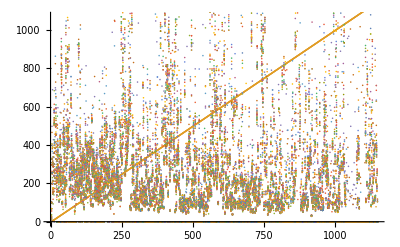

```mathematica
ListPlot[data]
```

## 尝试绘制单酒店的价格曲线

```mathematica
data2=data[[3;;32,3;;4]]
```

{{0,36},{1,56},{2,68},{3,68},{4,68},{5,68},{6,100},{7,100},{8,100},{9,100},{10,100},{11,100},{12,100},{13,100},{14,100},{15,100},{16,100},{17,100},{18,100},{19,100},{20,100},{21,100},{22,100},{23,100},{24,100},{25,100},{26,100},{27,100},{28,100},{29,100}}

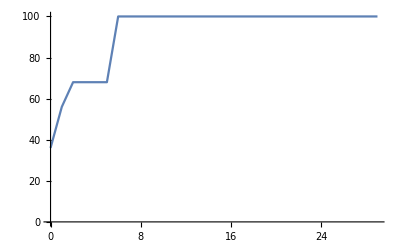

```mathematica
ListLinePlot[data2,AxesLabel->Automatic]
```

## 数据尝试统计平均值及长度

```mathematica
data1=data[[3;;32,3;;4]]
```

{{0,36},{1,56},{2,68},{3,68},{4,68},{5,68},{6,100},{7,100},{8,100},{9,100},{10,100},{11,100},{12,100},{13,100},{14,100},{15,100},{16,100},{17,100},{18,100},{19,100},{20,100},{21,100},{22,100},{23,100},{24,100},{25,100},{26,100},{27,100},{28,100},{29,100}}

```mathematica
N[Mean[data1]]
```

{14.5,92.1333}

```mathematica
data2 =data[[3;;3,4;;]]
```

{{36,249,196,230,151,93,286,260,140,398,268,173,211,382,552,328,389,181,115,319,167,206,220,271,133,175,103,277,243,117,390,140,184,228,172,754,99,147,91,233,64,420,353,375,176,266,168,222,216,77,1010,404,209,297,496,328,850,353,379,429,432,924,222,131,237,170,234,155,641,316,371,257,136,187,124,323,141,242,308,100000,100000,40,147,72,233,193,92,218,251,230,135,412,186,155,135,849,282,135,248,211,354,214,148,314,96,137,179,183,294,141,317,89,111,177,62,222,267,135,289,415,183,223,182,202,393,265,211,99,168,232,192,235,286,166,174,388,331,90,175,88,376,523,287,404,289,90,256,301,147,277,297,227,131,219,147,135,303,127,323,167,123,137,109,146,88,161,186,193,115,117,403,207,138,277,213,263,114,407,209,100000,100000,93,153,270,88,91,501,195,284,149,137,135,549,266,475,231,141,268,249,181,101,248,222,229,376,99,394,66,178,154,339,183,173,251,246,93,179,407,185,40,156,383,1200,140,532,363,249,159,224,264,104,198,256,137,174,189,153,110,310,150,152,79,387,338,108,748,204,302,455,1510,850,468,402,3397,2317,244,2218,888,688,238,268,268,328,328,298,298,339,359,368,418,468,483,498,457,1663,62,739,401,5406,62,115,617,1028,145,201,190,281,105,233,159,92,93,124,146,104,80,67,98,173,93,176,185,212,108,71,404,166,71,96,178,123,379,155,56,129,334,144,225,59,138,160,372,90,402,132,137,109,119,316,88,88,138,224,92,231,105,100,423,346,198,271,64,172,212,138,106,345,102,91,238,164,100000,100000,88,360,271,126,110,147,174,83,60,137,139,79,378,310,213,136,104,198,156,433,61,118,68,48,101,247,1493,100,130,75,1021,163,198,133,117,361,72,138,126,443,159,78,313,301,2644,1097,578,487,338,405,203,192,411,423,458,736,2686,132,545,995,649,353,414,249,60,589,311,433,100000,100000,100000,100000,100000,100000,100000,100000,307,410,237,467,319,57,212,932,61,142,87,196,267,365,192,525,365,340,190,1069,249,73,153,100,1432,528,60,87,80,314,99,102,49,257,72,63,110,70,116,670,102,59,70,107,50,119,196,335,106,112,51,218,53,78,352,442,972,336,113,320,103,84,81,935,197,144,83,146,192,265,377,124,86,86,348,208,551,220,110,69,86,182,171,100000,100000,100000,100000,99,203,149,251,62,73,101,92,77,92,87,89,95,80,121,270,286,78,94,35,111,83,220,170,243,1012,82,57,53,63,74,64,241,75,143,315,41,169,254,109,211,741,331,136,309,255,136,1888,741,507,442,227,477,8975,237,1229,218,3411,426,553,251,230,292,408,679,206,518,248,322,231,104,1107,1157,1558,2244,223,454,538,10090,212,585,100000,100000,100000,100000,100000,185,79,163,246,133,826,455,44,569,338,90,225,187,74,100,96,216,186,82,227,1590,1100,196,114,238,325,90,121,61,98,88,588,91,146,36,454,87,199,126,597,235,107,109,559,76,212,201,157,164,612,555,99,203,77,90,87,84,87,199,133,77,80,92,80,185,312,497,73,232,667,52,170,161,142,87,99,220,73,87,79,110,112,223,167,82,86,100000,118,100,180,65,87,133,150,91,112,100,148,55,64,198,1036,233,281,99,49,174,63,152,182,223,128,111,201,68,118,164,60,255,135,582,810,101,380,183,126,159,112,182,197,94,1683,2975,404,311,1210,815,817,732,156,348,218,1030,512,1345,86,62,271,1066,301,239,85,160,1731,230,3157,317,73,35,186,116,57,86,69,75,142,139,57,131,420,62,224,82,80,305,192,74,74,195,59,533,43,105,180,200,130,111,59,146,64,79,114,354,120,89,60,132,592,89,84,201,234,46,44,352,98,74,125,64,691,91,187,81,61,1571,719,64,147,107,317,820,102,160,234,121,693,99,166,143,340,211,75,90,254,168,133,133,177,187,81,96,120,182,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}}

```mathematica
data3 =Flatten[data2]
```

{36,249,196,230,151,93,286,260,140,398,268,173,211,382,552,328,389,181,115,319,167,206,220,271,133,175,103,277,243,117,390,140,184,228,172,754,99,147,91,233,64,420,353,375,176,266,168,222,216,77,1010,404,209,297,496,328,850,353,379,429,432,924,222,131,237,170,234,155,641,316,371,257,136,187,124,323,141,242,308,100000,100000,40,147,72,233,193,92,218,251,230,135,412,186,155,135,849,282,135,248,211,354,214,148,314,96,137,179,183,294,141,317,89,111,177,62,222,267,135,289,415,183,223,182,202,393,265,211,99,168,232,192,235,286,166,174,388,331,90,175,88,376,523,287,404,289,90,256,301,147,277,297,227,131,219,147,135,303,127,323,167,123,137,109,146,88,161,186,193,115,117,403,207,138,277,213,263,114,407,209,100000,100000,93,153,270,88,91,501,195,284,149,137,135,549,266,475,231,141,268,249,181,101,248,222,229,376,99,394,66,178,154,339,183,173,251,246,93,179,407,185,40,156,383,1200,140,532,363,249,159,224,264,104,198,256,137,174,189,153,110,310,150,152,79,387,338,108,748,204,302,455,1510,850,468,402,3397,2317,244,2218,888,688,238,268,268,328,328,298,298,339,359,368,418,468,483,498,457,1663,62,739,401,5406,62,115,617,1028,145,201,190,281,105,233,159,92,93,124,146,104,80,67,98,173,93,176,185,212,108,71,404,166,71,96,178,123,379,155,56,129,334,144,225,59,138,160,372,90,402,132,137,109,119,316,88,88,138,224,92,231,105,100,423,346,198,271,64,172,212,138,106,345,102,91,238,164,100000,100000,88,360,271,126,110,147,174,83,60,137,139,79,378,310,213,136,104,198,156,433,61,118,68,48,101,247,1493,100,130,75,1021,163,198,133,117,361,72,138,126,443,159,78,313,301,2644,1097,578,487,338,405,203,192,411,423,458,736,2686,132,545,995,649,353,414,249,60,589,311,433,100000,100000,100000,100000,100000,100000,100000,100000,307,410,237,467,319,57,212,932,61,142,87,196,267,365,192,525,365,340,190,1069,249,73,153,100,1432,528,60,87,80,314,99,102,49,257,72,63,110,70,116,670,102,59,70,107,50,119,196,335,106,112,51,218,53,78,352,442,972,336,113,320,103,84,81,935,197,144,83,146,192,265,377,124,86,86,348,208,551,220,110,69,86,182,171,100000,100000,100000,100000,99,203,149,251,62,73,101,92,77,92,87,89,95,80,121,270,286,78,94,35,111,83,220,170,243,1012,82,57,53,63,74,64,241,75,143,315,41,169,254,109,211,741,331,136,309,255,136,1888,741,507,442,227,477,8975,237,1229,218,3411,426,553,251,230,292,408,679,206,518,248,322,231,104,1107,1157,1558,2244,223,454,538,10090,212,585,100000,100000,100000,100000,100000,185,79,163,246,133,826,455,44,569,338,90,225,187,74,100,96,216,186,82,227,1590,1100,196,114,238,325,90,121,61,98,88,588,91,146,36,454,87,199,126,597,235,107,109,559,76,212,201,157,164,612,555,99,203,77,90,87,84,87,199,133,77,80,92,80,185,312,497,73,232,667,52,170,161,142,87,99,220,73,87,79,110,112,223,167,82,86,100000,118,100,180,65,87,133,150,91,112,100,148,55,64,198,1036,233,281,99,49,174,63,152,182,223,128,111,201,68,118,164,60,255,135,582,810,101,380,183,126,159,112,182,197,94,1683,2975,404,311,1210,815,817,732,156,348,218,1030,512,1345,86,62,271,1066,301,239,85,160,1731,230,3157,317,73,35,186,116,57,86,69,75,142,139,57,131,420,62,224,82,80,305,192,74,74,195,59,533,43,105,180,200,130,111,59,146,64,79,114,354,120,89,60,132,592,89,84,201,234,46,44,352,98,74,125,64,691,91,187,81,61,1571,719,64,147,107,317,820,102,160,234,121,693,99,166,143,340,211,75,90,254,168,133,133,177,187,81,96,120,182,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

```mathematica
Length[data3]
```

1147

```mathematica
Mean[DeleteCases[data3,100000]]
```

258521/1123

```mathematica
a =Mean[data3];
b={};
AppendTo[b,a]
```

{2658521/1147}

## 全部数据按天平均值统计

```mathematica
ave={};
For[i=3,i≤32,i++,
	temp1=Flatten[data[[i;;i,4;;]]];
	temp2=DeleteCases[temp1,-1];
	temp3= DeleteCases[temp2,100000];
	tempmean= Mean[temp3];
	AppendTo[ave,tempmean]
]
```

```mathematica
ave
```

{258823/821,248923/823,381032/689,370019/744,369890/797,153144/389,129422/409,255049/812,263265/824,85452/271,69793/201,290006/787,60304/199,246528/785,242727/794,248475/797,124039/396,284171/792,297028/799,247993/764,259011/796,83243/259,256667/776,131569/386,293237/748,309203/777,68047/191,280254/781,83925/254,239042/765}

```mathematica
ListLinePlot[ave,PlotStyle->RGBColor[1.,0,0],PlotTheme->"Business",PlotLabels->"Average price"]
```

-Graphics-

## 加上日期

```mathematica
DateListPlot[ave,{2020,12,29},PlotStyle->RGBColor[1.,0,0],PlotTheme->"Detailed",PlotLabels->"Average price",PlotMarkers->Automatic,Axes->{True,True},AxesLabel->{"date","price"}]
```

-Graphics-

## 加上标题

```mathematica
Show[%45,PlotLabel->HoldForm[Panyu' s hotel average price around Jan],LabelStyle->{GrayLevel[0]}]
```

-Graphics-